```mathematica
Quit[];
```

## 1. GeoSMEFT Setups

### Geometric SMEFT Definitions (In progress)

#### Field Space Connection Definitions (missing some corrections)

```mathematica
UsefulDefinitions;
(*vT2v = vT->v(1+3CH6 v^2/(4λ)+(9 CH6^2+4 CH^8 λ)/(8 λ^2)v^4);*)
KDelta[I_,J_] := KroneckerDelta[I,J];
I2 = IdentityMatrix[2];
ϕ={ϕ1,ϕ2,ϕ3,ϕ4};
ϕtilde={ϕ3,ϕ4,-ϕ1,-ϕ2};
ϕvev ={ϕ1->0,ϕ2->0,ϕ3->0,ϕ4->vT};

γA={({{0, 0, 0, -1}, {0, 0, -1, 0}, {0, 1, 0, 0}, {1, 0, 0, 0}}),({{0, 0, 1, 0}, {0, 0, 0, -1}, {-1, 0, 0, 0}, {0, 1, 0, 0}}),({{0, -1, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, -1}, {0, 0, 1, 0}}),({{0, -1, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, -1, 0}})};
ΓA={({{0, 0, 1, 0}, {0, 0, 0, -1}, {1, 0, 0, 0}, {0, -1, 0, 0}}),({{0, 0, 0, 1}, {0, 0, 1, 0}, {0, 1, 0, 0}, {1, 0, 0, 0}}),({{-1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}}),-IdentityMatrix[4] };
ϵABC={({{0, 0, 0, 0}, {0, 0, 1, 0}, {0, -1, 0, 0}, {0, 0, 0, 0}}),({{0, 0, -1, 0}, {0, 0, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 0}}),({{0, 1, 0, 0}, {-1, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}),({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}})};
gs={g2,g2,g2,g1};
γtildeA=γA*gs;


ScalarBilinear;
hLower[I_,J_]:=(1+((ϕ.ϕ)/2)^2(CHD8-CHD28) )KDelta[I,J]-2CHΔ6 ϕ[[I]] ϕ[[J]]+Sum[ΓA[[A]][[I]][[J]]* (ϕ.ΓA[[A]].ϕ),{A,1,4}]/2(CHD6/2+((ϕ.ϕ)/2) CHD28);


WeakGaugeBilinear;
gLower[A_,B_]:=(1-4((CHW6(1-KDelta[A,4])+CHB6 KDelta[A,4])((ϕ.ϕ)/2)+(CHW8(1-KDelta[A,4])+CHB8 KDelta[A,4])((ϕ.ϕ)/2)^2))KDelta[A,B]-
		CHW28(ϕ.ΓA[[A]].ϕ)(ϕ.ΓA[[B]].ϕ)(1-KDelta[A,4])(1-KDelta[B,4])+
		(CHWB6+CHWB8((ϕ.ϕ)/2)^2)((ϕ.ΓA[[A]].ϕ)(1-KDelta[A,4])KDelta[B,4]+(ϕ.ΓA[[B]].ϕ)(1-KDelta[B,4])KDelta[A,4]);


GluonGaugeBilinear;
kLower[A_,B_]:=(1-4(CHG6((ϕ.ϕ)/2)+CHG8((ϕ.ϕ)/2)^2))KDelta[A,B];


YukawaCoupling;
Yepr=0;


Coupling(Subscript[D, μ] ϕ)^I ψ̄ Γ^μ ψ;
LHL[J_,A_]:=-(ϕ.γA[[4]])[[J]]KDelta[A,4](CHψ16+CHψ18((ϕ.ϕ)/2))-(ϕ.γA[[A]])[[J]](1-KDelta[A,4])(CHψL36+CHψL38((ϕ.ϕ)/2))+
                           1/2(ϕ.γA[[4]])[[J]](1-KDelta[A,4])(ϕ.ΓA[[A]].ϕ)(CHψL28)+
                           Sum[Sum[(ϵABC[[A]][[B]][[C]])/2(ϕ.γA[[B]])[[J]] (ϕ.ΓA[[C]].ϕ)(CHψLϵ8),{B,1,4}],{C,1,4}] (* When A=4, both RH and LH term *)
RHL[J_]:=1/2(ϕtilde.(-ΓA[[4]]+ⅈ γA[[4]]))[[J]](CHud6+CHud8((ϕ.ϕ)/2)) (* Before putting in, need to change Wilson coeff to specific coupling *)


DipoleTerm(Subscript[W^μν, A] ψ̄ Subscript[σ, μν] σ^A ψ);
(*d[A_]:=(KDelta[A,4] CeB6);(*Not needed for now*)*)


CtoCtilde;
C2Ctilde = {CHD8->CHD8til (x/vT^2)^2, CHD28->CHD28til(x/vT^2)^2,CHΔ6->CHΔ6til(x/vT^2) ,CHD6->CHD6til (x/vT^2), CHD28->CHD28til (x/vT^2)^2,CHW6->CHW6til(x/vT^2), CHB6->CHB6til(x/vT^2), CHW8->CHW8til(x/vT^2)^2, CHB8->CHB8til(x/vT^2)^2,CHW28->CHW28til(x/vT^2)^2, CHWB6->CHWB6til(x/vT^2),CHWB8->CHWB8til(x/vT^2)^2,CHG6->CHG6til(x/vT^2), CHG8->CHG8til(x/vT^2)^2,CHψ16->CHψ16til(x/vT^2),CHψ18->CHψ18til(x/vT^2)^2, CHψL36->CHψL36til(x/vT^2), CHψL38->CHψL38til(x/vT^2)^2, CHψL28->CHψL28til(x/vT^2)^2,CHψLϵ8->CHψLϵ8til(x/vT^2)^2, CHud6->CHud6til(x/vT^2), CHud8->CHud8til(x/vT^2)^2};(* put x since it will be easier to extract contribution from higer dim *)
```

#### Definition of √(h_(I J)), √(h^(I J)) and √(g^(A B))

```mathematica
sqrthLower[I_,J_]:=Sqrt[hLower[I,J]]/.ϕvev
sqrthUpper[I_,J_]:=Which[KDelta[I,J]==0,0,KDelta[I,J]==1,1/sqrthLower[I,J]]
```

```mathematica
gLower2by2=({{gLower[3,3], gLower[3,4]}, {gLower[4,3], gLower[4,4]}})/.ϕvev;
gint=Simplify[gLower2by2-IdentityMatrix[2]];
gint1=gint[[1,1]];gint2=gint[[2,2]]; gint3=gint[[1,2]];
gint1p=1+gint1+Sqrt[Det[gLower2by2]];
gint2p=1+gint2+Sqrt[Det[gLower2by2]];
ginttemp=1/(√((gint1p+gint2p)Det[gLower2by2]))({{gint2p, -gint3}, {-gint3, gint1p}});

sqrtgUpper[A_,B_]:=({{1/Sqrt[gLower[1,1]/.ϕvev], 0, 0, 0}, {0, 1/Sqrt[gLower[2,2]/.ϕvev], 0, 0}, {0, 0, ginttemp[[1,1]], ginttemp[[1,2]]}, {0, 0, ginttemp[[2,1]], ginttemp[[2,2]]}})[[A,B]]
```

```mathematica
sqrtkUpper[A_,B_]:=1/Sqrt[kLower[A,B]]/.ϕvev
```

#### W^A → A^C Transformation (W^A = (√g)^AB U_BC A^C)

```mathematica
ir2=ⅈ/(√2);
r2=1/(√2);
Uij=({{r2, r2, 0, 0}, {ir2, -ir2, 0, 0}, {0, 0, cθ, sθ}, {0, 0, -sθ, cθ}});
gij=({{g11, 0, 0, 0}, {0, g22, 0, 0}, {0, 0, g33, g34}, {0, 0, g43, g44}}); (* Checked from sqrtg[A,B] that there are empty bins*)

WA={w1,w2,w3,B};
AA={Wp,Wm,Z,A};
ϕ={ϕ1,ϕ2,ϕ3,ϕ4};

wa2ac=gij.Uij.AA;
w2asub={w1->wa2ac[[1]],w2->wa2ac[[2]],w3->wa2ac[[3]],B->wa2ac[[4]]};
Print["W^1 = "wa2ac[[1]]]
Print["W^2 = "wa2ac[[2]]]
Print["W^3 = "wa2ac[[3]]]
Print["B = "wa2ac[[4]]]
```

W^1 =  ((g11 Wm)/(√2)+(g11 Wp)/(√2))

W^2 =  ((ⅈ g22 Wp)/(√2)-(ⅈ g22 Wm)/(√2))

W^3 =  (A (cθ g34+g33 sθ)+Z (cθ g33-g34 sθ))

B =  (A (cθ g44+g43 sθ)+Z (cθ g43-g44 sθ))

```mathematica
VectorBosonMassDiagonalize;

vij=({{-ir2, ir2, 0, 0}, {r2, r2, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, 1}}); (* ϕ -> Φ *)
hij=({{h11, 0, 0, 0}, {0, h22, 0, 0}, {0, 0, h33, 0}, {0, 0, 0, h44}}); (* √Subscript[h, IJ] definition *)
Dμϕ=-1/2 Sum[WA[[A]]*γtildeA[[A]],{A,1,4}].ϕ;
Dϕsq =1/2 Dμϕ.(hij^2).Dμϕ/.ϕvev/.w2asub//Simplify;

Dϕsq2=Dϕsq/.{g22->g11,g34->g43,h22->h11}//Simplify
Solve[cθ g2 g43-cθ g1 g44+g2 g33 sθ-g1 g43 sθ==0,g2](* Result Consistent with eq 4.8 *)
```

1/8 vT^2 (h33^2 (A (-cθ g1 g44+cθ g2 g43-g1 g43 sθ+g2 g33 sθ)+Z (-cθ g1 g43+cθ g2 g33+g1 g44 sθ-g2 g43 sθ))^2-1/2 g11^2 g2^2 h11^2 (Wm-Wp)^2+1/2 g11^2 g2^2 h11^2 (Wm+Wp)^2)

{{g2→(cθ g1 g44+g1 g43 sθ)/(cθ g43+g33 sθ)}}

```mathematica
(* W mass term *)
Print["m_W^2 = ",Coefficient[Dϕsq2,Wm Wp]]
```

m_W^2 = 1/4 g11^2 g2^2 h11^2 vT^2

```mathematica
(* Z mass term *)
g1replc = Solve[gz==g1(sθ g44-cθ g43)+g2 (cθ g33 -sθ g43),g1];
Print["1/2m_Z^2 = ",Coefficient[Dϕsq2,Z,2]/.g1replc[[1]]//Simplify]
```

1/2m_Z^2 = 1/8 gz^2 h33^2 vT^2

## 2. Schemes

### m_W Scheme ( m_W^2, m_Z^2, G_F , M_h^2 )

Scheme Format
(v̂)^2=1/(√2(Ĝ)_F)            sin^2(θ̂)=1/2(1-√(1-(4(ê)^2)/(√2(Ĝ)_F((M̂)_z)^2)))                 (ĝ)_1=(ê)/(c_(θ̂))                 (ĝ)_2=(ê)/(s_(θ̂))

```mathematica
(*Subscript[Ĝ, F]: Subscript[v̄, T] -> v̂ *)

vT2vhat={vT->Normal[Simplify[Series[vhat Sqrt[(1+√2 δGF6 x+√2 δGF8 x^2)],{x,0,2}]]]};

Normal[Simplify[Series[2 mzhat/sqrthLower[3,3] 1/vT/.C2Ctilde/.vT2vhat,{x,0,2}]]]/.vhat->1/(2^(1/4)√GFhat)(*/.αschemeinputs*);


(* Subscript[m̂, z]: θ̄ expressed in terms of inputs *)

rg11= Normal[Series[sqrtgUpper[1,1]/.C2Ctilde/.vT2vhat,{x,0,2}]];
rg33= Normal[Series[sqrtgUpper[3,3]/.C2Ctilde/.vT2vhat,{x,0,2}]];
rg34= Normal[Series[sqrtgUpper[3,4]/.C2Ctilde/.vT2vhat, {x,0,2}]];
rg44= Normal[Series[sqrtgUpper[4,4]/.C2Ctilde/.vT2vhat, {x,0,2}]];
rgp= Series[(rg33 rg44 + rg34^2)/.vT2vhat, {x,0,2}]//Normal;
rgm=Series[ (rg33 rg44 - rg34^2)/.vT2vhat, {x,0,2}]//Normal;

gzmWscheme={gzbar->Normal[Series[(2 mz)/(sqrthLower[3,3]vT)/.C2Ctilde/.vT2vhat,{x,0,2}]]};
g2input={g2-> Series[2 mw/(sqrtgUpper[1,1] sqrthLower[1,1] vT)/.C2Ctilde/.vT2vhat,{x,0,2}]};

sθbarsq = 1/((rg44^2+ rg34^2)^2)(-(g2/gzbar rgm)^2(rg44^2-rg34^2) + rg44^2(rg44^2+ rg34^2) + 2(g2/gzbar rgm)rg34 √(rg44^2(rg44^2+ rg34^2-((g2 rgm)/gzbar)^2)))/.gzmWscheme/.g2input;(* 
Alternate calculation is 1/((rg44^2+ rg34^2)^2)(-(g2/gzbar rgm)^2(rg44^2-rg34^2) + rg44^2(rg44^2+ rg34^2) - 2(g2/gzbar rgm)√(rg34^2 rg44^2(rg44^2+ rg34^2-((g2 rgm)/gzbar)^2)))
Both are equal to each other Following is comparison:
*)
```

```mathematica
(*Simplify[Series[1/((rg44^2+ rg34^2)^2)(-(g2/gzbar rgm)^2(rg44^2-rg34^2) + rg44^2(rg44^2+ rg34^2) - 2(g2/gzbar rgm)√(rg34^2 rg44^2(rg44^2+ rg34^2-((g2 rgm)/gzbar)^2)))/.gzmWscheme/.g2input,{x,0,2}],{CHWB6til>0,x>0}]/.vhat->1/(√(√2 GF))/.θ->ArcSin[√(1-mw^2/mz^2)]/.GF->1.1663787*10^-5/.mz->91.1876/.mw->80.387
Simplify[Series[1/((rg44^2+ rg34^2)^2)(-(g2/gzbar rgm)^2(rg44^2-rg34^2) + rg44^2(rg44^2+ rg34^2) + 2(g2/gzbar rgm)rg34 √(rg44^2(rg44^2+ rg34^2-((g2 rgm)/gzbar)^2)))/.gzmWscheme/.g2input,{x,0,2}],{CHWB6til>0,x>0}]/.vhat->1/(√(√2 GF))/.θ->ArcSin[√(1-mw^2/mz^2)]/.GF->1.1663787*10^-5/.mz->91.1876/.mw->80.387*)
```

```mathematica
(*x^2(-0.0000561441 (3706.22 CHB6til CHWB6til-4608.96 CHD6til CHWB6til+1853.11 (6 CHW6til CHWB6til+60624.1 CHWB8til))-0.0000300655 (12924.1 CHD28til+25848.3 CHW28til-4608.96 CHWB6til^2))//Expand
1.62244*10^-8 x^2 (-1.28253*10^7 CHB6til CHWB6til-2.39498*10^7 CHD28til+1.59492*10^7 CHD6til CHWB6til-4.78997*10^7 CHW28til-3.84759*10^7 CHW6til CHWB6til+8.54091*10^6 CHWB6til^2-3.88761*10^11 CHWB8til)//Expand*)
```

```mathematica
cθbar=Simplify[Series[Sqrt[1-sθbarsq],{x,0,2}],Cos[θ]>0]//Normal;
sθbar=Simplify[Series[Sqrt[sθbarsq],{x,0,2}],Sin[θ]>0]//Normal;
```

```mathematica
ebarmWscheme={ebar->Chop[Normal[Simplify[Series[g2(sθbar rg33 +cθbar rg34)/.g2input/.mz->91.1876/.mw->80.387/.vhat->1/(√(√2 GF))/.GF->1.1663787*10^-5,{x,0,2}],{x>0}]]]};
g2barmWscheme={g2bar-> Normal[Series[2 mw/(sqrthLower[1,1] vT)/.C2Ctilde/.vT2vhat,{x,0,2}]]};
sθzmWscheme={sθz->Chop[Sqrt[Simplify[Series[ebar/gzbar(sθbar rg44-cθbar rg34)/(cθbar rg44+sθbar rg34)/.ebarmWscheme/.gzmWscheme/.mz->91.1876/.mw->80.387/.vhat->1/(√(√2 GF))/.GF->1.1663787*10^-5,{x,0,2}],{x>0}]//Normal]]};
```

### Scheme dependent couplings

#### Definitions

```mathematica
(*W^A -> A^C Transformation(W^A = (√g)^AB Subscript[U, BC] A^C)*)
ir2=ⅈ/(√2);r2=1/(√2);
Uij=({{r2, r2, 0, 0}, {ir2, -ir2, 0, 0}, {0, 0, cθ, sθ}, {0, 0, -sθ, cθ}});
gij=({{g11, 0, 0, 0}, {0, g22, 0, 0}, {0, 0, g33, g34}, {0, 0, g43, g44}}); (* Checked from sqrtg[A,B] that there are empty bins*)

WA={w1,w2,w3,B};
AA={Wp,Wm,Z,A};
ϕ={ϕ1,ϕ2,ϕ3,ϕ4};

wa2ac=gij.Uij.AA;
w2asub={w1->wa2ac[[1]],w2->wa2ac[[2]],w3->wa2ac[[3]],B->wa2ac[[4]]};
(*Print["W^1 = "wa2ac[[1]]]
Print["W^2 = "wa2ac[[2]]]
Print["W^3 = "wa2ac[[3]]]
Print["B = "wa2ac[[4]]]
*)

		(* g -> ḡ notation *)
gtogzbar={g43->g34,g1->gzbar sθz^2/(sθ g44-cθ g34),g2->gzbar (1-sθz^2)/(cθ g33-sθ g34),cθz^2->1-sθz^2};
gtoebar={g43->g34,g1->ebar/(sθ g34+cθ g44),g2->ebar/(cθ g34+sθ g33)};
gtog2bar={g22->g11,g2->g2bar/g11};


		(* Covariant Derivatives *)
DμLH[Y_]:=ⅈ(g2 Sum[PauliMatrix[a]/2 WA[[a]],{a,1,3}]+g1 Y B I2)/.w2asub/.g43->g34//Simplify

DμRH[Y_]:=ⅈ g1 Y B/.w2asub/.g43->g34//Simplify


σA={PauliMatrix[1],PauliMatrix[2],PauliMatrix[3],IdentityMatrix[2]};
Dμϕ=-1/2 Sum[WA[[A]]*γtildeA[[A]],{A,1,4}].ϕ;
LHaddCoup[LHdag_,LH_]:=Sum[Sum[LHL[J,A] Dμϕ[[J]](σbarμ LHdag.σA[[A]].LH),{A,1,4}],{J,1,4}]/.{ϕ1->0,ϕ2->0,ϕ3->0,ϕ4->vT}/.w2asub//Simplify;

RHaddCoupAZ[RHdag_,RH_]:=Sum[LHL[J,4] Dμϕ[[J]](RHdag σμ RH),{J,1,4}]/.ϕvev/.w2asub//Simplify;
RHaddCoupW[dcdag_,uc_]:=Sum[RHL[J] Dμϕ[[J]](uc σμ dcdag),{J,1,4}]/.ϕvev/.w2asub//Simplify;


LHLreplace[x_,CV1_,CV2_,CVL1_,CVL2_,CVL3_,CϵL_]:=x/.{CHψ16til-> CV1,CHψ18til->CV2,CHψL36til->CVL1,CHψL38til->CVL2,CHψL28til->CVL3,CHψLϵ8til->CϵL}
```

#### Quark vertex

Kinetic

```mathematica
Clear[Q,u,d]

(* LH *)
Q=({{u}, {d}});
Qdag=({{udag, ddag}});

LHffZkin=(ⅈ Z*σbarμ Qdag.Coefficient[DμLH[1/6].Q,Z]/.gtogzbar/.cθz^2->1-sθz^2//Simplify//Expand)[[1]][[1]];
LHffAkin=(ⅈ A*σbarμ Qdag.Coefficient[DμLH[1/6].Q,A]/.gtoebar/.cθz^2->1-sθz^2//Simplify//Expand)[[1]][[1]];
LHffWpkin=(ⅈ Wp σbarμ Qdag.Coefficient[DμLH[1/6].Q,Wp]/.gtog2bar/.cθz^2->1-sθz^2//Simplify//Expand)[[1]][[1]];
LHffWmkin=(ⅈ Wm σbarμ Qdag.Coefficient[DμLH[1/6].Q,Wm]/.gtog2bar/.cθz^2->1-sθz^2//Simplify//Expand)[[1]][[1]];

(* RH *)
          (* u^c *)
RHuuZkin=ⅈ Z σμ uc Coefficient[DμRH[2/3] ucdag,Z]/.gtogzbar//Simplify;
RHuuAkin=ⅈ A σμ uc Coefficient[DμRH[2/3] ucdag,A]/.gtoebar//Simplify;

          (* d^c *)
RHddZkin=ⅈ Z σμ dc Coefficient[DμRH[-1/3] dcdag,Z]/.gtogzbar//Simplify;
RHddAkin=ⅈ A σμ dc Coefficient[DμRH[-1/3] dcdag,A]/.gtoebar//Simplify;
```

Additional coupling shift from(D_μ ϕ)^I ψ̄ Γ^μ ψ

```mathematica
LHffAadd=(A*Coefficient[LHaddCoup[Qdag,Q],A]/.gtoebar//Simplify//Expand)[[1]][[1]];
LHffZadd=(Z*Coefficient[LHaddCoup[Qdag,Q],Z]/.gtogzbar//Simplify//Expand)[[1]][[1]];
LHffWpadd=(Wp*Coefficient[LHaddCoup[Qdag,Q],Wp]/.gtog2bar//Simplify)[[1]][[1]];
LHffWmadd=(Wm*Coefficient[LHaddCoup[Qdag,Q],Wm]/.gtog2bar//Simplify)[[1]][[1]];

RHffAadd=A*Coefficient[RHaddCoupAZ[uc,ucdag]+RHaddCoupAZ[dc,dcdag],A]/.gtoebar//Simplify//Expand;
RHffZadd=Z*Coefficient[RHaddCoupAZ[uc,ucdag]+RHaddCoupAZ[dc,dcdag],Z]/.gtogzbar//Simplify;

RHffWpadd=RHaddCoupW[uc,dcdag]/.gtog2bar//Simplify;(* For RH coupling to W *)
RHffWmadd=-RHffWpadd/.{uc->dc,dcdag->ucdag,Wp->Wm};  (* Not sure if there should be - *)

	(* Cast Wilson Coefficients to fermion specific*)
LHffAadd=LHLreplace[LHffAadd/.C2Ctilde,CHQ16til,CHQ18til,CHQ36til,CHQ38til,CHQ28til,CHQϵ8til];
LHffZadd=LHLreplace[LHffZadd/.C2Ctilde,CHQ16til,CHQ18til,CHQ36til,CHQ38til,CHQ28til,CHQϵ8til];
RHffAadd=uc ucdag LHLreplace[Coefficient[RHffAadd/.C2Ctilde,uc ucdag],CHuc16til,CHuc18til,CHuc36til,CHuc38til,CHuc28til,CHucϵ8til]+
                  dc dcdag LHLreplace[Coefficient[RHffAadd/.C2Ctilde,dc dcdag],CHdc16til,CHdc18til,CHdc36til,CHdc38til,CHdc28til,CHdcϵ8til]//Simplify;
RHffZadd=uc ucdag LHLreplace[Coefficient[RHffZadd/.C2Ctilde,uc ucdag],CHuc16til,CHuc18til,CHuc36til,CHuc38til,CHuc28til,CHucϵ8til]+
                  dc dcdag LHLreplace[Coefficient[RHffZadd/.C2Ctilde,dc dcdag],CHdc16til,CHdc18til,CHdc36til,CHdc38til,CHdc28til,CHdcϵ8til]//Simplify;
LHffWpadd=LHLreplace[LHffWpadd/.C2Ctilde,CHQ16til,CHQ18til,CHQ36til,CHQ38til,CHQ28til,CHQϵ8til]//Simplify;
LHffWmadd=LHLreplace[LHffWmadd/.C2Ctilde,CHQ16til,CHQ18til,CHQ36til,CHQ38til,CHQ28til,CHQϵ8til]//Simplify;
RHffWpadd=RHffWpadd/.C2Ctilde//Simplify;
RHffWmadd=RHffWmadd/.C2Ctilde//Simplify;
```

Total qqV vertex

```mathematica
Clear[u,d,uc,dc,PL,PR]

uLAval=Coefficient[LHffAkin+LHffAadd,u σbarμ udag A ];
dLAval=Coefficient[LHffAkin+LHffAadd,d σbarμ ddag A ];
uLZval=Coefficient[LHffZkin+LHffZadd,u σbarμ udag Z ];
dLZval=Coefficient[LHffZkin+LHffZadd,d σbarμ ddag Z ];

uRAval=Coefficient[RHuuAkin+RHffAadd,uc σμ ucdag A ];
dRAval=Coefficient[RHddAkin+RHffAadd,dc σμ dcdag A ];
uRZval=Coefficient[RHuuZkin+RHffZadd,uc σμ ucdag Z ];
dRZval=Coefficient[RHddZkin+RHffZadd,dc σμ dcdag Z ];

ubardLWpval=Coefficient[LHffWpadd+LHffWpkin,udag σbarμ d Wp ] ;
dbaruLWmval=Coefficient[LHffWmadd+LHffWmkin,ddag σbarμ u Wm ] ;

ubardRWpval=Coefficient[RHffWpadd,uc σμ dcdag Wp ] ;
dbaruRWmval=Coefficient[RHffWmadd,dc σμ ucdag Wm ] ;
```

```mathematica
uLAval
uRAval
dLAval
dRAval
uLZval
uRZval
dLZval
dRZval

ubardLWpval
ubardRWpval
dbaruLWmval(* All Equal to Adam's Notebook *)
dbaruRWmval
```

-(2 ebar)/3

-(2 ebar)/3

ebar/3

ebar/3

(CHQ16til gzbar x)/2+1/4 CHQ18til gzbar x^2-1/4 CHQ28til gzbar x^2-(CHQ36til gzbar x)/2-1/4 CHQ38til gzbar x^2+(2 gzbar sθz^2)/3-gzbar/2

1/4 gzbar x (2 CHuc16til+CHuc18til x)+(2 gzbar sθz^2)/3

(CHQ16til gzbar x)/2+1/4 CHQ18til gzbar x^2+1/4 CHQ28til gzbar x^2+(CHQ36til gzbar x)/2+1/4 CHQ38til gzbar x^2-(gzbar sθz^2)/3+gzbar/2

1/4 gzbar x (2 CHdc16til+CHdc18til x)-(gzbar sθz^2)/3

-g2bar/(√2)-(g2bar x (2 CHQ36til+x (CHQ38til-ⅈ CHQϵ8til)))/(2 √2)

(ⅈ g2bar x (2 CHud6til+CHud8til x))/(4 √2)

-g2bar/(√2)-(g2bar x (2 CHQ36til+x (CHQ38til+ⅈ CHQϵ8til)))/(2 √2)

-(ⅈ g2bar x (2 CHud6til+CHud8til x))/(4 √2)

#### Lepton vertex

Kinetic

```mathematica
Clear[e,ν]

(* LH *)
L=({{ν}, {e}});
Ldag=({{νdag, edag}});
LHllZkin=(ⅈ Z σbarμ Ldag.Coefficient[(DμLH[-1/2].L),Z]/.gtogzbar/.cθz^2->1-sθz^2//Simplify//Expand)[[1]][[1]];
LHllAkin=(ⅈ A σbarμ Ldag.Coefficient[(DμLH[-1/2].L),A]/.gtoebar/.cθz^2->1-sθz^2//Simplify//Expand)[[1]][[1]];
LHllWpkin=ⅈ Wp σbarμ Coefficient[Ldag.DμLH[-1/2].L,Wp][[1,1]]/.gtog2bar//Simplify;
LHllWmkin=ⅈ Wm σbarμ Coefficient[Ldag.DμLH[-1/2].L,Wm][[1,1]]/.gtog2bar//Simplify;

(* RH *)
RHllZkin=ⅈ Z ec σμ Coefficient[DμRH[-1] ecdag,Z]/.gtogzbar/.cθz^2->1-sθz^2//Simplify;
RHllAkin=ⅈ A ec σμ Coefficient[DμRH[-1]ecdag,A]/.gtoebar/.cθz^2->1-sθz^2//Simplify;
```

Additional coupling shift from(D_μ ϕ)^I ψ̄ Γ^μ ψ

```mathematica
LHllAadd=(A*Coefficient[LHaddCoup[Ldag,L],A]/.gtoebar//Simplify//Expand)[[1,1]];
LHllZadd=(Z*Coefficient[LHaddCoup[Ldag,L],Z]/.gtogzbar//Simplify//Expand)[[1,1]];
LHllWpadd=(Wp*Coefficient[LHaddCoup[Ldag,L],Wp]/.gtog2bar//Simplify)[[1,1]];
LHllWmadd=(Wm*Coefficient[LHaddCoup[Ldag,L],Wm]/.gtog2bar//Simplify)[[1,1]];

RHllAadd=A*Coefficient[RHaddCoupAZ[ec,ecdag],A]/.gtoebar//Simplify;
RHllZadd=Z*Coefficient[RHaddCoupAZ[ec,ecdag],Z]/.gtogzbar//Simplify;

	(* Cast Wilson Coefficients to fermion specific*)
LHllAadd=LHLreplace[LHllAadd/.C2Ctilde,CHL16til,CHL18til,CHL36til,CHL38til,CHL28til,CHLϵ8til];
LHllZadd=LHLreplace[LHllZadd/.C2Ctilde,CHL16til,CHL18til,CHL36til,CHL38til,CHL28til,CHLϵ8til];
LHllWpadd=LHLreplace[LHllWpadd/.C2Ctilde,CHL16til,CHL18til,CHL36til,CHL38til,CHL28til,CHLϵ8til]//Simplify;
LHllWmadd=LHLreplace[LHllWmadd/.C2Ctilde,CHL16til,CHL18til,CHL36til,CHL38til,CHL28til,CHLϵ8til]//Simplify;
RHllAadd=LHLreplace[Coefficient[RHllAadd/.C2Ctilde,ec ecdag],CHec16til,CHec18til,CHec36til,CHec38til,CHec28til,CHecϵ8til]ec ecdag//Simplify;
RHllZadd=LHLreplace[Coefficient[RHllZadd/.C2Ctilde,ec ecdag],CHec16til,CHec18til,CHec36til,CHec38til,CHec28til,CHecϵ8til]ec ecdag//Simplify;
```

Total llV vertex

```mathematica
Clear[e,ν,ec,PL,PR]

eLAval=Coefficient[LHllAkin+LHllAadd,e σbarμ edag A ];
eLZval=Coefficient[LHllZkin+LHllZadd,e σbarμ edag Z ];
νLAval=Coefficient[LHllZkin+LHllZadd,ν σbarμ νdag A ];
νLZval=Coefficient[LHllZkin+LHllZadd,ν σbarμ νdag Z ];

eRAval=Coefficient[RHllAkin+RHllAadd,ec σμ ecdag A ];
eRZval=Coefficient[RHllZkin+RHllZadd,ec σμ ecdag Z ] ;
νRAval=Coefficient[LHllZkin+LHllZadd,νc σμ νcdag A ];
νRZval=Coefficient[LHllZkin+LHllZadd,νc σμ νcdag Z ];

νbareLWpval=Coefficient[LHllWpkin+LHllWpadd,νdag σbarμ e Wp];
ebarνLWmval=Coefficient[LHllWmkin+LHllWmadd,edag σbarμ ν Wm];
```

```mathematica
eLAval
eRAval
νLAval
νLZval

eLZval
eRZval
νRAval
νRZval

νbareLWpval
ebarνLWmval
```

ebar

ebar

0

(CHL16til gzbar x)/2+1/4 CHL18til gzbar x^2-1/4 CHL28til gzbar x^2-(CHL36til gzbar x)/2-1/4 CHL38til gzbar x^2-gzbar/2

(CHL16til gzbar x)/2+1/4 CHL18til gzbar x^2+1/4 CHL28til gzbar x^2+(CHL36til gzbar x)/2+1/4 CHL38til gzbar x^2-gzbar sθz^2+gzbar/2

1/4 gzbar x (2 CHec16til+CHec18til x)-gzbar sθz^2

0

0

-g2bar/(√2)-(g2bar x (2 CHL36til+x (CHL38til-ⅈ CHLϵ8til)))/(2 √2)

-g2bar/(√2)-(g2bar x (2 CHL36til+x (CHL38til+ⅈ CHLϵ8til)))/(2 √2)

```mathematica
ZinvolveCoupling[x_]:=x/.gzmWscheme/.sθzmWscheme/.ebarmWscheme/.g2bar->g2 /.g2input/.mz->91.1876/.mw->80.387/.vhat->1/(√(√2 GF))/.GF->1.1663787*10^-5
γinvolveCoupling[x_]:=x/.ebarmWscheme/.mz->91.1876/.mw->80.387/.vhat->1/(√(√2 GF))/.GF->1.1663787*10^-5
WinvolveCoupling[x_]:=x/.g2barmWscheme/.mz->91.1876/.mw->80.387/.vhat->1/(√(√2 GF))/.GF->1.1663787*10^-5
```

```mathematica
Series[WinvolveCoupling[ubardLWpval],{x,0,1}]
Series[WinvolveCoupling[ubardRWpval],{x,0,1}]
Series[WinvolveCoupling[dbaruLWmval],{x,0,1}] (* All Equal to Adam's Notebook *)
Series[WinvolveCoupling[dbaruRWmval],{x,0,1}]
```

-0.461719+x (0.326485 δGF6-0.461719 CHQ36til)+O(x^2)

(0.+0.23086 ⅈ) CHud6til x+O(x^2)

-0.461719+x (0.326485 δGF6-0.461719 CHQ36til)+O(x^2)

(0.-0.23086 ⅈ) CHud6til x+O(x^2)

```mathematica
-Series[γinvolveCoupling[uLAval],{x,0,1}]//Simplify
-Series[γinvolveCoupling[dLAval],{x,0,1}]
Series[γinvolveCoupling[eLAval],{x,0,1}]
```

0.205502+x (-0.179154 CHD6til-0.383753 CHWB6til-0.145312 δGF6)+O(x^2)

-0.102751+0.0895772 x (1. CHD6til+2.14203 CHWB6til+0.8111 δGF6)+O(x^2)

0.308253+x (-0.268731 CHD6til-0.57563 CHWB6til-0.217968 δGF6)+O(x^2)

## 3. Monolepton Final State (Checked)

```mathematica
<<FeynCalc`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

### Definitions

```mathematica
SetOptions[{Plot,LogPlot,LogLogPlot,ListPlot,ListLogLogPlot},ImageSize->600,AspectRatio->0.7,Frame->True,FrameStyle->15,PlotStyle->{Thick},GridLines->Full];
SetOptions[{ListContourPlot},ImageSize->600,AspectRatio->0.7,Frame->True,FrameStyle->15,ContourLabels->True]; (*Plot with frames*)

Clear[Q,L,mz,e,θw,Mll];
$Assumptions=InM>0&&mz>0&&M>0;
FCClearScalarProducts[];

Definitions;

Sw=Sin[θw];Cw=Cos[θw];
(*g = e/Sw*)
PL=ChiralityProjector[-1];PR=ChiralityProjector[+1];

(*Chirality dependent*)
(* uLA, dLA, uLZ, dLZ, uRA, dRA, uRZ, dRZ, eLA, eLZ, eRA, eRZ *)
gL[x_]:=Switch[x,ν,νLZ,l,eLZ,u,uLZ,d,dLZ];
gR[x_]:=Switch[x,ν,νRZ,l,eRZ,u,uRZ,d,dRZ];
(* W depedning on *)
                                                         (* W^+ν̄ γ Subscript[P, L] e         W^-ē γ Subscript[P, L] ν             W^+ū γ Subscript[P, L] d             W^-ū γ Subscript[P, R] d            W^+d̄ γ Subscript[P, L] u           W^-d̄ γ Subscript[P, R] u *)
gwcoupling[x_]:=Switch[x,νbareL,νbareLWp*PL,ebarνL,ebarνLWm*PL,ubardL,ubardLWp*PL,ubardR,ubardRWp*PR,dbaruL,dbaruLWm*PL,dbaruR,dbaruRWm*PR];

Q[x_]:=Switch[x,ν,νLA*PL+νRA*PR,l,eLA*PL+eRA*PR,u,uLA*PL+uRA*PR,d,dLA*PL+dRA*PR];
(*MassReplace[x_]:=x/.{mz->91.1876,Γz->2.4952, α->1/127.91,mh->100};*)


Couplings;

(*Chirality dependent*)
gz[q_,μ_]:=ⅈ GA[μ].((gL[q])+(gR[q]));
gγ[q_,μ_]:=ⅈ Q[q] GA[μ]/.PL->1-PR//Simplify;
gw[q_,μ_]:=ⅈ GA[μ].gwcoupling[q];

Propagators;
lProp[p_,m_]:=(ⅈ(FV[p,α]GA[α]+m))/(SP[p]-m^2)//DiracSimplify;
ScalarProp[p_,m_]:=ⅈ/(SP[p]-m^2);
γProp[p_,x_,y_]:=(-ⅈ MT[x,y]/SP[p]);
zProp[p_,α_,β_,flag_]:=( -ⅈ/(SP[p]-mz^2+ⅈ Γz mz))(MT[α,β]-flag(FV[p,α]FV[p,β])/SP[p])//Normal; (*Flag=0 to exclude second part (EoM reducible)*)
wProp[p_,α_,β_,flag_]:=( -ⅈ/(SP[p]-mw^2+ⅈ Γw mw))(MT[α,β]-flag(FV[p,α]FV[p,β])/SP[p])//Normal;
RelFermDiagramSign=-1;

GeVtoPB = 1/(2.568*10^-9);
```

### Kinematics

```mathematica
(*
SP[p1,p1]=mp1^2; SP[p2,p2]=mp2^2;
SP[p3,p3]=mp3^2; SP[p4,p4]=mp4^2;
SP[p1,p2]=(s-mp1^2-mp2^2)/2;SP[p3,p4]=(s-mp3^2-mp4^2)/2;
SP[p1,p3]=(u-mp1^2-mp3^2)/-2;SP[p2,p4]=(u-mp2^2-mp4^2)/-2;
SP[p1,p4]=(t-mp1^2-mp4^2)/-2;SP[p2,p3]=(t-mp2^2-mp3^2)/-2;
SP[p1+p2,p1+p2] =s; 
SP[p1-p3,p1-p3]=u;
SP[p1-p4,p1-p4]=t;*)


SP[p1,p1]=mp1^2; SP[p2,p2]=mp2^2;
SP[p3,p3]=mp3^2; SP[p4,p4]=mp4^2;
SP[p1,p2] = 2 Ein^2; SP[p3,p4]=2 Ein^2-mp1^2;
SP[p1,p3]=Ein^2-Ein^2 Cθ;
SP[p1,p4]=Ein^2+Ein^2 Cθ;
SP[p2,p3]=Ein^2+Ein^2 Cθ ;
SP[p2,p4]=Ein^2-Ein^2 Cθ; (* Better for proton level calculation *)

mp1=0;
mp2=0;
mp3=0;
mp4=0;
```

### Amplitude u d̄ → e^+ν

#### GeoSMEFT Amplitude

```mathematica
(* gwcoupling[x_]:=Switch[x,νbareL,νbareLWp,ebarνL,ebarνLWm,ubardL,ubardLWp, ubardR,ubardRWp,dbaruL,dbaruLWm,dbaruR,dbaruRWm]; *)
```

```mathematica
LLStruc= (SpinorVBar[p2,mp2].GA[μ].PL.SpinorU[p1,mp1])MT[μ,ν](SpinorUBar[p3,mp3].GA[ν].PL.SpinorV[p4,mp4])//DiracSimplify;
RLStruc=  (SpinorVBar[p2,mp2].GA[μ].PR.SpinorU[p1,mp1])MT[μ,ν](SpinorUBar[p3,mp3].GA[ν].PL.SpinorV[p4,mp4])//DiracSimplify;

wPropOx=wProp[p1+p2,μ,ν,0]/.MT[μ,ν]->1;
```

#### Contact Terms

```mathematica
(* Definitions *)
contactterms=ToExpression[Import["/Users/Tae/Desktop/GeoSMEFT/contact_terms.txt"]];

CLLdbaru=Coefficient[contactterms, νdag σbarμ e ddag σbarμ u];
```

```mathematica
CLLdbaru
```

1/2 (vT^2 ((2 CHLQ28til x^2)/vT^4+(2 CHLQ58til x^2)/vT^4)+(4 CLQ36til x)/vT^2-(2 CLQs38til s x^2)/vT^4-(2 CLQt38til t x^2)/vT^4)

#### Decay Width of W

```mathematica
Wdecaywidth=ToExpression[Import["/Users/Tae/Desktop/GeoSMEFT/Partonic_cross-section/mW_scheme-W_decay_width.txt"]];
Γw0val=SeriesCoefficient[Wdecaywidth//Expand,{x,0,0}];
Γw1val=SeriesCoefficient[Wdecaywidth//Expand,{x,0,1}];
Γw2val=SeriesCoefficient[Wdecaywidth//Expand,{x,0,2}];
```

#### Amplitude Square GeoSMEFT

```mathematica
LLchiralSq=FermionSpinSum[Normal[Series[LLStruc*ComplexConjugate[(LLStruc)/.{ μ->ρ}],{x,0,2}]]]/.DiracTrace->Tr //Contract //Simplify;
RLchiralSq=FermionSpinSum[Normal[Series[RLStruc*ComplexConjugate[(RLStruc)/.{ μ->ρ}],{x,0,2}]]]/.DiracTrace->Tr //Contract //Simplify;
```

```mathematica
ampLLnostruc=1/ⅈ(ⅈ dbaruLWm wPropOx ⅈ νbareLWp+(ⅈ CLLdbaru1 x+ⅈ CLLdbaru2 x^2+ⅈ CLLdbarus s x^2+ⅈ CLLdbarut t x^2))//.{s->2SP[p1,p2], t->-2SP[p1,p3],SP[p1+p2]->s}//Simplify;
ampRLnostruc=1/ⅈ(ⅈ dbaruRWm wPropOx ⅈ νbareLWp)//.{s->2SP[p1,p2], t->-2SP[p1,p3],SP[p1+p2]->s}//Simplify;
```

```mathematica
ampLLnostrucSq[order_]:=SeriesCoefficient[ComplexExpand[ampLLnostruc*ComplexExpand[Conjugate[ampLLnostruc/.dbaruLWm->dbaruLWmstar/.νbareLWp->νbareLWpstar]]]/.Γw->Γw0+Γw1 x+Γw2 x^2,{x,0,order}]//Normal
ampRLnostrucSq[order_]:=SeriesCoefficient[ComplexExpand[ampRLnostruc*ComplexExpand[Conjugate[ampRLnostruc/.dbaruRWm->dbaruRWmstar/.νbareLWp->νbareLWpstar]]]/.Γw->Γw0+Γw1 x+Γw2 x^2,{x,0,order}]//Normal
```

```mathematica
struct1=Coefficient[ampLLnostrucSq[0],dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar];
struct2=Coefficient[ampLLnostrucSq[1],dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar Γw1];
struct3=Coefficient[ampLLnostrucSq[2],dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar Γw2]//Simplify;
struct4=Coefficient[ampLLnostrucSq[2],dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar Γw1^2]//Simplify;
struct5=ComplexExpand[Re[Coefficient[ampLLnostrucSq[1],dbaruLWm νbareLWp CLLdbaru1]]]//Simplify;
struct6=ComplexExpand[Re[Coefficient[ampLLnostrucSq[2],dbaruLWm νbareLWp CLLdbaru1 Γw1]]]//Simplify;
struct7=ComplexExpand[Re[Coefficient[ampLLnostrucSq[2],dbaruLWm νbareLWp CLLdbaru2]]]//Simplify;
struct8=ComplexExpand[Re[Coefficient[ampLLnostrucSq[2],dbaruLWm νbareLWp CLLdbarus]]]//Simplify;
struct9=ComplexExpand[Re[Coefficient[ampLLnostrucSq[2],dbaruLWm νbareLWp CLLdbarut]]]//Simplify;
struct10=Coefficient[ampLLnostrucSq[2],CLLdbaru1^2]//Simplify;
RLstructure=Coefficient[ampRLnostrucSq[0],dbaruRWm dbaruRWmstar νbareLWp νbareLWpstar];
```

```mathematica
LLstructures={struct1,struct2,struct3,struct4,struct5,struct6,struct7,struct8,struct9,struct10};
couplings={dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar,dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar Γw1,dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar Γw2,dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar Γw1^2,2dbaruLWm νbareLWp CLLdbaru1,2dbaruLWm νbareLWp CLLdbaru1 Γw1,2dbaruLWm νbareLWp CLLdbaru2,2dbaruLWm νbareLWp CLLdbarus,2dbaruLWm νbareLWp CLLdbarut,CLLdbaru1^2,dbaruRWm dbaruRWmstar νbareLWp νbareLWpstar};
```

#### dσ/dΩ Parton level

```mathematica
monodσLLdΩ =1/(64 π^2 4 Ein^2)(*Phase Space*)1/3(*Color Av.*)1/4(*Spin Av.*)LLchiralSq LLstructures /.{mz->91.1876,mw->80.387,Γw0->Γw0val};
monodσRLdΩ =1/(64 π^2 4 Ein^2)(*Phase Space*)1/3(*Color Av.*)1/4(*Spin Av.*)RLchiralSq RLstructure /.{mz->91.1876,mw->80.387,Γw0->Γw0val};

monodσdΩ=AppendTo[monodσLLdΩ,monodσRLdΩ]
```

{((Cθ+1)^2 Ein^2)/(192 π^2 (16 Ein^4-51696.6 Ein^2+4.17854×10^7)),-(13.9516 (Cθ+1)^2 Ein^2)/((16 Ein^4-51696.6 Ein^2+4.17854×10^7)^2),-(13.9516 (Cθ+1)^2 Ein^2)/((16 Ein^4-51696.6 Ein^2+4.17854×10^7)^2),-((Cθ+1)^2 Ein^2 (103393. Ein^4-3.34067×10^8 Ein^2+2.69321×10^11))/(192 π^2 (16 Ein^4-51696.6 Ein^2+4.17854×10^7)^3),((Cθ+1)^2 Ein^2 (4 Ein^2-6462.07))/(192 π^2 (16 Ein^4-51696.6 Ein^2+4.17854×10^7)),(13.9516 (Cθ+1)^2 Ein^2 (6462.07-4 Ein^2))/((16 Ein^4-51696.6 Ein^2+4.17854×10^7)^2),((Cθ+1)^2 Ein^2 (4 Ein^2-6462.07))/(192 π^2 (16 Ein^4-51696.6 Ein^2+4.17854×10^7)),((Cθ+1)^2 Ein^2 (16 Ein^4-25848.3 Ein^2))/(192 π^2 (16 Ein^4-51696.6 Ein^2+4.17854×10^7)),((Cθ-1) (Cθ+1)^2 Ein^4 (4 Ein^2-6462.07))/(96 π^2 (16 Ein^4-51696.6 Ein^2+4.17854×10^7)),((Cθ+1)^2 Ein^2)/(192 π^2),((Cθ-1)^2 Ein^2)/(192 π^2 (16 Ein^4-51696.6 Ein^2+4.17854×10^7))}

```mathematica
monoσ=2π Integrate[monodσdΩ,{Cθ,-1,1}]/.Ein->M/2//Simplify
```

{(0.00221049 M^2)/(M^4-12924.1 M^2+4.17854×10^7),-(58.4403 M^2)/((M^4-12924.1 M^2+4.17854×10^7)^2),-(58.4403 M^2)/((M^4-12924.1 M^2+4.17854×10^7)^2),(-14.2843 M^6+184612. M^4-5.9533×10^8 M^2)/((M^4-12924.1 M^2+4.17854×10^7)^3),(0.00221049 M^2 (M^2-6462.07))/(M^4-12924.1 M^2+4.17854×10^7),-(58.4403 M^2 (M^2-6462.07))/((M^4-12924.1 M^2+4.17854×10^7)^2),(0.00221049 M^2 (M^2-6462.07))/(M^4-12924.1 M^2+4.17854×10^7),(0.00221049 M^4 (M^2-6462.07))/(M^4-12924.1 M^2+4.17854×10^7),-(0.000552621 M^4 (M^2-6462.07))/(M^4-12924.1 M^2+4.17854×10^7),M^2/(144 π),(0.00221049 M^2)/(M^4-12924.1 M^2+4.17854×10^7)}

### PDF Apply based on Helicity Structure

```mathematica
SetDirectory["~/Google\ Drive/Research/Instruction/Tools/Cuba-4.2.1"];
Install["Vegas"];
```

```mathematica
pdfpath="~/Google\ Drive/Research/Instruction/Tools/math_package_v2";
SetDirectory[pdfpath];
<< NNPDF`
prefix=pdfpath<>"/Grids/";
namegrid = "NNPDF30_nlo_as_0118";
Timing[InitializePDFGrid[prefix,namegrid]]
```

Welcome in the Mathematica Package for NNPDF PDFs. The following Functions are available:

- Initializing and interpolating PDFs

InitializePDFGrid;

- Using NNPDF PDFs

xPDFcv; xPDFEnsemble; xPDFRep; xPDF; xPDFCL; xMin; xMax; Q2min; Q2Max; NumberPDF; HasPhoton;

- Parameters for the QCD analysis

alphaSMZ; mCharm; mBottom; mTop; MZ; alphas; Infoalphas; Lam4; Lam5;

For the usage of each of these Functions, please read the README file or type ?Function.

'Version' '5.8.8'

'Description:'

'NNPDF30_nlo_as_0118.LHgrid'

'Reference: arXiv:1410.8849'

'Fit: NLO global fit, alphas(MZ)=0.118'

'NNPDF Collaboration: R.D. Ball, V. Bertone, '

'S. Carrazza, C.S. Deans, L. Del Debbio, '

'S. Forte, A. Guffanti, N.P. Hartland, '

'J.I. Latorre, J. Rojo and M. Ubiali'

'This set has 100 member PDF'

'mem=0 --> average on replicas.'

'Evolution: pol. interpolation on the LH grid'

Grid division:

x axis: 100 points; 1.×10^-9 <= x <= 1.

Q^2 axis: 50 points; 1. <= Q^2 <= 1.×10^10

Reading PDF set from file. Please wait.

PDF set successfully read from file.

Interpolating PDF set on the grid. Please wait.

PDF grid interpolated. Ready to use the NNPDF set.

{13.0133,Null}

```mathematica
Definitions;

ecoll=13000;
scoll=ecoll^2;


(*pdf[x_,Q_,flav_]:=If[x≤1.0&&x>10^-9&&xPDFcv[x,Q^2,flav]>0,1/x xPDFcv[x,Q^2,flav],0]*)
pdf[x_,flav_]:=xPDFcv[x,mz^2,flav]/.mz->91.1876/.mw->80.387

(* remember: quarkID = 2 (up), 1 (down),   gluon = 0 *)

udbarpdf=2/M(pdf[M/(√scoll)Exp[Y],2]pdf[M/(√scoll)Exp[-Y],-1]+pdf[M/(√scoll)Exp[Y],-1]pdf[M/(√scoll)Exp[-Y], 2]);
csbarpdf=2/M(pdf[M/(√scoll)Exp[Y],4]pdf[M/(√scoll)Exp[-Y],-3]+pdf[M/(√scoll)Exp[Y],-3]pdf[M/(√scoll)Exp[-Y], 4]);
```

```mathematica
couplings
monoσ
```

{dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar,Γw1 dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar,Γw2 dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar,Γw1^2 dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar,2 CLLdbaru1 dbaruLWm νbareLWp,2 CLLdbaru1 Γw1 dbaruLWm νbareLWp,2 CLLdbaru2 dbaruLWm νbareLWp,2 CLLdbarus dbaruLWm νbareLWp,2 CLLdbarut dbaruLWm νbareLWp,CLLdbaru1^2,dbaruRWm dbaruRWmstar νbareLWp νbareLWpstar}

{(0.00221049 M^2)/(M^4-12924.1 M^2+4.17854×10^7),-(58.4403 M^2)/((M^4-12924.1 M^2+4.17854×10^7)^2),-(58.4403 M^2)/((M^4-12924.1 M^2+4.17854×10^7)^2),(-14.2843 M^6+184612. M^4-5.9533×10^8 M^2)/((M^4-12924.1 M^2+4.17854×10^7)^3),(0.00221049 M^2 (M^2-6462.07))/(M^4-12924.1 M^2+4.17854×10^7),-(58.4403 M^2 (M^2-6462.07))/((M^4-12924.1 M^2+4.17854×10^7)^2),(0.00221049 M^2 (M^2-6462.07))/(M^4-12924.1 M^2+4.17854×10^7),(0.00221049 M^4 (M^2-6462.07))/(M^4-12924.1 M^2+4.17854×10^7),-(0.000552621 M^4 (M^2-6462.07))/(M^4-12924.1 M^2+4.17854×10^7),M^2/(144 π),(0.00221049 M^2)/(M^4-12924.1 M^2+4.17854×10^7)}

```mathematica
σpp2lνOxudbar={};
Monitor[Do[
protonσ=1/10^5 Vegas[10^5 monoσ[[i]]udbarpdf,{M,1,13000}, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]},MaxPoints-> 5000000,NStart-> 100000, NIncrease-> 50000,PrecisionGoal -> 3,AccuracyGoal-> 3, Verbose->0];
AppendTo[σpp2lνOxudbar,{couplings[[i]],protonσ}],{i,1,Length[monoσ]}],i];
σpp2lνOxudbar
```

Vegas::success: Needed 1000000 function evaluations.

General::stop: Further output of Vegas::success will be suppressed during this calculation.

Vegas::accuracy: Desired accuracy was not reached within 5200000 function evaluations.

General::stop: Further output of Vegas::accuracy will be suppressed during this calculation.

(dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar | (0.000462233 | 2.35559×10^-7 | 1.53355×10^-9)
Γw1 dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar | (-0.000226497 | 1.15513×10^-7 | 1.31102×10^-8)
Γw2 dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar | (-0.000226497 | 1.15513×10^-7 | 1.31102×10^-8)
Γw1^2 dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar | (0.000110762 | 7.14722×10^-8 | 4.99723×10^-9)
2 CLLdbaru1 dbaruLWm νbareLWp | (0.00433616 | 0.000109482 | 1.11022×10^-21)
2 CLLdbaru1 Γw1 dbaruLWm νbareLWp | (0.00043877 | 0.0000113833 | 2.86882×10^-18)
2 CLLdbaru2 dbaruLWm νbareLWp | (0.00433616 | 0.000109482 | 1.11022×10^-21)
2 CLLdbarus dbaruLWm νbareLWp | (6498.59 | 5.16604 | 1.38764×10^-10)
2 CLLdbarut dbaruLWm νbareLWp | (-1624.65 | 1.29151 | 1.38764×10^-10)
CLLdbaru1^2 | (6482.96 | 4.70157 | 2.87527×10^-9)
dbaruRWm dbaruRWmstar νbareLWp νbareLWpstar | (0.000462233 | 2.35559×10^-7 | 1.53355×10^-9))

```mathematica
σpp2lνOxcsbar={};
Monitor[Do[
protonσ=1/10^5 Vegas[10^5 monoσ[[i]]csbarpdf,{M,1,13000}, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]},MaxPoints-> 5000000,NStart-> 100000, NIncrease-> 50000,PrecisionGoal -> 3,AccuracyGoal-> 3, Verbose->0];
AppendTo[σpp2lνOxcsbar,{couplings[[i]],protonσ}],{i,1,Length[monoσ]}],i];
σpp2lνOxcsbar
```

Vegas::success: Needed 1000000 function evaluations.

General::stop: Further output of Vegas::success will be suppressed during this calculation.

Vegas::accuracy: Desired accuracy was not reached within 5200000 function evaluations.

General::stop: Further output of Vegas::accuracy will be suppressed during this calculation.

(dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar | (0.000101905 | 5.39129×10^-8 | 5.62271×10^-10)
Γw1 dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar | (-0.000049612 | 2.47091×10^-8 | 3.67231×10^-8)
Γw2 dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar | (-0.000049612 | 2.47091×10^-8 | 3.67231×10^-8)
Γw1^2 dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar | (0.000024259 | 1.57442×10^-8 | 2.97661×10^-8)
2 CLLdbaru1 dbaruLWm νbareLWp | (-0.00788458 | 0.0000240007 | 2.71219×10^-15)
2 CLLdbaru1 Γw1 dbaruLWm νbareLWp | (0.000144656 | 2.48394×10^-6 | 9.30771×10^-12)
2 CLLdbaru2 dbaruLWm νbareLWp | (-0.00788458 | 0.0000240007 | 2.71219×10^-15)
2 CLLdbarus dbaruLWm νbareLWp | (301.697 | 0.290794 | 1.59146×10^-11)
2 CLLdbarut dbaruLWm νbareLWp | (-75.4243 | 0.0726985 | 1.59146×10^-11)
CLLdbaru1^2 | (355.397 | 0.334573 | 2.36145×10^-9)
dbaruRWm dbaruRWmstar νbareLWp νbareLWpstar | (0.000101905 | 5.39129×10^-8 | 5.62271×10^-10))

```mathematica
udbar2lνOx0=SeriesCoefficient[WinvolveCoupling[Sum[GeVtoPB (σpp2lνOxudbar[[i,1]]σpp2lνOxudbar[[i,2,1,1]]),{i,1,11}]//.{CLLdbaru1->SeriesCoefficient[CLLdbaru,{x,0,1}]x,CLLdbaru2->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],vT^-2] x^2/vT^2,CLLdbarus->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],s] x^2,CLLdbarut->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],t] x^2,Γw1->Γw1val x, Γw2->Γw2val x^2,dbaruLWm->dbaruLWmval,dbaruRWm->dbaruRWmval,νbareLWp->νbareLWpval,dbaruLWmstar->ComplexExpand[Conjugate[dbaruLWmval]],dbaruRWmstar->ComplexExpand[Conjugate[dbaruRWmval]],νbareLWpstar->ComplexExpand[Conjugate[νbareLWpval]]}/.vT2vhat],{x,0,0}]

udbar2lνOx1=SeriesCoefficient[WinvolveCoupling[Sum[GeVtoPB (σpp2lνOxudbar[[i,1]]σpp2lνOxudbar[[i,2,1,1]]),{i,1,11}]//.{CLLdbaru1->SeriesCoefficient[CLLdbaru,{x,0,1}]x,CLLdbaru2->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],vT^-2] x^2/vT^2,CLLdbarus->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],s] x^2,CLLdbarut->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],t] x^2,Γw1->Γw1val x, Γw2->Γw2val x^2,dbaruLWm->dbaruLWmval,dbaruRWm->dbaruRWmval,νbareLWp->νbareLWpval,dbaruLWmstar->ComplexExpand[Conjugate[dbaruLWmval]],dbaruRWmstar->ComplexExpand[Conjugate[dbaruRWmval]],νbareLWpstar->ComplexExpand[Conjugate[νbareLWpval]]}/.vT2vhat],{x,0,1}]//Expand

udbar2lνOx2=SeriesCoefficient[WinvolveCoupling[Sum[GeVtoPB (σpp2lνOxudbar[[i,1]]σpp2lνOxudbar[[i,2,1,1]]),{i,1,11}]//.{CLLdbaru1->SeriesCoefficient[CLLdbaru,{x,0,1}]x,CLLdbaru2->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],vT^-2] x^2/vT^2,CLLdbarus->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],s] x^2,CLLdbarut->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],t] x^2,Γw1->Γw1val x, Γw2->Γw2val x^2,dbaruLWm->dbaruLWmval,dbaruRWm->dbaruRWmval,νbareLWp->νbareLWpval,dbaruLWmstar->ComplexExpand[Conjugate[dbaruLWmval]],dbaruRWmstar->ComplexExpand[Conjugate[dbaruRWmval]],νbareLWpstar->ComplexExpand[Conjugate[νbareLWpval]]}//.vT2vhat],{x,0,2}]//Expand//Chop
```

8180.47

10894.4 CHL36til+5427.88 CHQ36til+23.751 CLQ36til-11541.6 δGF6

2040.29 CHD28til-2040.29 CHD8til-1840.23 CHL36til^2+14505.2 CHL36til CHQ36til+27.0285 CHL36til CLQ36til-15357.8 CHL36til δGF6+5447.21 CHL38til+11.8755 CHLQ28til+11.8755 CHLQ58til-4569.68 CHQ36til^2+30.306 CHQ36til CLQ36til-7632.32 CHQ36til δGF6+2713.94 CHQ38til+678.485 CHud6til^2+2747.56 CLQ36til^2-74.1306 CLQ36til δGF6-293.575 CLQs38til+73.3938 CLQt38til+16289.4 δGF6^2-11541.6 δGF8

```mathematica
csbar2lνOx0=SeriesCoefficient[WinvolveCoupling[Sum[GeVtoPB (σpp2lνOxcsbar[[i,1]]σpp2lνOxcsbar[[i,2,1,1]]),{i,1,11}]//.{CLLdbaru1->SeriesCoefficient[CLLdbaru,{x,0,1}]x,CLLdbaru2->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],vT^-2] x^2/vT^2,CLLdbarus->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],s] x^2,CLLdbarut->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],t] x^2,Γw1->Γw1val x, Γw2->Γw2val x^2,dbaruLWm->dbaruLWmval,dbaruRWm->dbaruRWmval,νbareLWp->νbareLWpval,dbaruLWmstar->ComplexExpand[Conjugate[dbaruLWmval]],dbaruRWmstar->ComplexExpand[Conjugate[dbaruRWmval]],νbareLWpstar->ComplexExpand[Conjugate[νbareLWpval]]}/.vT2vhat],{x,0,0}]

csbar2lνOx1=SeriesCoefficient[WinvolveCoupling[Sum[GeVtoPB (σpp2lνOxcsbar[[i,1]]σpp2lνOxcsbar[[i,2,1,1]]),{i,1,11}]//.{CLLdbaru1->SeriesCoefficient[CLLdbaru,{x,0,1}]x,CLLdbaru2->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],vT^-2] x^2/vT^2,CLLdbarus->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],s] x^2,CLLdbarut->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],t] x^2,Γw1->Γw1val x, Γw2->Γw2val x^2,dbaruLWm->dbaruLWmval,dbaruRWm->dbaruRWmval,νbareLWp->νbareLWpval,dbaruLWmstar->ComplexExpand[Conjugate[dbaruLWmval]],dbaruRWmstar->ComplexExpand[Conjugate[dbaruRWmval]],νbareLWpstar->ComplexExpand[Conjugate[νbareLWpval]]}/.vT2vhat],{x,0,1}]//Expand

csbar2lνOx2=SeriesCoefficient[WinvolveCoupling[Sum[GeVtoPB (σpp2lνOxcsbar[[i,1]]σpp2lνOxcsbar[[i,2,1,1]]),{i,1,11}]//.{CLLdbaru1->SeriesCoefficient[CLLdbaru,{x,0,1}]x,CLLdbaru2->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],vT^-2] x^2/vT^2,CLLdbarus->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],s] x^2,CLLdbarut->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],t] x^2,Γw1->Γw1val x, Γw2->Γw2val x^2,dbaruLWm->dbaruLWmval,dbaruRWm->dbaruRWmval,νbareLWp->νbareLWpval,dbaruLWmstar->ComplexExpand[Conjugate[dbaruLWmval]],dbaruRWmstar->ComplexExpand[Conjugate[dbaruRWmval]],νbareLWpstar->ComplexExpand[Conjugate[νbareLWpval]]}//.vT2vhat],{x,0,2}]//Expand//Chop
```

1803.48

2409.57 CHL36til+1212.18 CHQ36til-43.1871 CLQ36til-2560.96 δGF6

452.719 CHD28til-452.719 CHD8til-391.537 CHL36til^2+3223.42 CHL36til CHQ36til-42.1066 CHL36til CLQ36til-3429.41 CHL36til δGF6+1204.79 CHL38til-21.5936 CHLQ28til-21.5936 CHLQ58til-989.629 CHQ36til^2-41.026 CHQ36til CLQ36til-1736.9 CHQ36til δGF6+606.089 CHQ38til+151.522 CHud6til^2+150.622 CLQ36til^2+119.859 CLQ36til δGF6-13.6292 CLQs38til+3.40731 CLQt38til+3637.44 δGF6^2-2560.96 δGF8

```mathematica
Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/mW-scheme_udbar2lnuSM_M1to13000.txt",udbar2lνOx0];
Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/mW-scheme_udbar2lnuOx_M1to13000.txt",udbar2lνOx1];
Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/mW-scheme_udbar2lnuOx2_M1to13000.txt",udbar2lνOx2];

Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/mW-scheme_csbar2lnuSM_M1to13000.txt",csbar2lνOx0];
Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/mW-scheme_csbar2lnuOx_M1to13000.txt",csbar2lνOx1];
Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/mW-scheme_csbar2lnuOx2_M1to13000.txt",csbar2lνOx2];
```

#### σ_SMEFT/σ_SM

```mathematica
σSMmonolep=udbar2lνOx0+csbar2lνOx0;
σOxmonolep=udbar2lνOx1+csbar2lνOx1;
σOx2monolep=udbar2lνOx2+csbar2lνOx2;
σmonolepSMEFTOx=σOxmonolep/σSMmonolep//Expand
σmonolepSMEFTOx2=σOx2monolep/σSMmonolep//Expand
```

1.33254 CHL36til+0.665073 CHQ36til-0.00194674 CLQ36til-1.41252 δGF6

0.249701 CHD28til-0.249701 CHD8til-0.223536 CHL36til^2+1.77571 CHL36til CHQ36til-0.00151023 CHL36til CLQ36til-1.88174 CHL36til δGF6+0.666268 CHL38til-0.000973369 CHLQ28til-0.000973369 CHLQ58til-0.556824 CHQ36til^2-0.00107372 CHQ36til CLQ36til-0.938427 CHQ36til δGF6+0.332536 CHQ38til+0.0831341 CHud6til^2+0.290284 CLQ36til^2+0.00458023 CLQ36til δGF6-0.0307698 CLQs38til+0.00769245 CLQt38til+1.99588 δGF6^2-1.41252 δGF8

### σ̂ ( u + d̄ → l^+ + ν )

```mathematica
σhatudbarOx0=GeVtoPB*SeriesCoefficient[WinvolveCoupling[monoσ.couplings//.{CLLdbaru1->SeriesCoefficient[CLLdbaru,{x,0,1}]x,CLLdbaru2->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],vT^-2] x^2/vT^2,CLLdbarus->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],s] x^2,CLLdbarut->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],t] x^2,Γw1->Γw1val x, Γw2->Γw2val x^2,dbaruLWm->dbaruLWmval,dbaruRWm->dbaruRWmval,νbareLWp->νbareLWpval,dbaruLWmstar->ComplexExpand[Conjugate[dbaruLWmval]],dbaruRWmstar->ComplexExpand[Conjugate[dbaruRWmval]],νbareLWpstar->ComplexExpand[Conjugate[νbareLWpval]]}/.vT2vhat],{x,0,0}]//Expand
```

(39120.6 M^2)/(M^4-12924.1 M^2+4.17854×10^7)

```mathematica
σhatudbarOx1=GeVtoPB*SeriesCoefficient[WinvolveCoupling[monoσ.couplings//.{CLLdbaru1->SeriesCoefficient[CLLdbaru,{x,0,1}]x,CLLdbaru2->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],vT^-2] x^2/vT^2,CLLdbarus->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],s] x^2,CLLdbarut->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],t] x^2,Γw1->Γw1val x, Γw2->Γw2val x^2,dbaruLWm->dbaruLWmval,dbaruRWm->dbaruRWmval,νbareLWp->νbareLWpval,dbaruLWmstar->ComplexExpand[Conjugate[dbaruLWmval]],dbaruRWmstar->ComplexExpand[Conjugate[dbaruRWmval]],νbareLWpstar->ComplexExpand[Conjugate[νbareLWpval]]}/.vT2vhat],{x,0,1}]//Expand
```

(78241.1 CHL36til M^2)/(M^4-12924.1 M^2+4.17854×10^7)-(1.41046×10^9 CHL36til M^2)/((M^4-12924.1 M^2+4.17854×10^7)^2)+(78241.1 CHQ36til M^2)/(M^4-12924.1 M^2+4.17854×10^7)-(2.82093×10^9 CHQ36til M^2)/((M^4-12924.1 M^2+4.17854×10^7)^2)+(12.1077 CLQ36til M^4)/(M^4-12924.1 M^2+4.17854×10^7)-(78241.1 CLQ36til M^2)/(M^4-12924.1 M^2+4.17854×10^7)-(110650. δGF6 M^2)/(M^4-12924.1 M^2+4.17854×10^7)+(2.99205×10^9 δGF6 M^2)/((M^4-12924.1 M^2+4.17854×10^7)^2)

```mathematica
σhatudbarOx2=GeVtoPB*SeriesCoefficient[WinvolveCoupling[monoσ.couplings//.{CLLdbaru1->SeriesCoefficient[CLLdbaru,{x,0,1}]x,CLLdbaru2->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],vT^-2] x^2/vT^2,CLLdbarus->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],s] x^2,CLLdbarut->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],t] x^2,Γw1->Γw1val x, Γw2->Γw2val x^2,dbaruLWm->dbaruLWmval,dbaruRWm->dbaruRWmval,νbareLWp->νbareLWpval,dbaruLWmstar->ComplexExpand[Conjugate[dbaruLWmval]],dbaruRWmstar->ComplexExpand[Conjugate[dbaruRWmval]],νbareLWpstar->ComplexExpand[Conjugate[νbareLWpval]]}/.vT2vhat],{x,0,2}]//Expand//Chop
```

-(2.1157×10^9 δGF6^2 M^6)/((M^4-12924.1 M^2+4.17854×10^7)^3)+(1.9947×10^9 CHL36til δGF6 M^6)/((M^4-12924.1 M^2+4.17854×10^7)^3)+(3.9894×10^9 CHQ36til δGF6 M^6)/((M^4-12924.1 M^2+4.17854×10^7)^3)-(0.0000998592 CLQs38til M^6)/(M^4-12924.1 M^2+4.17854×10^7)+(0.0000249648 CLQt38til M^6)/(M^4-12924.1 M^2+4.17854×10^7)-(4.70155×10^8 CHL36til^2 M^6)/((M^4-12924.1 M^2+4.17854×10^7)^3)-(1.88062×10^9 CHQ36til^2 M^6)/((M^4-12924.1 M^2+4.17854×10^7)^3)-(1.88062×10^9 CHL36til CHQ36til M^6)/((M^4-12924.1 M^2+4.17854×10^7)^3)+(2.73436×10^13 δGF6^2 M^4)/((M^4-12924.1 M^2+4.17854×10^7)^3)-(34.2459 CLQ36til δGF6 M^4)/(M^4-12924.1 M^2+4.17854×10^7)+(926034. CLQ36til δGF6 M^4)/((M^4-12924.1 M^2+4.17854×10^7)^2)-(2.57798×10^13 CHL36til δGF6 M^4)/((M^4-12924.1 M^2+4.17854×10^7)^3)-(5.15595×10^13 CHQ36til δGF6 M^4)/((M^4-12924.1 M^2+4.17854×10^7)^3)+(6.05387 CHLQ28til M^4)/(M^4-12924.1 M^2+4.17854×10^7)+(6.05387 CHLQ58til M^4)/(M^4-12924.1 M^2+4.17854×10^7)+(12.1077 CHL36til CLQ36til M^4)/(M^4-12924.1 M^2+4.17854×10^7)+(12.1077 CHQ36til CLQ36til M^4)/(M^4-12924.1 M^2+4.17854×10^7)+(0.645297 CLQs38til M^4)/(M^4-12924.1 M^2+4.17854×10^7)-(0.161324 CLQt38til M^4)/(M^4-12924.1 M^2+4.17854×10^7)-(436537. CHL36til CLQ36til M^4)/((M^4-12924.1 M^2+4.17854×10^7)^2)-(873073. CHQ36til CLQ36til M^4)/((M^4-12924.1 M^2+4.17854×10^7)^2)+(6.07635×10^12 CHL36til^2 M^4)/((M^4-12924.1 M^2+4.17854×10^7)^3)+(2.43054×10^13 CHQ36til^2 M^4)/((M^4-12924.1 M^2+4.17854×10^7)^3)+(2.43054×10^13 CHL36til CHQ36til M^4)/((M^4-12924.1 M^2+4.17854×10^7)^3)+0.000936832 CLQ36til^2 M^2+(234723. δGF6^2 M^2)/(M^4-12924.1 M^2+4.17854×10^7)-(1.26942×10^10 δGF6^2 M^2)/((M^4-12924.1 M^2+4.17854×10^7)^2)-(8.81764×10^16 δGF6^2 M^2)/((M^4-12924.1 M^2+4.17854×10^7)^3)-(221299. CHL36til δGF6 M^2)/(M^4-12924.1 M^2+4.17854×10^7)-(221299. CHQ36til δGF6 M^2)/(M^4-12924.1 M^2+4.17854×10^7)+(221299. CLQ36til δGF6 M^2)/(M^4-12924.1 M^2+4.17854×10^7)+(1.19682×10^10 CHL36til δGF6 M^2)/((M^4-12924.1 M^2+4.17854×10^7)^2)+(1.79523×10^10 CHQ36til δGF6 M^2)/((M^4-12924.1 M^2+4.17854×10^7)^2)-(5.9841×10^9 CLQ36til δGF6 M^2)/((M^4-12924.1 M^2+4.17854×10^7)^2)+(8.31335×10^16 CHL36til δGF6 M^2)/((M^4-12924.1 M^2+4.17854×10^7)^3)+(1.66267×10^17 CHQ36til δGF6 M^2)/((M^4-12924.1 M^2+4.17854×10^7)^3)-(110650. δGF8 M^2)/(M^4-12924.1 M^2+4.17854×10^7)+(2.99205×10^9 δGF8 M^2)/((M^4-12924.1 M^2+4.17854×10^7)^2)+(39120.6 CHL36til^2 M^2)/(M^4-12924.1 M^2+4.17854×10^7)+(39120.6 CHQ36til^2 M^2)/(M^4-12924.1 M^2+4.17854×10^7)+(9780.14 CHud6til^2 M^2)/(M^4-12924.1 M^2+4.17854×10^7)+(19560.3 CHD28til M^2)/(M^4-12924.1 M^2+4.17854×10^7)-(19560.3 CHD8til M^2)/(M^4-12924.1 M^2+4.17854×10^7)+(39120.6 CHL38til M^2)/(M^4-12924.1 M^2+4.17854×10^7)-(39120.6 CHLQ28til M^2)/(M^4-12924.1 M^2+4.17854×10^7)-(39120.6 CHLQ58til M^2)/(M^4-12924.1 M^2+4.17854×10^7)+(156482. CHL36til CHQ36til M^2)/(M^4-12924.1 M^2+4.17854×10^7)+(39120.6 CHQ38til M^2)/(M^4-12924.1 M^2+4.17854×10^7)-(78241.1 CHL36til CLQ36til M^2)/(M^4-12924.1 M^2+4.17854×10^7)-(78241.1 CHQ36til CLQ36til M^2)/(M^4-12924.1 M^2+4.17854×10^7)-(3.52616×10^9 CHL36til^2 M^2)/((M^4-12924.1 M^2+4.17854×10^7)^2)-(7.05232×10^9 CHQ36til^2 M^2)/((M^4-12924.1 M^2+4.17854×10^7)^2)-(3.52616×10^8 CHud6til^2 M^2)/((M^4-12924.1 M^2+4.17854×10^7)^2)-(5.28924×10^8 CHD28til M^2)/((M^4-12924.1 M^2+4.17854×10^7)^2)+(5.28924×10^8 CHD8til M^2)/((M^4-12924.1 M^2+4.17854×10^7)^2)-(7.05232×10^8 CHL38til M^2)/((M^4-12924.1 M^2+4.17854×10^7)^2)-(8.46279×10^9 CHL36til CHQ36til M^2)/((M^4-12924.1 M^2+4.17854×10^7)^2)-(1.41046×10^9 CHQ38til M^2)/((M^4-12924.1 M^2+4.17854×10^7)^2)+(2.82093×10^9 CHL36til CLQ36til M^2)/((M^4-12924.1 M^2+4.17854×10^7)^2)+(5.64186×10^9 CHQ36til CLQ36til M^2)/((M^4-12924.1 M^2+4.17854×10^7)^2)-(1.95948×10^16 CHL36til^2 M^2)/((M^4-12924.1 M^2+4.17854×10^7)^3)-(7.8379×10^16 CHQ36til^2 M^2)/((M^4-12924.1 M^2+4.17854×10^7)^3)-(7.8379×10^16 CHL36til CHQ36til M^2)/((M^4-12924.1 M^2+4.17854×10^7)^3)

#### To LaTeX

```mathematica
toLaTEXform={CLQ36til->" C_LQ^(3, (6))",CHL36til->" C_HL^(3, (6))",CHQ36til->" C_HQ^(3, (6))",CHD28til->" C_HD^(2, (8))",CHD8til->" C_HD^(8)",CHL38til->" C_HL^(3, (8))",CHQ38til->" C_HQ^(3, (8))",CHud6til->" C_Hud^(6)",CHLQ28til->" C_HLQ^(2, (8))",CHLQ58til->" C_HLQ^(5, (8))",CLQs38til->" C_LQ^(s, 3, (8))",CLQt38til->" C_LQ^(t, 3, (8))",δGF6->" δG_F^(6)",δGF8->" δG_F^(8)"};
```

```mathematica
SetPrecision[σhatudbarOx0/.M->√(ŝ),3]
```

(39100. ŝ)/((ŝ)^2-12900. ŝ+4.18×10^7)

```mathematica
monoleptonox1={CHL36til,CHQ36til,CLQ36til,δGF6};
```

```mathematica
For[n=1,n≤Length[monoleptonox1],n++,Print[(Coefficient[SetPrecision[σhatudbarOx1,3],monoleptonox1[[n]]]//Simplify)monoleptonox1[[n]]/.M->√(ŝ)/.toLaTEXform]]
```

(78000. (ŝ)^3  C_HL^(3, (6)))/(((ŝ)^2-12900. ŝ+4.18×10^7)^2)

((78000. (ŝ)^3-1.×10^9 (ŝ)^2+3.3×10^12 ŝ)  C_HQ^(3, (6)))/(((ŝ)^2-12900. ŝ+4.18×10^7)^2)

((12.1 (ŝ)^2-78200. ŝ)  C_LQ^(3, (6)))/((ŝ)^2-12900. ŝ+4.18×10^7)

((-110000. (ŝ)^3+1.4×10^9 (ŝ)^2-4.6×10^12 ŝ)  δG_F^(6))/(((ŝ)^2-12900. ŝ+4.18×10^7)^2)

```mathematica
monoleptonox2={CHud6til^2,CHQ36til^2,CHL36til^2,CLQ36til^2,CHD8til,CHD28til,CHQ38til,CHL38til,CHQ36til CHL36til,CHL36til CLQ36til,CHQ36til CLQ36til,CHLQ28til,CHLQ58til,CLQs38til,CLQt38til, δGF6^2,CHL36til δGF6,CHQ36til δGF6,δGF6 CLQ36til,δGF8};
```

```mathematica
For[n=1,n≤Length[monoleptonox2],n++,Print[(SetPrecision[Coefficient[σhatudbarOx2,monoleptonox2[[n]]]//Simplify,3]) monoleptonox2[[n]]/.M->√(ŝ)/.toLaTEXform]]
```

((9780. (ŝ)^3-1.26×10^8 (ŝ)^2+4.08×10^11 ŝ) (C_Hud^(6))^2)/(((ŝ)^2-12900. ŝ+4.18×10^7)^2)

(ŝ (39100. (ŝ)^4-1.01×10^9 (ŝ)^3+9.79×10^12 (ŝ)^2-4.21×10^16 ŝ+6.79×10^19) (C_HQ^(3, (6)))^2)/(((ŝ)^2-12900. ŝ+4.18×10^7)^3)

(ŝ (39100. (ŝ)^4-1.01×10^9 (ŝ)^3+9.8×10^12 (ŝ)^2-4.22×10^16 ŝ+6.81×10^19) (C_HL^(3, (6)))^2)/(((ŝ)^2-12900. ŝ+4.18×10^7)^3)

0.000937 ŝ (C_LQ^(3, (6)))^2

((-19600. (ŝ)^3+2.53×10^8 (ŝ)^2-8.17×10^11 ŝ)  C_HD^(8))/(((ŝ)^2-12900. ŝ+4.18×10^7)^2)

((19600. (ŝ)^3-2.53×10^8 (ŝ)^2+8.17×10^11 ŝ)  C_HD^(2, (8)))/(((ŝ)^2-12900. ŝ+4.18×10^7)^2)

((39100. (ŝ)^3-5.06×10^8 (ŝ)^2+1.63×10^12 ŝ)  C_HQ^(3, (8)))/(((ŝ)^2-12900. ŝ+4.18×10^7)^2)

((39100. (ŝ)^3-5.06×10^8 (ŝ)^2+1.63×10^12 ŝ)  C_HL^(3, (8)))/(((ŝ)^2-12900. ŝ+4.18×10^7)^2)

(ŝ (156000. (ŝ)^4-4.04×10^9 (ŝ)^3+3.92×10^13 (ŝ)^2-1.69×10^17 ŝ+2.73×10^20)  C_HL^(3, (6))  C_HQ^(3, (6)))/(((ŝ)^2-12900. ŝ+4.18×10^7)^3)

((12.1 (ŝ)^4-235000. (ŝ)^3+1.52×10^9 (ŝ)^2-3.27×10^12 ŝ)  C_HL^(3, (6))  C_LQ^(3, (6)))/(((ŝ)^2-12900. ŝ+4.18×10^7)^2)

((12.1 (ŝ)^4-235000. (ŝ)^3+1.52×10^9 (ŝ)^2-3.26×10^12 ŝ)  C_HQ^(3, (6))  C_LQ^(3, (6)))/(((ŝ)^2-12900. ŝ+4.18×10^7)^2)

((6.05 (ŝ)^2-39100. ŝ)  C_HLQ^(2, (8)))/((ŝ)^2-12900. ŝ+4.18×10^7)

((6.05 (ŝ)^2-39100. ŝ)  C_HLQ^(5, (8)))/((ŝ)^2-12900. ŝ+4.18×10^7)

((0.645 (ŝ)^2-0.0000999 (ŝ)^3)  C_LQ^(s, 3, (8)))/((ŝ)^2-12900. ŝ+4.18×10^7)

((0.000025 (ŝ)^3-0.161 (ŝ)^2)  C_LQ^(t, 3, (8)))/((ŝ)^2-12900. ŝ+4.18×10^7)

(ŝ (235000. (ŝ)^4-6.07×10^9 (ŝ)^3+5.88×10^13 (ŝ)^2-2.53×10^17 ŝ+4.09×10^20) (δG_F^(6))^2)/(((ŝ)^2-12900. ŝ+4.18×10^7)^3)

(ŝ (-221000. (ŝ)^4+5.72×10^9 (ŝ)^3-5.54×10^13 (ŝ)^2+2.39×10^17 ŝ-3.86×10^20)  C_HL^(3, (6))  δG_F^(6))/(((ŝ)^2-12900. ŝ+4.18×10^7)^3)

(ŝ (-221000. (ŝ)^4+5.72×10^9 (ŝ)^3-5.54×10^13 (ŝ)^2+2.39×10^17 ŝ-3.85×10^20)  C_HQ^(3, (6))  δG_F^(6))/(((ŝ)^2-12900. ŝ+4.18×10^7)^3)

((-34.2 (ŝ)^4+664000. (ŝ)^3-4.29×10^9 (ŝ)^2+9.24×10^12 ŝ)  C_LQ^(3, (6))  δG_F^(6))/(((ŝ)^2-12900. ŝ+4.18×10^7)^2)

((-111000. (ŝ)^3+1.43×10^9 (ŝ)^2-4.62×10^12 ŝ)  δG_F^(8))/(((ŝ)^2-12900. ŝ+4.18×10^7)^2)

### dσ/dM

```mathematica
pdfpath="~/Google\ Drive/Research/Instruction/Tools/math_package_v2";
SetDirectory[pdfpath];
<< NNPDF`
prefix=pdfpath<>"/Grids/";
namegrid = "NNPDF30_nlo_as_0118";
Timing[InitializePDFGrid[prefix,namegrid]]
```

Welcome in the Mathematica Package for NNPDF PDFs. The following Functions are available:

- Initializing and interpolating PDFs

InitializePDFGrid;

- Using NNPDF PDFs

xPDFcv; xPDFEnsemble; xPDFRep; xPDF; xPDFCL; xMin; xMax; Q2min; Q2Max; NumberPDF; HasPhoton;

- Parameters for the QCD analysis

alphaSMZ; mCharm; mBottom; mTop; MZ; alphas; Infoalphas; Lam4; Lam5;

For the usage of each of these Functions, please read the README file or type ?Function.

'Version' '5.8.8'

'Description:'

'NNPDF30_nlo_as_0118.LHgrid'

'Reference: arXiv:1410.8849'

'Fit: NLO global fit, alphas(MZ)=0.118'

'NNPDF Collaboration: R.D. Ball, V. Bertone, '

'S. Carrazza, C.S. Deans, L. Del Debbio, '

'S. Forte, A. Guffanti, N.P. Hartland, '

'J.I. Latorre, J. Rojo and M. Ubiali'

'This set has 100 member PDF'

'mem=0 --> average on replicas.'

'Evolution: pol. interpolation on the LH grid'

Grid division:

x axis: 100 points; 1.×10^-9 <= x <= 1.

Q^2 axis: 50 points; 1. <= Q^2 <= 1.×10^10

Reading PDF set from file. Please wait.

PDF set successfully read from file.

Interpolating PDF set on the grid. Please wait.

PDF grid interpolated. Ready to use the NNPDF set.

{15.9748,Null}

```mathematica
Definitions;

ecoll=13000;
scoll=ecoll^2;


(*pdf[x_,Q_,flav_]:=If[x≤1.0&&x>10^-9&&xPDFcv[x,Q^2,flav]>0,1/x xPDFcv[x,Q^2,flav],0]*)
pdf[x_,flav_]:=xPDFcv[x,mz^2,flav]/.mz->91.1876/.mw->80.387

(* remember: quarkID = 2 (up), 1 (down),   gluon = 0 *)

udbarpdf=2/M(pdf[M/(√scoll)Exp[Y],2]pdf[M/(√scoll)Exp[-Y],-1]+pdf[M/(√scoll)Exp[Y],-1]pdf[M/(√scoll)Exp[-Y], 2]);
csbarpdf=2/M(pdf[M/(√scoll)Exp[Y],4]pdf[M/(√scoll)Exp[-Y],-3]+pdf[M/(√scoll)Exp[Y],-3]pdf[M/(√scoll)Exp[-Y], 4]);
```

```mathematica
AssignWilsonCoefficients;

wilsonCoeflist={};
variablelist=DeleteDuplicates@Cases[σhatudbarOx0+x σhatudbarOx1+x^2 σhatudbarOx2,_Symbol,Infinity];
variablelist=DeleteCases[variablelist,M];
variablelist=DeleteCases[variablelist,x]

For[coef=1,coef≤ Length[variablelist],coef++,AppendTo[wilsonCoeflist,variablelist[[coef]]->3*10^-6]]

σhatudbarwil = σhatudbarOx0+x σhatudbarOx1+x^2 σhatudbarOx2/.wilsonCoeflist;
σhatudbarSM = σhatudbarOx0;
```

{CHL36til,CHQ36til,CLQ36til,δGF6,CHD28til,CHD8til,CHL38til,CHQ38til,CHud6til,CHLQ28til,CHLQ58til,CHLϵ8til,CHQϵ8til,CLQs38til,CLQt38til,δGF8}

```mathematica
dσdMudbarSMEFT={};
dσdMudbarSM={};
For[M=1000,M≤3000,M+=10,
(*Print[σhatwil];*)
dσdMSMEFTval=NIntegrate[(σhatudbarwil udbarpdf+σhatudbarwil csbarpdf)/.x->1, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]}];
dσdMSMval=NIntegrate[(σhatudbarSM udbarpdf+σhatudbarSM csbarpdf)/.x->1, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]}];
AppendTo[dσdMudbarSMEFT,{M,dσdMSMEFTval}];
AppendTo[dσdMudbarSM,{M,dσdMSMval}]
]
Clear[M]
```

```mathematica
dσdMudbarSMEFTinterpol=Interpolation[dσdMudbarSMEFT];
dσdMudbarSMinterpol=Interpolation[dσdMudbarSM];
```

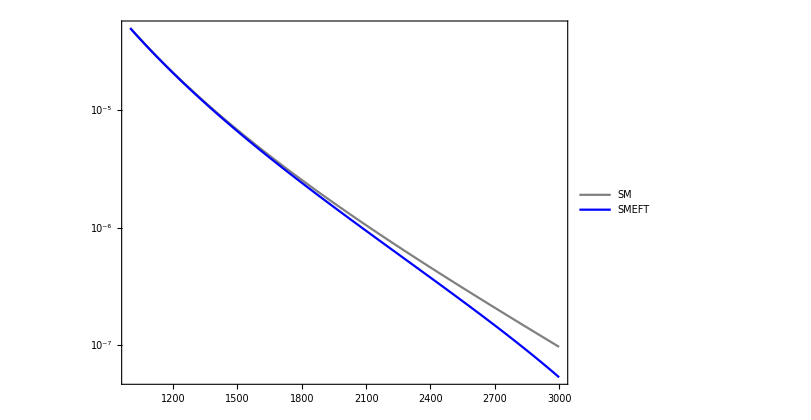

/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/pp2lnu_SMvsSMEFT.pdf

```mathematica
legend=Placed[LineLegend[{"SM","SMEFT"},LegendFunction->(Framed[#,Background->White]&),LegendMargins->5,LegendLayout->"Column"],{0.9,0.9}];
plot1=LogPlot[{dσdMudbarSMinterpol[M],dσdMudbarSMEFTinterpol[M]},{M,1000,3000},PlotStyle->{Gray,Blue},PlotLegends->legend]
Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/pp2lnu_SMvsSMEFT.pdf",plot1]
```

## 4. Dilepton Final State (Checked)

```mathematica
<<FeynCalc`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

### Definitions

```mathematica
SetOptions[{Plot,LogPlot,LogLogPlot,ListPlot,ListLogLogPlot},ImageSize->600,AspectRatio->0.7,Frame->True,FrameStyle->15,PlotStyle->{Thick},GridLines->Full];
SetOptions[{ListContourPlot},ImageSize->600,AspectRatio->0.7,Frame->True,FrameStyle->15,ContourLabels->True]; (*Plot with frames*)

Clear[Q,L,mz,e,θw,Mll];
$Assumptions=InM>0&&mz>0&&M>0;
FCClearScalarProducts[];

Definitions;

Sw=Sin[θw];Cw=Cos[θw];
(*g = e/Sw*)
PL=ChiralityProjector[-1];PR=ChiralityProjector[+1];

(*Chirality dependent*)
(* uLA, dLA, uLZ, dLZ, uRA, dRA, uRZ, dRZ, eLA, eLZ, eRA, eRZ *)
gL[x_]:=Switch[x,ν,νLZ,l,eLZ,u,uLZ,d,dLZ];
gR[x_]:=Switch[x,ν,νRZ,l,eRZ,u,uRZ,d,dRZ];
(* W depedning on *)
                                                         (* W^+ν̄ γ Subscript[P, L] e         W^-ē γ Subscript[P, L] ν             W^+ū γ Subscript[P, L] d             W^-ū γ Subscript[P, R] d            W^+d̄ γ Subscript[P, L] u           W^-d̄ γ Subscript[P, R] u *)
gwcoupling[x_]:=Switch[x,νbareL,νbareLWp*PL,ebarνL,ebarνLWm*PL,ubardL,ubardLWp*PL,ubardR,ubardRWp*PR,dbaruL,dbaruLWm*PL,dbaruR,dbaruRWm*PR];

Q[x_]:=Switch[x,ν,νLA*PL+νRA*PR,l,eLA*PL+eRA*PR,u,uLA*PL+uRA*PR,d,dLA*PL+dRA*PR];
(*MassReplace[x_]:=x/.{mz->91.1876,Γz->2.4952, α->1/127.91,mh->100};*)


Couplings;

(*Chirality dependent*)
gz[q_,μ_]:=ⅈ GA[μ].((gL[q])+(gR[q]));
gγ[q_,μ_]:=ⅈ Q[q] GA[μ]/.PL->1-PR//Simplify;
gw[q_,μ_]:=ⅈ GA[μ].gwcoupling[q];

Propagators;
lProp[p_,m_]:=(ⅈ(FV[p,α]GA[α]+m))/(SP[p]-m^2)//DiracSimplify;
ScalarProp[p_,m_]:=ⅈ/(SP[p]-m^2);
γProp[p_,x_,y_]:=(-ⅈ MT[x,y]/SP[p]);
zProp[p_,α_,β_,flag_]:=( -ⅈ/(SP[p]-mz^2+ⅈ Γz mz))(MT[α,β]-flag(FV[p,α]FV[p,β])/SP[p])//Normal; (*Flag=0 to exclude second part (EoM reducible)*)
wProp[p_,α_,β_,flag_]:=( -ⅈ/(SP[p]-mw^2+ⅈ Γw mw))(MT[α,β]-flag(FV[p,α]FV[p,β])/SP[p])//Normal;
RelFermDiagramSign=-1;

GeVtoPB = 1/(2.568*10^-9);
```

### Kinematics

```mathematica
SP[p1,p1]=mp1^2; SP[p2,p2]=mp2^2;
SP[p3,p3]=mp3^2; SP[p4,p4]=mp4^2;
SP[p1,p2] = 2 Ein^2; SP[p3,p4]=2 Ein^2-mp1^2;
SP[p1,p3]=Ein^2-Ein^2 Cθ;
SP[p1,p4]=Ein^2+Ein^2 Cθ;
SP[p2,p3]=Ein^2+Ein^2 Cθ ;
SP[p2,p4]=Ein^2-Ein^2 Cθ; (* Better for proton level calculation *)

mp1=0;
mp2=0;
mp3=0;
mp4=0;
```

### Amplitude q̄ q → e^+e^-

#### GeoSMEFT Amplitude

```mathematica
LLStruc= (SpinorVBar[p2,mp2].GA[μ].PL.SpinorU[p1,mp1])MT[μ,ν](SpinorUBar[p3,mp3].GA[ν].PL.SpinorV[p4,mp4])//DiracSimplify;
RLStruc=  (SpinorVBar[p2,mp2].GA[μ].PR.SpinorU[p1,mp1])MT[μ,ν](SpinorUBar[p3,mp3].GA[ν].PL.SpinorV[p4,mp4])//DiracSimplify;
LRStruc= (SpinorVBar[p2,mp2].GA[μ].PL.SpinorU[p1,mp1])MT[μ,ν](SpinorUBar[p3,mp3].GA[ν].PR.SpinorV[p4,mp4])//DiracSimplify;
RRStruc=  (SpinorVBar[p2,mp2].GA[μ].PR.SpinorU[p1,mp1])MT[μ,ν](SpinorUBar[p3,mp3].GA[ν].PR.SpinorV[p4,mp4])//DiracSimplify;

zPropOx=zProp[p1+p2,μ,ν,0]/.MT[μ,ν]->1;
γPropOx=γProp[p1+p2,μ,ν]/.MT[μ,ν]->1;
```

#### Contact Terms

```mathematica
(* Definitions *)
contactterms=ToExpression[Import["/Users/Tae/Desktop/GeoSMEFT/contact_terms.txt"]];

CuLeL=Coefficient[contactterms, edag σbarμ e udag σbarμ u];
CuReL=Coefficient[contactterms, edag σbarμ e uc σμ ucdag];
CuLeR=Coefficient[contactterms, ec σμ ecdag udag σbarμ u];
CuReR=Coefficient[contactterms, ec σμ ecdag uc σμ ucdag];
CdLeL=Coefficient[contactterms, edag σbarμ e ddag σbarμ d];
CdReL=Coefficient[contactterms, edag σbarμ e dc σμ dcdag];
CdLeR=Coefficient[contactterms, ec σμ ecdag ddag σbarμ d];
CdReR=Coefficient[contactterms, ec σμ ecdag dc σμ dcdag];
```

```mathematica
Cqe1[cont_]:=SeriesCoefficient[cont,{x,0,1}] x
Cqe2[cont_]:=Coefficient[SeriesCoefficient[cont,{x,0,2}] ,vT^-2] x^2 vT^-2
Cqes[cont_]:=Coefficient[SeriesCoefficient[cont,{x,0,2}] ,s] x^2
Cqet[cont_]:=Coefficient[SeriesCoefficient[cont,{x,0,2}] ,t] x^2
```

#### Decay Width of Z

```mathematica
Zdecaywidth=Series[ToExpression[Import["/Users/Tae/Desktop/GeoSMEFT/Partonic_cross-section/mW_scheme-Z_decay_width.txt"]],{x,0,2}];
Γz0val=SeriesCoefficient[Zdecaywidth//Expand,{x,0,0}];
Γz1val=SeriesCoefficient[Zdecaywidth//Expand,{x,0,1}];
Γz2val=SeriesCoefficient[Zdecaywidth//Expand,{x,0,2}]//Expand;
```

#### Amplitude Square GeoSMEFT

```mathematica
LLchiralSq=FermionSpinSum[Normal[Series[LLStruc*ComplexConjugate[(LLStruc)/.{ μ->ρ}],{x,0,2}]]]/.DiracTrace->Tr //Contract //Simplify;
RLchiralSq=FermionSpinSum[Normal[Series[RLStruc*ComplexConjugate[(RLStruc)/.{ μ->ρ}],{x,0,2}]]]/.DiracTrace->Tr //Contract //Simplify;
LRchiralSq=FermionSpinSum[Normal[Series[LRStruc*ComplexConjugate[(LRStruc)/.{ μ->ρ}],{x,0,2}]]]/.DiracTrace->Tr //Contract //Simplify;
RRchiralSq=FermionSpinSum[Normal[Series[RRStruc*ComplexConjugate[(RRStruc)/.{ μ->ρ}],{x,0,2}]]]/.DiracTrace->Tr //Contract //Simplify;
(* LLchiralSq = RRchiralSq *)
(* RLchiralSq = LRchiralSq *)
```

```mathematica
ampLLnostruc=1/ⅈ(ⅈ qLZ zPropOx ⅈ eLZ+ⅈ qLA γPropOx ⅈ eLA+(ⅈ CqLeL1 x+ⅈ CqLeL2 x^2+ⅈ CqLeLs s x^2+ⅈ CqLeLt t x^2))//.{s->2SP[p1,p2], t->-2SP[p1,p3],SP[p1+p2]->s}//Simplify;

ampLLnostrucSq[order_]:=SeriesCoefficient[ComplexExpand[ampLLnostruc*ComplexExpand[Conjugate[ampLLnostruc(*/.qLZ->qLZstar/.eLZ->eLZstar*)]]]/.Γz->Γz0+Γz1 x+Γz2 x^2,{x,0,order}]//Normal
```

```mathematica
str1=Coefficient[ampLLnostrucSq[0],eLZ^2 qLZ^2]//Simplify;
str2=Coefficient[ampLLnostrucSq[0],eLA^2 qLA^2]//Simplify;
str3=Coefficient[ampLLnostrucSq[0],eLA qLA eLZ qLZ]//Simplify;

str4=Coefficient[ampLLnostrucSq[1],CqLeL1 eLA qLA]//Simplify;
str5=Coefficient[ampLLnostrucSq[1],CqLeL1 eLZ qLZ]//Simplify;
str6=Coefficient[ampLLnostrucSq[1],Γz1 eLA qLA eLZ qLZ]//Simplify;
str7=Coefficient[ampLLnostrucSq[1],Γz1 eLZ^2 qLZ^2]//Simplify;

str8=Coefficient[ampLLnostrucSq[2],CqLeL1^2]//Simplify;
str9=Coefficient[ampLLnostrucSq[2],CqLeL1 Γz1 eLZ qLZ]//Simplify;
str10=Coefficient[ampLLnostrucSq[2], Γz1^2 eLA qLA eLZ qLZ]//Simplify;
str11=Coefficient[ampLLnostrucSq[2], Γz1^2 eLZ^2 qLZ^2]//Simplify;
str12=Coefficient[ampLLnostrucSq[2], Γz2 eLA qLA eLZ qLZ]//Simplify;
str13=Coefficient[ampLLnostrucSq[2], Γz2 eLZ^2 qLZ^2]//Simplify;
str14=Coefficient[ampLLnostrucSq[2],CqLeL2 eLA qLA]//Simplify;
str15=Coefficient[ampLLnostrucSq[2],CqLeL2 eLZ qLZ]//Simplify;
str16=Coefficient[ampLLnostrucSq[2],CqLeLs eLA qLA]//Simplify;
str17=Coefficient[ampLLnostrucSq[2],CqLeLs eLZ qLZ]//Simplify;
str18=Coefficient[ampLLnostrucSq[2],CqLeLt eLA qLA]//Simplify;
str19=Coefficient[ampLLnostrucSq[2],CqLeLt eLZ qLZ]//Simplify;
```

```mathematica
LLstructures={str1,str2,str3,str4,str5,str6,str7,str8,str9,str10,str11,str12,str13,str14,str15,str16,str17,str18,str19};
LLcouplings={eLZ^2 qLZ^2,eLA^2 qLA^2,eLA qLA eLZ qLZ,
CqLeL1 eLA qLA,CqLeL1 eLZ qLZ,Γz1 eLA qLA eLZ qLZ,Γz1 eLZ^2 qLZ^2,
CqLeL1^2,CqLeL1 Γz1 eLZ qLZ,Γz1^2 eLA qLA eLZ qLZ,Γz1^2 eLZ^2 qLZ^2,Γz2 eLA qLA eLZ qLZ,Γz2 eLZ^2 qLZ^2,CqLeL2 eLA qLA,CqLeL2 eLZ qLZ,CqLeLs eLA qLA,CqLeLs eLZ qLZ,CqLeLt eLA qLA,CqLeLt eLZ qLZ};
RLcouplings=LLcouplings/.{qLZ->qRZ,qLA->qRA,CqLeL1->CqReL1,CqLeL2->CqReL2, CqLeLs ->CqReLs,CqLeLt->CqReLt};
LRcouplings=LLcouplings/.{eLZ->eRZ,eLA->eRA,CqLeL1->CqLeR1,CqLeL2->CqLeR2, CqLeLs ->CqLeRs,CqLeLt->CqLeRt};
RRcouplings=LLcouplings/.{qLZ->qRZ,qLA->qRA,eLZ->eRZ,eLA->eRA,CqLeL1->CqReR1,CqLeL2->CqReR2, CqLeLs ->CqReRs,CqLeLt->CqReRt};
```

#### dσ/dΩ Parton level

```mathematica
qq2lldσdΩLL =1/(64 π^2  4 Ein^2)(*Phase Space*)1/3(*Color Av.*)1/4(*Spin Av.*) LLchiralSq LLstructures (* Same as RR *)/.{mz->91.1876,mw->80.387,Γz0->Γz0val};
qq2lldσdΩRL =1/(64 π^2  4 Ein^2)(*Phase Space*)1/3(*Color Av.*)1/4(*Spin Av.*) RLchiralSq LLstructures (* Same as LR *)/.{mz->91.1876,mw->80.387,Γz0->Γz0val};
```

```mathematica
qq2llσLL=2π Integrate[qq2lldσdΩLL,{Cθ,-1,1}]/.Ein->M/2//Simplify
qq2llσRL=2π Integrate[qq2lldσdΩRL,{Cθ,-1,1}]/.Ein->M/2//Simplify
```

{(0.00221049 M^2)/(M^4-16630.4 M^2+6.91919×10^7),1/(144 π M^2),(0.00442097 M^2-36.7612)/(M^4-16630.4 M^2+6.91919×10^7),1/(72 π),(0.00442097 M^2 (M^2-8315.18))/(M^4-16630.4 M^2+6.91919×10^7),(1.49426×10^6-179.703 M^2)/((M^4-16630.4 M^2+6.91919×10^7)^2),-(89.8516 M^2)/((M^4-16630.4 M^2+6.91919×10^7)^2),M^2/(144 π),-(179.703 M^2 (M^2-8315.18))/((M^4-16630.4 M^2+6.91919×10^7)^2),-(36.7612 (M^2-8315.18) (M^4-16630.4 M^2+6.89932×10^7))/((M^4-16630.4 M^2+6.91919×10^7)^3),(-18.3806 M^6+305676. M^4-1.26813×10^9 M^2)/((M^4-16630.4 M^2+6.91919×10^7)^3),(1.49426×10^6-179.703 M^2)/((M^4-16630.4 M^2+6.91919×10^7)^2),-(89.8516 M^2)/((M^4-16630.4 M^2+6.91919×10^7)^2),1/(72 π),(0.00442097 M^2 (M^2-8315.18))/(M^4-16630.4 M^2+6.91919×10^7),M^2/(72 π),(0.00442097 M^4 (M^2-8315.18))/(M^4-16630.4 M^2+6.91919×10^7),-M^2/(288 π),-(0.00110524 M^4 (M^2-8315.18))/(M^4-16630.4 M^2+6.91919×10^7)}

{(0.00221049 M^2)/(M^4-16630.4 M^2+6.91919×10^7),1/(144 π M^2),(0.00442097 M^2-36.7612)/(M^4-16630.4 M^2+6.91919×10^7),1/(72 π),(0.00442097 M^2 (M^2-8315.18))/(M^4-16630.4 M^2+6.91919×10^7),(1.49426×10^6-179.703 M^2)/((M^4-16630.4 M^2+6.91919×10^7)^2),-(89.8516 M^2)/((M^4-16630.4 M^2+6.91919×10^7)^2),M^2/(144 π),-(179.703 M^2 (M^2-8315.18))/((M^4-16630.4 M^2+6.91919×10^7)^2),-(36.7612 (M^2-8315.18) (M^4-16630.4 M^2+6.89932×10^7))/((M^4-16630.4 M^2+6.91919×10^7)^3),(-18.3806 M^6+305676. M^4-1.26813×10^9 M^2)/((M^4-16630.4 M^2+6.91919×10^7)^3),(1.49426×10^6-179.703 M^2)/((M^4-16630.4 M^2+6.91919×10^7)^2),-(89.8516 M^2)/((M^4-16630.4 M^2+6.91919×10^7)^2),1/(72 π),(0.00442097 M^2 (M^2-8315.18))/(M^4-16630.4 M^2+6.91919×10^7),M^2/(72 π),(0.00442097 M^4 (M^2-8315.18))/(M^4-16630.4 M^2+6.91919×10^7),-M^2/(96 π),-(0.00331573 M^4 (M^2-8315.18))/(M^4-16630.4 M^2+6.91919×10^7)}

### PDF Apply based on Helicity Structure

```mathematica
SetDirectory["~/Google\ Drive/Research/Instruction/Tools/Cuba-4.2.1"];
Install["Vegas"];
```

```mathematica
pdfpath="~/Google\ Drive/Research/Instruction/Tools/math_package_v2";
SetDirectory[pdfpath];
<< NNPDF`
prefix=pdfpath<>"/Grids/";
namegrid = "NNPDF30_nlo_as_0118";
Timing[InitializePDFGrid[prefix,namegrid]]
```

Welcome in the Mathematica Package for NNPDF PDFs. The following Functions are available:

- Initializing and interpolating PDFs

InitializePDFGrid;

- Using NNPDF PDFs

xPDFcv; xPDFEnsemble; xPDFRep; xPDF; xPDFCL; xMin; xMax; Q2min; Q2Max; NumberPDF; HasPhoton;

- Parameters for the QCD analysis

alphaSMZ; mCharm; mBottom; mTop; MZ; alphas; Infoalphas; Lam4; Lam5;

For the usage of each of these Functions, please read the README file or type ?Function.

'Version' '5.8.8'

'Description:'

'NNPDF30_nlo_as_0118.LHgrid'

'Reference: arXiv:1410.8849'

'Fit: NLO global fit, alphas(MZ)=0.118'

'NNPDF Collaboration: R.D. Ball, V. Bertone, '

'S. Carrazza, C.S. Deans, L. Del Debbio, '

'S. Forte, A. Guffanti, N.P. Hartland, '

'J.I. Latorre, J. Rojo and M. Ubiali'

'This set has 100 member PDF'

'mem=0 --> average on replicas.'

'Evolution: pol. interpolation on the LH grid'

Grid division:

x axis: 100 points; 1.×10^-9 <= x <= 1.

Q^2 axis: 50 points; 1. <= Q^2 <= 1.×10^10

Reading PDF set from file. Please wait.

PDF set successfully read from file.

Interpolating PDF set on the grid. Please wait.

PDF grid interpolated. Ready to use the NNPDF set.

{12.5326,Null}

```mathematica
Definitions;

ecoll=13000;
scoll=ecoll^2;


(*pdf[x_,Q_,flav_]:=If[x≤1.0&&x>10^-9&&xPDFcv[x,Q^2,flav]>0,1/x xPDFcv[x,Q^2,flav],0]*)
pdf[x_,flav_]:=xPDFcv[x,mz^2,flav]/.mz->91.1876/.mw->80.387

(* remember: quarkID = 2 (up), 1 (down),   gluon = 0,    3 (strange),  4(charm)  *)

uubarpdf=2/M(pdf[M/(√scoll)Exp[Y],2]pdf[M/(√scoll)Exp[-Y],-2]+pdf[M/(√scoll)Exp[Y],-2]pdf[M/(√scoll)Exp[-Y], 2]);
ddbarpdf=2/M(pdf[M/(√scoll)Exp[Y],1]pdf[M/(√scoll)Exp[-Y],-1]+pdf[M/(√scoll)Exp[Y],-1]pdf[M/(√scoll)Exp[-Y], 1]);
ccbarpdf=2/M(pdf[M/(√scoll)Exp[Y],4]pdf[M/(√scoll)Exp[-Y],-4]+pdf[M/(√scoll)Exp[Y],-4]pdf[M/(√scoll)Exp[-Y], 4]);
ssbarpdf=2/M(pdf[M/(√scoll)Exp[Y],3]pdf[M/(√scoll)Exp[-Y],-3]+pdf[M/(√scoll)Exp[Y],-3]pdf[M/(√scoll)Exp[-Y], 3]);
```

```mathematica
σpp2llOxuubar={};
σpp2llOxddbar={};
σpp2llOxccbar={};
σpp2llOxssbar={};
Monitor[Do[
protonσuu=1/10^5 Vegas[10^5 GeVtoPB qq2llσLL[[i]]uubarpdf,{M,1,13000}, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]},MaxPoints-> 5000000,NStart-> 100000, NIncrease-> 50000,PrecisionGoal -> 3,AccuracyGoal-> 3, Verbose->0];
protonσdd=1/10^5 Vegas[10^5 GeVtoPB qq2llσLL[[i]]ddbarpdf,{M,1,13000}, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]},MaxPoints-> 5000000,NStart-> 100000, NIncrease-> 50000,PrecisionGoal -> 3,AccuracyGoal-> 3, Verbose->0];
protonσcc=1/10^5 Vegas[10^5 GeVtoPB qq2llσLL[[i]]ccbarpdf,{M,1,13000}, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]},MaxPoints-> 5000000,NStart-> 100000, NIncrease-> 50000,PrecisionGoal -> 3,AccuracyGoal-> 3, Verbose->0];
protonσss=1/10^5 Vegas[10^5 GeVtoPB qq2llσLL[[i]]ssbarpdf,{M,1,13000}, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]},MaxPoints-> 5000000,NStart-> 100000, NIncrease-> 50000,PrecisionGoal -> 3,AccuracyGoal-> 3, Verbose->0];
AppendTo[σpp2llOxuubar,{LLcouplings[[i]],protonσuu}];
AppendTo[σpp2llOxddbar,{LLcouplings[[i]],protonσdd}];
AppendTo[σpp2llOxccbar,{LLcouplings[[i]],protonσcc}];
AppendTo[σpp2llOxssbar,{LLcouplings[[i]],protonσss}];
,{i,1,Length[qq2llσLL]}],i];
σpp2llOxuubar
σpp2llOxddbar
σpp2llOxccbar
σpp2llOxssbar
```

Vegas::success: Needed 1000000 function evaluations.

General::stop: Further output of Vegas::success will be suppressed during this calculation.

Vegas::accuracy: Desired accuracy was not reached within 5200000 function evaluations.

General::stop: Further output of Vegas::accuracy will be suppressed during this calculation.

(eLZ^2 qLZ^2 | (114615. | 60.898 | 4.43501×10^-9)
eLA^2 qLA^2 | (2.72243×10^8 | 149456. | 2.35593×10^-6)
eLA eLZ qLA qLZ | (-222817. | 163.095 | 3.98918×10^-8)
CqLeL1 eLA qLA | (1.8566×10^9 | 1.02518×10^6 | 4.11822×10^-8)
CqLeL1 eLZ qLZ | (1.09414×10^6 | 72335.3 | 3.33067×10^-21)
Γz1 eLA eLZ qLA qLZ | (230.08 | 0.831207 | 4.86211×10^-17)
Γz1 eLZ^2 qLZ^2 | (-46993.9 | 22.7438 | 1.30649×10^-7)
CqLeL1^2 | (2.27813×10^12 | 1.66798×10^9 | 4.43706×10^-9)
CqLeL1 Γz1 eLZ qLZ | (266373. | 6389.48 | 2.17115×10^-17)
Γz1^2 eLA eLZ qLA qLZ | (26.4872 | 0.211812 | 1.47993×10^-17)
Γz1^2 eLZ^2 qLZ^2 | (19237. | 11.9771 | 1.98986×10^-8)
Γz2 eLA eLZ qLA qLZ | (230.08 | 0.831207 | 4.86211×10^-17)
Γz2 eLZ^2 qLZ^2 | (-46993.9 | 22.7438 | 1.30649×10^-7)
CqLeL2 eLA qLA | (1.8566×10^9 | 1.02518×10^6 | 4.11822×10^-8)
CqLeL2 eLZ qLZ | (1.09414×10^6 | 72335.3 | 3.33067×10^-21)
CqLeLs eLA qLA | (4.55627×10^12 | 3.33596×10^9 | 4.43706×10^-9)
CqLeLs eLZ qLZ | (4.55407×10^12 | 3.92098×10^9 | 3.33585×10^-10)
CqLeLt eLA qLA | (-1.13907×10^12 | 8.3399×10^8 | 4.43706×10^-9)
CqLeLt eLZ qLZ | (-1.13852×10^12 | 9.80244×10^8 | 3.33585×10^-10))

(eLZ^2 qLZ^2 | (83464.1 | 44.7793 | 3.44426×10^-9)
eLA^2 qLA^2 | (2.34089×10^8 | 131891. | 1.061×10^-6)
eLA eLZ qLA qLZ | (-187587. | 132.509 | 1.30696×10^-8)
CqLeL1 eLA qLA | (1.55969×10^9 | 835582. | 1.55496×10^-8)
CqLeL1 eLZ qLZ | (-2.30064×10^6 | 52555.7 | 7.77156×10^-21)
Γz1 eLA eLZ qLA qLZ | (184.236 | 0.609463 | 2.22157×10^-16)
Γz1 eLZ^2 qLZ^2 | (-34190.1 | 16.4159 | 8.47853×10^-8)
CqLeL1^2 | (1.32197×10^12 | 9.87212×10^8 | 4.35104×10^-9)
CqLeL1 Γz1 eLZ qLZ | (208806. | 4611.95 | 3.67228×10^-17)
Γz1^2 eLA eLZ qLA qLZ | (22.3526 | 0.156402 | 9.17733×10^-17)
Γz1^2 eLZ^2 qLZ^2 | (13994.8 | 8.96311 | 8.94587×10^-9)
Γz2 eLA eLZ qLA qLZ | (184.236 | 0.609463 | 2.22157×10^-16)
Γz2 eLZ^2 qLZ^2 | (-34190.1 | 16.4159 | 8.47853×10^-8)
CqLeL2 eLA qLA | (1.55969×10^9 | 835582. | 1.55496×10^-8)
CqLeL2 eLZ qLZ | (-2.30064×10^6 | 52555.7 | 7.77156×10^-21)
CqLeLs eLA qLA | (2.64393×10^12 | 1.97442×10^9 | 4.35104×10^-9)
CqLeLs eLZ qLZ | (2.61655×10^12 | 2.52256×10^9 | 3.72703×10^-10)
CqLeLt eLA qLA | (-6.60983×10^11 | 4.93606×10^8 | 4.35104×10^-9)
CqLeLt eLZ qLZ | (-6.54136×10^11 | 6.30641×10^8 | 3.72703×10^-10))

(eLZ^2 qLZ^2 | (20038.9 | 10.2202 | 1.17795×10^-9)
eLA^2 qLA^2 | (1.28787×10^8 | 73537.2 | 2.60875×10^-7)
eLA eLZ qLA qLZ | (-94999.4 | 60.062 | 1.7896×10^-9)
CqLeL1 eLA qLA | (7.85867×10^8 | 440514. | 1.90137×10^-9)
CqLeL1 eLZ qLZ | (-4.89867×10^6 | 12569.3 | 1.11022×10^-21)
Γz1 eLA eLZ qLA qLZ | (76.2254 | 0.157076 | 1.03222×10^-15)
Γz1 eLZ^2 qLZ^2 | (-8150.36 | 4.0462 | 1.14679×10^-7)
CqLeL1^2 | (1.08608×10^11 | 9.97701×10^7 | 4.98529×10^-10)
CqLeL1 Γz1 eLZ qLZ | (71379.5 | 1113. | 5.12928×10^-15)
Γz1^2 eLA eLZ qLA qLZ | (11.4071 | 0.039821 | 6.85717×10^-14)
Γz1^2 eLZ^2 qLZ^2 | (3336.04 | 2.09445 | 1.18556×10^-8)
Γz2 eLA eLZ qLA qLZ | (76.2254 | 0.157076 | 1.03222×10^-15)
Γz2 eLZ^2 qLZ^2 | (-8150.36 | 4.0462 | 1.14679×10^-7)
CqLeL2 eLA qLA | (7.85867×10^8 | 440514. | 1.90137×10^-9)
CqLeL2 eLZ qLZ | (-4.89867×10^6 | 12569.3 | 1.11022×10^-21)
CqLeLs eLA qLA | (2.17216×10^11 | 1.9954×10^8 | 4.98529×10^-10)
CqLeLs eLZ qLZ | (1.74496×10^11 | 1.66336×10^8 | 6.04475×10^-18)
CqLeLt eLA qLA | (-5.43041×10^10 | 4.9885×10^7 | 4.98529×10^-10)
CqLeLt eLZ qLZ | (-4.3624×10^10 | 4.1584×10^7 | 6.04492×10^-18))

(eLZ^2 qLZ^2 | (31154. | 15.6958 | 5.98948×10^-10)
eLA^2 qLA^2 | (1.65018×10^8 | 91325.1 | 2.94233×10^-7)
eLA eLZ qLA qLZ | (-124210. | 78.327 | 3.36327×10^-9)
CqLeL1 eLA qLA | (1.02777×10^9 | 566226. | 3.55563×10^-9)
CqLeL1 eLZ qLZ | (-6.18783×10^6 | 19327.8 | 2.33147×10^-20)
Γz1 eLA eLZ qLA qLZ | (103.855 | 0.238672 | 3.05326×10^-15)
Γz1 eLZ^2 qLZ^2 | (-12695.2 | 6.42895 | 4.43847×10^-8)
CqLeL1^2 | (2.07915×10^11 | 1.71281×10^8 | 5.54165×10^-9)
CqLeL1 Γz1 eLZ qLZ | (104128. | 1725.09 | 7.04195×10^-15)
Γz1^2 eLA eLZ qLA qLZ | (14.899 | 0.0602058 | 1.61956×10^-14)
Γz1^2 eLZ^2 qLZ^2 | (5195.86 | 3.37284 | 2.14587×10^-8)
Γz2 eLA eLZ qLA qLZ | (103.855 | 0.238672 | 3.05326×10^-15)
Γz2 eLZ^2 qLZ^2 | (-12695.2 | 6.42895 | 4.43847×10^-8)
CqLeL2 eLA qLA | (1.02777×10^9 | 566226. | 3.55563×10^-9)
CqLeL2 eLZ qLZ | (-6.18783×10^6 | 19327.8 | 2.33147×10^-20)
CqLeLs eLA qLA | (4.15831×10^11 | 3.42562×10^8 | 5.54165×10^-9)
CqLeLs eLZ qLZ | (3.61309×10^11 | 3.58137×10^8 | 5.37414×10^-14)
CqLeLt eLA qLA | (-1.03958×10^11 | 8.56404×10^7 | 5.54165×10^-9)
CqLeLt eLZ qLZ | (-9.03274×10^10 | 8.95342×10^7 | 5.37414×10^-14))

```mathematica
(* In RL/LR mode, 3 is multiplied (/.CqReLt->3CqReLt) since the integral is evaluated on LL. For RL(LR), terms with CqReLt(CqLeRt) is off by factor of 3 *)

uu2llOx0=SeriesCoefficient[ZinvolveCoupling[Sum[LLcouplings[[i]]σpp2llOxuubar[[i,2,1,1]]+RRcouplings[[i]]σpp2llOxuubar[[i,2,1,1]]+(RLcouplings[[i]]/.CqReLt->3CqReLt)σpp2llOxuubar[[i,2,1,1]]+(LRcouplings[[i]]/.CqLeRt->3CqLeRt )σpp2llOxuubar[[i,2,1,1]],{i,1,19}]//.{qLA->uLAval,qRA->uRAval,qLZ->uLZval,qRZ->uRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CuLeL],CqLeL2->Cqe2[CuLeL],CqLeLs->Cqes[CuLeL],CqLeLt->Cqet[CuLeL],
CqLeR1->Cqe1[CuLeR],CqLeR2->Cqe2[CuLeR],CqLeRs->Cqes[CuLeR],CqLeRt->Cqet[CuLeR],
CqReL1->Cqe1[CuReL],CqReL2->Cqe2[CuReL],CqReLs->Cqes[CuReL],CqReLt->Cqet[CuReL],
CqReR1->Cqe1[CuReR],CqReR2->Cqe2[CuReR],CqReRs->Cqes[CuReR],CqReRt->Cqet[CuReR]}/.vT2vhat],{x,0,0}]
uu2llOx1=SeriesCoefficient[ZinvolveCoupling[Sum[LLcouplings[[i]]σpp2llOxuubar[[i,2,1,1]]+RRcouplings[[i]]σpp2llOxuubar[[i,2,1,1]]+(RLcouplings[[i]]/.CqReLt->3CqReLt)σpp2llOxuubar[[i,2,1,1]]+(LRcouplings[[i]]/.CqLeRt->3CqLeRt)σpp2llOxuubar[[i,2,1,1]],{i,1,19}]//.{qLA->uLAval,qRA->uRAval,qLZ->uLZval,qRZ->uRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CuLeL],CqLeL2->Cqe2[CuLeL],CqLeLs->Cqes[CuLeL],CqLeLt->Cqet[CuLeL],
CqLeR1->Cqe1[CuLeR],CqLeR2->Cqe2[CuLeR],CqLeRs->Cqes[CuLeR],CqLeRt->Cqet[CuLeR],
CqReL1->Cqe1[CuReL],CqReL2->Cqe2[CuReL],CqReLs->Cqes[CuReL],CqReLt->Cqet[CuReL],
CqReR1->Cqe1[CuReR],CqReR2->Cqe2[CuReR],CqReRs->Cqes[CuReR],CqReRt->Cqet[CuReR]}/.vT2vhat],{x,0,1}]//Expand
uu2llOx2=SeriesCoefficient[ZinvolveCoupling[Sum[LLcouplings[[i]]σpp2llOxuubar[[i,2,1,1]]+RRcouplings[[i]]σpp2llOxuubar[[i,2,1,1]]+(RLcouplings[[i]]/.CqReLt->3CqReLt)σpp2llOxuubar[[i,2,1,1]]+(LRcouplings[[i]]/.CqLeRt->3CqLeRt)σpp2llOxuubar[[i,2,1,1]],{i,1,19}]//.{qLA->uLAval,qRA->uRAval,qLZ->uLZval,qRZ->uRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CuLeL],CqLeL2->Cqe2[CuLeL],CqLeLs->Cqes[CuLeL],CqLeLt->Cqet[CuLeL],
CqLeR1->Cqe1[CuLeR],CqLeR2->Cqe2[CuLeR],CqLeRs->Cqes[CuLeR],CqLeRt->Cqet[CuLeR],
CqReL1->Cqe1[CuReL],CqReL2->Cqe2[CuReL],CqReLs->Cqes[CuReL],CqReLt->Cqet[CuReL],
CqReR1->Cqe1[CuReR],CqReR2->Cqe2[CuReR],CqReRs->Cqes[CuReR],CqReRt->Cqet[CuReR]}/.vT2vhat],{x,0,2}]//Expand
```

4.37039×10^6

-1939.2 CeQ6til-1940.31 Ceu6til-1.52394×10^7 CHD6til+115.495 CHdc16til-1789.21 CHec16til+721.934 CHL16til+203.689 CHL36til-1620.82 CHQ16til+297.072 CHQ36til+704.449 CHuc16til-3.26416×10^7 CHWB6til+1940.94 CLQ36til-1940.94 CLQ6til-1939.57 CLu6til-1.23604×10^7 δGF6

619.852 CeQ6til^2+3381.3 CeQ6til CHD6til-0.0837544 CeQ6til CHdc16til-1.82364 CeQ6til CHec16til-0.0837544 CeQ6til CHL16til+0.292064 CeQ6til CHL36til-0.887522 CeQ6til CHQ16til+1.84747 CeQ6til CHQ36til+0.111673 CeQ6til CHuc16til+7244.78 CeQ6til CHWB6til+5484.25 CeQ6til δGF6+12.6443 CeQs8til-9.48324 CeQt8til+619.852 Ceu6til^2+3383.82 Ceu6til CHD6til+0.0354087 Ceu6til CHdc16til+0.770975 Ceu6til CHec16til+0.0354087 Ceu6til CHL16til-0.123475 Ceu6til CHL36til-0.0912449 Ceu6til CHQ16til-0.31459 Ceu6til CHQ36til-1.15056 Ceu6til CHuc16til+7246.54 Ceu6til CHWB6til+5488.29 Ceu6til δGF6+50.5203 Ceus8til-12.6301 Ceut8til-3.26416×10^7 CHB6til CHWB6til-1.30544×10^7 CHD28til+1.32863×10^7 CHD6til^2-236.626 CHD6til CHdc16til+1701.32 CHD6til CHec16til+1184.38 CHD6til CHL16til+1342.56 CHD6til CHL36til+2476.42 CHD6til CHQ16til-2475.14 CHD6til CHQ36til+1337.5 CHD6til CHuc16til+7.72133×10^7 CHD6til CHWB6til-3380.96 CHD6til CLQ36til+3380.96 CHD6til CLQ6til+3382.14 CHD6til CLu6til+4.31038×10^7 CHD6til δGF6-2.18503×10^6 CHD8til-367.701 CHdc16til^2-161.978 CHdc16til CHec16til+294.776 CHdc16til CHL16til+106.472 CHdc16til CHL36til-386.952 CHdc16til CHQ16til-94.031 CHdc16til CHQ36til+62.0557 CHdc16til CHuc16til-191.607 CHdc16til CHWB6til-0.104155 CHdc16til CLQ36til+0.104155 CHdc16til CLQ6til-0.0440334 CHdc16til CLu6til-163.019 CHdc16til δGF6+57.7477 CHdc18til+943.049 CHec16til^2+90.8335 CHec16til CHL16til+817.652 CHec16til CHL36til+4776.52 CHec16til CHQ16til-2920.02 CHec16til CHQ36til+1127.65 CHec16til CHuc16til+2333.07 CHec16til CHWB6til-0.104155 CHec16til CLQ36til+0.104155 CHec16til CLQ6til-0.0440334 CHec16til CLu6til+3635.2 CHec16til δGF6-894.603 CHec18til-969.602 CHeQ18til+969.602 CHeQ38til-970.154 CHeu8til+1270.24 CHL16til^2+1736.02 CHL16til CHL36til-2462.54 CHL16til CHQ16til-916.021 CHL16til CHQ36til+3081.48 CHL16til CHuc16til+3121.24 CHL16til CHWB6til+1.63573 CHL16til CLQ36til-1.63573 CHL16til CLQ6til+0.691533 CHL16til CLu6til+91.5787 CHL16til δGF6+360.967 CHL18til+101.844 CHL28til+370.01 CHL36til^2-726.233 CHL36til CHQ16til-494.09 CHL36til CHQ36til+2803.03 CHL36til CHuc16til+3013.25 CHL36til CHWB6til+2.10308 CHL36til CLQ36til-2.10308 CHL36til CLQ6til+0.889117 CHL36til CLu6til+823.068 CHL36til δGF6+101.844 CHL38til-970.472 CHLQ18til+970.472 CHLQ28til-970.472 CHLQ38til+970.472 CHLQ48til-969.786 CHLu18til-969.786 CHLu38til+1300.82 CHQ16til^2+278.658 CHQ16til CHQ36til+211.836 CHQ16til CHuc16til+1393.39 CHQ16til CHWB6til-1.1037 CHQ16til CLQ36til+1.1037 CHQ16til CLQ6til+0.11347 CHQ16til CLu6til+1990.19 CHQ16til δGF6-810.408 CHQ18til+148.536 CHQ28til-377.831 CHQ36til^2-923.085 CHQ36til CHuc16til-2100.59 CHQ36til CHWB6til+2.29747 CHQ36til CLQ36til-2.29747 CHQ36til CLQ6til+0.391216 CHQ36til CLu6til-121.764 CHQ36til δGF6+148.536 CHQ38til+711.653 CHuc16til^2+1416.23 CHuc16til CHWB6til+0.138873 CHuc16til CLQ36til-0.138873 CHuc16til CLQ6til+1.43081 CHuc16til CLu6til-1291.17 CHuc16til δGF6+352.224 CHuc18til-2.17388×10^7 CHW28til-3.26416×10^7 CHW6til CHWB6til+9.14336×10^7 CHWB6til^2-7242.93 CHWB6til CLQ36til+7242.93 CHWB6til CLQ6til+7245.37 CHWB6til CLu6til+9.23249×10^7 CHWB6til δGF6-4.94717×10^11 CHWB8til+619.852 CLQ36til^2-1239.7 CLQ36til CLQ6til-5490.63 CLQ36til δGF6+619.852 CLQ6til^2+5490.63 CLQ6til δGF6+72.3713 CLQs18til-72.3713 CLQs38til-18.0929 CLQt18til+18.0929 CLQt38til+619.852 CLu6til^2+5485.59 CLu6til δGF6+25.2696 CLus8til-18.9523 CLut8til+2.62198×10^7 δGF6^2-1.23604×10^7 δGF8

```mathematica
dd2llOx0=SeriesCoefficient[ZinvolveCoupling[Sum[LLcouplings[[i]]σpp2llOxddbar[[i,2,1,1]]+RRcouplings[[i]]σpp2llOxddbar[[i,2,1,1]]+(RLcouplings[[i]]/.CqReLt->3CqReLt)σpp2llOxddbar[[i,2,1,1]]+(LRcouplings[[i]]/.CqLeRt->3CqLeRt)σpp2llOxddbar[[i,2,1,1]],{i,1,19}]//.{qLA->dLAval,qRA->dRAval,qLZ->dLZval,qRZ->dRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CdLeL],CqLeL2->Cqe2[CdLeL],CqLeLs->Cqes[CdLeL],CqLeLt->Cqet[CdLeL],
CqLeR1->Cqe1[CdLeR],CqLeR2->Cqe2[CdLeR],CqLeRs->Cqes[CdLeR],CqLeRt->Cqet[CdLeR],
CqReL1->Cqe1[CdReL],CqReL2->Cqe2[CdReL],CqReLs->Cqes[CdReL],CqReLt->Cqet[CdReL],
CqReR1->Cqe1[CdReR],CqReR2->Cqe2[CdReR],CqReRs->Cqes[CdReR],CqReRt->Cqet[CdReR]}/.vT2vhat],{x,0,0}]
dd2llOx1=SeriesCoefficient[ZinvolveCoupling[Sum[LLcouplings[[i]]σpp2llOxddbar[[i,2,1,1]]+RRcouplings[[i]]σpp2llOxddbar[[i,2,1,1]]+(RLcouplings[[i]]/.CqReLt->3CqReLt)σpp2llOxddbar[[i,2,1,1]]+(LRcouplings[[i]]/.CqLeRt->3CqLeRt)σpp2llOxddbar[[i,2,1,1]],{i,1,19}]//.{qLA->dLAval,qRA->dRAval,qLZ->dLZval,qRZ->dRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CdLeL],CqLeL2->Cqe2[CdLeL],CqLeLs->Cqes[CdLeL],CqLeLt->Cqet[CdLeL],
CqLeR1->Cqe1[CdLeR],CqLeR2->Cqe2[CdLeR],CqLeRs->Cqes[CdLeR],CqLeRt->Cqet[CdLeR],
CqReL1->Cqe1[CdReL],CqReL2->Cqe2[CdReL],CqReLs->Cqes[CdReL],CqReLt->Cqet[CdReL],
CqReR1->Cqe1[CdReR],CqReR2->Cqe2[CdReR],CqReRs->Cqes[CdReR],CqReRt->Cqet[CdReR]}/.vT2vhat],{x,0,1}]//Expand
dd2llOx2=SeriesCoefficient[ZinvolveCoupling[Sum[LLcouplings[[i]]σpp2llOxddbar[[i,2,1,1]]+RRcouplings[[i]]σpp2llOxddbar[[i,2,1,1]]+(RLcouplings[[i]]/.CqReLt->3CqReLt)σpp2llOxddbar[[i,2,1,1]]+(LRcouplings[[i]]/.CqLeRt->3CqLeRt)σpp2llOxddbar[[i,2,1,1]],{i,1,19}]//.{qLA->dLAval,qRA->dRAval,qLZ->dLZval,qRZ->dRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CdLeL],CqLeL2->Cqe2[CdLeL],CqLeLs->Cqes[CdLeL],CqLeLt->Cqet[CdLeL],
CqLeR1->Cqe1[CdLeR],CqLeR2->Cqe2[CdLeR],CqLeRs->Cqes[CdLeR],CqLeRt->Cqet[CdLeR],
CqReL1->Cqe1[CdReL],CqReL2->Cqe2[CdReL],CqReLs->Cqes[CdReL],CqReLt->Cqet[CdReL],
CqReR1->Cqe1[CdReR],CqReR2->Cqe2[CdReR],CqReRs->Cqes[CdReR],CqReRt->Cqet[CdReR]}/.vT2vhat],{x,0,2}]//Expand
```

939886.

814.521 Ced6til+816.841 CeQ6til-3.27653×10^6 CHD6til-216.706 CHdc16til-1510.57 CHec16til+835.299 CHL16til+351.566 CHL36til+986.385 CHQ16til+306.395 CHQ36til-143.739 CHuc16til-7.01709×10^6 CHWB6til+815.295 CLd6til+812.41 CLQ36til+812.41 CLQ6til-2.65756×10^6 δGF6

359.691 Ced6til^2-1419.41 Ced6til CHD6til+2.30613 Ced6til CHdc16til+0.759458 Ced6til CHec16til-0.0138782 Ced6til CHL16til+0.0483953 Ced6til CHL36til+0.0357628 Ced6til CHQ16til+0.123301 Ced6til CHQ36til+0.0185043 Ced6til CHuc16til-3042.03 Ced6til CHWB6til-2303.92 Ced6til δGF6-14.6258 Ceds8til+3.65645 Cedt8til+359.691 CeQ6til^2-1424.58 CeQ6til CHD6til+0.0795321 CeQ6til CHdc16til-4.35224 CeQ6til CHec16til+0.0795321 CeQ6til CHL16til-0.27734 CeQ6til CHL36til+2.11506 CeQ6til CHQ16til+1.6134 CeQ6til CHQ36til-0.106043 CeQ6til CHuc16til-3046.59 CeQ6til CHWB6til-2309.76 CeQ6til δGF6+7.1359 CeQs8til-5.35192 CeQt8til-7.01709×10^6 CHB6til CHWB6til-2.80674×10^6 CHD28til+2.85829×10^6 CHD6til^2-762.297 CHD6til CHdc16til+2900.35 CHD6til CHec16til+1867.22 CHD6til CHL16til+2127.5 CHD6til CHL36til-1248.4 CHD6til CHQ16til-1383.77 CHD6til CHQ36til+327.96 CHD6til CHuc16til+1.66037×10^7 CHD6til CHWB6til-1421.13 CHD6til CLd6til-1423.78 CHD6til CLQ36til-1423.78 CHD6til CLQ6til+9.26734×10^6 CHD6til δGF6-469795. CHD8til+408.198 CHdc16til^2-593.043 CHdc16til CHec16til-1099.89 CHdc16til CHL16til-1082.98 CHdc16til CHL36til+255.482 CHdc16til CHQ16til+279.25 CHdc16til CHQ36til+5.02424 CHdc16til CHuc16til-767.018 CHdc16til CHWB6til-2.86785 CHdc16til CLd6til-0.0989042 CHdc16til CLQ36til-0.0989042 CHdc16til CLQ6til+431.119 CHdc16til δGF6-108.353 CHdc18til+881.325 CHec16til^2+84.9463 CHec16til CHL16til+762.934 CHec16til CHL36til-2563.33 CHec16til CHQ16til-1610.27 CHec16til CHQ36til+201.46 CHec16til CHuc16til+3368.4 CHec16til CHWB6til+0.0172586 CHec16til CLd6til-0.0989042 CHec16til CLQ36til-0.0989042 CHec16til CLQ6til+2942.78 CHec16til δGF6-755.286 CHec18til+407.261 CHed8til+408.421 CHeQ18til+408.421 CHeQ38til+1186.69 CHL16til^2+1622.23 CHL16til CHL36til+1685.75 CHL16til CHQ16til-50.1482 CHL16til CHQ36til-366.94 CHL16til CHuc16til+3516.59 CHL16til CHWB6til+0.790595 CHL16til CLd6til-4.53068 CHL16til CLQ36til-4.53068 CHL16til CLQ6til-370.685 CHL16til δGF6+417.65 CHL18til+175.783 CHL28til+346.077 CHL36til^2+1035.78 CHL36til CHQ16til+408.351 CHL36til CHQ36til-132.629 CHL36til CHuc16til+3536.42 CHL36til CHWB6til+0.713153 CHL36til CLd6til-4.08688 CHL36til CLQ36til-4.08688 CHL36til CLQ6til+312.333 CHL36til δGF6+175.783 CHL38til+407.647 CHLd18til+407.647 CHLd38til+406.205 CHLQ18til+406.205 CHLQ28til+406.205 CHLQ38til+406.205 CHLQ48til-313.618 CHQ16til^2-573.432 CHQ16til CHQ36til-193.134 CHQ16til CHuc16til-644.338 CHQ16til CHWB6til-0.0444738 CHQ16til CLd6til-2.63024 CHQ16til CLQ36til-2.63024 CHQ16til CLQ6til-1268.39 CHQ16til δGF6+493.192 CHQ18til+153.197 CHQ28til-448.191 CHQ36til^2+136.241 CHQ36til CHuc16til-1153.29 CHQ36til CHWB6til-0.153335 CHQ36til CLd6til-2.00639 CHQ36til CLQ36til-2.00639 CHQ36til CLQ6til-308.268 CHQ36til δGF6+153.197 CHQ38til-207.055 CHuc16til^2+274.311 CHuc16til CHWB6til-0.0230114 CHuc16til CLd6til+0.131872 CHuc16til CLQ36til+0.131872 CHuc16til CLQ6til+202.955 CHuc16til δGF6-71.8695 CHuc18til-4.67389×10^6 CHW28til-7.01709×10^6 CHW6til CHWB6til+1.96582×10^7 CHWB6til^2-3043.55 CHWB6til CLd6til-3047.59 CHWB6til CLQ36til-3047.59 CHWB6til CLQ6til+1.98477×10^7 CHWB6til δGF6-1.06351×10^11 CHWB8til+359.691 CLd6til^2-2305.87 CLd6til δGF6-7.37191 CLds8til+5.52893 CLdt8til+359.691 CLQ36til^2+719.382 CLQ36til CLQ6til-2298.61 CLQ36til δGF6+359.691 CLQ6til^2-2298.61 CLQ6til δGF6-34.4342 CLQs18til-34.4342 CLQs38til+8.60856 CLQt18til+8.60856 CLQt38til+5.63694×10^6 δGF6^2-2.65756×10^6 δGF8

```mathematica
cc2llOx0=SeriesCoefficient[ZinvolveCoupling[Sum[LLcouplings[[i]]σpp2llOxccbar[[i,2,1,1]]+RRcouplings[[i]]σpp2llOxccbar[[i,2,1,1]]+(RLcouplings[[i]]/.CqReLt->3CqReLt)σpp2llOxccbar[[i,2,1,1]]+(LRcouplings[[i]]/.CqLeRt->3CqLeRt)σpp2llOxccbar[[i,2,1,1]],{i,1,19}]//.{qLA->uLAval,qRA->uRAval,qLZ->uLZval,qRZ->uRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CuLeL],CqLeL2->Cqe2[CuLeL],CqLeLs->Cqes[CuLeL],CqLeLt->Cqet[CuLeL],
CqLeR1->Cqe1[CuLeR],CqLeR2->Cqe2[CuLeR],CqLeRs->Cqes[CuLeR],CqLeRt->Cqet[CuLeR],
CqReL1->Cqe1[CuReL],CqReL2->Cqe2[CuReL],CqReLs->Cqes[CuReL],CqReLt->Cqet[CuReL],
CqReR1->Cqe1[CuReR],CqReR2->Cqe2[CuReR],CqReRs->Cqes[CuReR],CqReRt->Cqet[CuReR]}/.vT2vhat],{x,0,0}]
cc2llOx1=SeriesCoefficient[ZinvolveCoupling[Sum[LLcouplings[[i]]σpp2llOxccbar[[i,2,1,1]]+RRcouplings[[i]]σpp2llOxccbar[[i,2,1,1]]+(RLcouplings[[i]]/.CqReLt->3CqReLt)σpp2llOxccbar[[i,2,1,1]]+(LRcouplings[[i]]/.CqLeRt->3CqLeRt)σpp2llOxccbar[[i,2,1,1]],{i,1,19}]//.{qLA->uLAval,qRA->uRAval,qLZ->uLZval,qRZ->uRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CuLeL],CqLeL2->Cqe2[CuLeL],CqLeLs->Cqes[CuLeL],CqLeLt->Cqet[CuLeL],
CqLeR1->Cqe1[CuLeR],CqLeR2->Cqe2[CuLeR],CqLeRs->Cqes[CuLeR],CqLeRt->Cqet[CuLeR],
CqReL1->Cqe1[CuReL],CqReL2->Cqe2[CuReL],CqReLs->Cqes[CuReL],CqReLt->Cqet[CuReL],
CqReR1->Cqe1[CuReR],CqReR2->Cqe2[CuReR],CqReRs->Cqes[CuReR],CqReRt->Cqet[CuReR]}/.vT2vhat],{x,0,1}]//Expand
cc2llOx2=SeriesCoefficient[ZinvolveCoupling[Sum[LLcouplings[[i]]σpp2llOxccbar[[i,2,1,1]]+RRcouplings[[i]]σpp2llOxccbar[[i,2,1,1]]+(RLcouplings[[i]]/.CqReLt->3CqReLt)σpp2llOxccbar[[i,2,1,1]]+(LRcouplings[[i]]/.CqLeRt->3CqLeRt)σpp2llOxccbar[[i,2,1,1]],{i,1,19}]//.{qLA->uLAval,qRA->uRAval,qLZ->uLZval,qRZ->uRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CuLeL],CqLeL2->Cqe2[CuLeL],CqLeLs->Cqes[CuLeL],CqLeLt->Cqet[CuLeL],
CqLeR1->Cqe1[CuLeR],CqLeR2->Cqe2[CuLeR],CqLeRs->Cqes[CuLeR],CqLeRt->Cqet[CuLeR],
CqReL1->Cqe1[CuReL],CqReL2->Cqe2[CuReL],CqReLs->Cqes[CuReL],CqReLt->Cqet[CuReL],
CqReR1->Cqe1[CuReR],CqReR2->Cqe2[CuReR],CqReRs->Cqes[CuReR],CqReRt->Cqet[CuReR]}/.vT2vhat],{x,0,2}]//Expand
```

2.06727×10^6

-824.632 CeQ6til-819.693 Ceu6til-7.20914×10^6 CHD6til+20.0247 CHdc16til-510.541 CHec16til-71.5023 CHL16til-161.356 CHL36til-230.08 CHQ16til+0.568284 CHQ36til+176.252 CHuc16til-1.54415×10^7 CHWB6til+816.843 CLQ36til-816.843 CLQ6til-822.986 CLu6til-5.84697×10^6 δGF6

29.551 CeQ6til^2+1436.98 CeQ6til CHD6til-0.0224435 CeQ6til CHdc16til+7.76734 CeQ6til CHec16til-0.0224435 CeQ6til CHL16til+0.0782639 CeQ6til CHL36til+4.99774 CeQ6til CHQ16til-4.7405 CeQ6til CHQ36til+0.0299247 CeQ6til CHuc16til+3070.66 CeQ6til CHWB6til+2332.24 CeQ6til δGF6+0.85192 CeQs8til-0.63894 CeQt8til+29.551 Ceu6til^2+1425.91 Ceu6til CHD6til+0.0094884 Ceu6til CHdc16til-3.28378 Ceu6til CHec16til+0.0094884 Ceu6til CHL16til-0.0330875 Ceu6til CHL36til-0.0244507 Ceu6til CHQ16til-0.0843001 Ceu6til CHQ36til+4.92725 Ceu6til CHuc16til+3061.35 Ceu6til CHWB6til+2318.51 Ceu6til δGF6+2.3032 Ceus8til-0.575799 Ceut8til-1.54415×10^7 CHB6til CHWB6til-6.17553×10^6 CHD28til+6.28469×10^6 CHD6til^2-41.1153 CHD6til CHdc16til+236.473 CHD6til CHec16til+145.838 CHD6til CHL16til+173.661 CHD6til CHL36til+1071.36 CHD6til CHQ16til-1070.12 CHD6til CHQ36til+871.673 CHD6til CHuc16til+3.65254×10^7 CHD6til CHWB6til-1438.84 CHD6til CLQ36til+1438.84 CHD6til CLQ6til+1433.29 CHD6til CLu6til+2.03905×10^7 CHD6til δGF6-1.03361×10^6 CHD8til-63.7511 CHdc16til^2-28.1489 CHdc16til CHec16til+51.0679 CHdc16til CHL16til+18.4079 CHdc16til CHL36til-67.0964 CHdc16til CHQ16til-16.3265 CHdc16til CHQ36til+10.7773 CHdc16til CHuc16til-33.309 CHdc16til CHWB6til-0.0279102 CHdc16til CLQ36til+0.0279102 CHdc16til CLQ6til-0.0117995 CHdc16til CLu6til-28.2442 CHdc16til δGF6+10.0123 CHdc18til+165.268 CHec16til^2+15.6404 CHec16til CHL16til+141.949 CHec16til CHL36til+1322.01 CHec16til CHQ16til-999.384 CHec16til CHQ36til+683.711 CHec16til CHuc16til+604.955 CHec16til CHWB6til-0.0279102 CHec16til CLQ36til+0.0279102 CHec16til CLQ6til-0.0117995 CHec16til CLu6til+1196.38 CHec16til δGF6-255.271 CHec18til-412.316 CHeQ18til+412.316 CHeQ38til-409.846 CHeu8til+222.021 CHL16til^2+304.747 CHL16til CHL36til+58.0089 CHL16til CHQ16til-643.321 CHL16til CHQ36til+1026.17 CHL16til CHuc16til+744.374 CHL16til CHWB6til-7.81769 CHL16til CLQ36til+7.81769 CHL16til CLQ6til-3.30507 CHL16til CLu6til+571.833 CHL16til δGF6-35.7512 CHL18til-80.6781 CHL28til+66.1471 CHL36til^2+359.081 CHL36til CHQ16til-570.062 CHL36til CHQ36til+977.808 CHL36til CHuc16til+726.045 CHL36til CHWB6til-7.69245 CHL36til CLQ36til+7.69245 CHL36til CLQ6til-3.25212 CHL36til CLu6til+698.569 CHL36til δGF6-80.6781 CHL38til-408.421 CHLQ18til+408.421 CHLQ28til-408.421 CHLQ38til+408.421 CHLQ48til-411.493 CHLu18til-411.493 CHLu38til+227.133 CHQ16til^2+45.1955 CHQ16til CHQ36til+36.6814 CHQ16til CHuc16til+855.944 CHQ16til CHWB6til+6.21507 CHQ16til CLQ36til-6.21507 CHQ16til CLQ6til+0.0304063 CHQ16til CLu6til+200.937 CHQ16til δGF6-115.04 CHQ18til+0.284142 CHQ28til-63.816 CHQ36til^2-160.205 CHQ36til CHuc16til-977.551 CHQ36til CHWB6til-5.89517 CHQ36til CLQ36til+5.89517 CHQ36til CLQ6til+0.104834 CHQ36til CLu6til+122.783 CHQ36til δGF6+0.284142 CHQ38til+124.949 CHuc16til^2+860.876 CHuc16til CHWB6til+0.0372136 CHuc16til CLQ36til-0.0372136 CHuc16til CLQ6til-6.12741 CHuc16til CLu6til-376.782 CHuc16til δGF6+88.126 CHuc18til-1.02838×10^7 CHW28til-1.54415×10^7 CHW6til CHWB6til+4.32529×10^7 CHWB6til^2-3076.68 CHWB6til CLQ36til+3076.68 CHWB6til CLQ6til+3067.55 CHWB6til CLu6til+4.36753×10^7 CHWB6til δGF6-2.34032×10^11 CHWB8til+29.551 CLQ36til^2-59.1019 CLQ36til CLQ6til-2310.6 CLQ36til δGF6+29.551 CLQ6til^2+2310.6 CLQ6til δGF6+3.14045 CLQs18til-3.14045 CLQs38til-0.785113 CLQt18til+0.785113 CLQt38til+29.551 CLu6til^2+2327.66 CLu6til δGF6+1.33568 CLus8til-1.00176 CLut8til+1.24032×10^7 δGF6^2-5.84697×10^6 δGF8

```mathematica
ss2llOx0=SeriesCoefficient[ZinvolveCoupling[Sum[LLcouplings[[i]]σpp2llOxssbar[[i,2,1,1]]+RRcouplings[[i]]σpp2llOxssbar[[i,2,1,1]]+(RLcouplings[[i]]/.CqReLt->3CqReLt)σpp2llOxssbar[[i,2,1,1]]+(LRcouplings[[i]]/.CqLeRt->3CqLeRt)σpp2llOxssbar[[i,2,1,1]],{i,1,19}]//.{qLA->dLAval,qRA->dRAval,qLZ->dLZval,qRZ->dRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CdLeL],CqLeL2->Cqe2[CdLeL],CqLeLs->Cqes[CdLeL],CqLeLt->Cqet[CdLeL],
CqLeR1->Cqe1[CdLeR],CqLeR2->Cqe2[CdLeR],CqLeRs->Cqes[CdLeR],CqLeRt->Cqet[CdLeR],
CqReL1->Cqe1[CdReL],CqReL2->Cqe2[CdReL],CqReLs->Cqes[CdReL],CqReLt->Cqet[CdReL],
CqReR1->Cqe1[CdReR],CqReR2->Cqe2[CdReR],CqReRs->Cqes[CdReR],CqReRt->Cqet[CdReR]}/.vT2vhat],{x,0,0}]
ss2llOx1=SeriesCoefficient[ZinvolveCoupling[Sum[LLcouplings[[i]]σpp2llOxddbar[[i,2,1,1]]+RRcouplings[[i]]σpp2llOxddbar[[i,2,1,1]]+(RLcouplings[[i]]/.CqReLt->3CqReLt)σpp2llOxddbar[[i,2,1,1]]+(LRcouplings[[i]]/.CqLeRt->3CqLeRt)σpp2llOxddbar[[i,2,1,1]],{i,1,19}]//.{qLA->dLAval,qRA->dRAval,qLZ->dLZval,qRZ->dRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CdLeL],CqLeL2->Cqe2[CdLeL],CqLeLs->Cqes[CdLeL],CqLeLt->Cqet[CdLeL],
CqLeR1->Cqe1[CdLeR],CqLeR2->Cqe2[CdLeR],CqLeRs->Cqes[CdLeR],CqLeRt->Cqet[CdLeR],
CqReL1->Cqe1[CdReL],CqReL2->Cqe2[CdReL],CqReLs->Cqes[CdReL],CqReLt->Cqet[CdReL],
CqReR1->Cqe1[CdReR],CqReR2->Cqe2[CdReR],CqReRs->Cqes[CdReR],CqReRt->Cqet[CdReR]}/.vT2vhat],{x,0,1}]//Expand
ss2llOx2=SeriesCoefficient[ZinvolveCoupling[Sum[LLcouplings[[i]]σpp2llOxddbar[[i,2,1,1]]+RRcouplings[[i]]σpp2llOxddbar[[i,2,1,1]]+(RLcouplings[[i]]/.CqReLt->3CqReLt)σpp2llOxddbar[[i,2,1,1]]+(LRcouplings[[i]]/.CqLeRt->3CqLeRt)σpp2llOxddbar[[i,2,1,1]],{i,1,19}]//.{qLA->dLAval,qRA->dRAval,qLZ->dLZval,qRZ->dRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CdLeL],CqLeL2->Cqe2[CdLeL],CqLeLs->Cqes[CdLeL],CqLeLt->Cqet[CdLeL],
CqLeR1->Cqe1[CdLeR],CqLeR2->Cqe2[CdLeR],CqLeRs->Cqes[CdLeR],CqLeRt->Cqet[CdLeR],
CqReL1->Cqe1[CdReL],CqReL2->Cqe2[CdReL],CqReLs->Cqes[CdReL],CqReLt->Cqet[CdReL],
CqReR1->Cqe1[CdReR],CqReR2->Cqe2[CdReR],CqReRs->Cqes[CdReR],CqReRt->Cqet[CdReR]}/.vT2vhat],{x,0,2}]//Expand
```

662367.

814.521 Ced6til+816.841 CeQ6til-3.27653×10^6 CHD6til-216.706 CHdc16til-1510.57 CHec16til+835.299 CHL16til+351.566 CHL36til+986.385 CHQ16til+306.395 CHQ36til-143.739 CHuc16til-7.01709×10^6 CHWB6til+815.295 CLd6til+812.41 CLQ36til+812.41 CLQ6til-2.65756×10^6 δGF6

359.691 Ced6til^2-1419.41 Ced6til CHD6til+2.30613 Ced6til CHdc16til+0.759458 Ced6til CHec16til-0.0138782 Ced6til CHL16til+0.0483953 Ced6til CHL36til+0.0357628 Ced6til CHQ16til+0.123301 Ced6til CHQ36til+0.0185043 Ced6til CHuc16til-3042.03 Ced6til CHWB6til-2303.92 Ced6til δGF6-14.6258 Ceds8til+3.65645 Cedt8til+359.691 CeQ6til^2-1424.58 CeQ6til CHD6til+0.0795321 CeQ6til CHdc16til-4.35224 CeQ6til CHec16til+0.0795321 CeQ6til CHL16til-0.27734 CeQ6til CHL36til+2.11506 CeQ6til CHQ16til+1.6134 CeQ6til CHQ36til-0.106043 CeQ6til CHuc16til-3046.59 CeQ6til CHWB6til-2309.76 CeQ6til δGF6+7.1359 CeQs8til-5.35192 CeQt8til-7.01709×10^6 CHB6til CHWB6til-2.80674×10^6 CHD28til+2.85829×10^6 CHD6til^2-762.297 CHD6til CHdc16til+2900.35 CHD6til CHec16til+1867.22 CHD6til CHL16til+2127.5 CHD6til CHL36til-1248.4 CHD6til CHQ16til-1383.77 CHD6til CHQ36til+327.96 CHD6til CHuc16til+1.66037×10^7 CHD6til CHWB6til-1421.13 CHD6til CLd6til-1423.78 CHD6til CLQ36til-1423.78 CHD6til CLQ6til+9.26734×10^6 CHD6til δGF6-469795. CHD8til+408.198 CHdc16til^2-593.043 CHdc16til CHec16til-1099.89 CHdc16til CHL16til-1082.98 CHdc16til CHL36til+255.482 CHdc16til CHQ16til+279.25 CHdc16til CHQ36til+5.02424 CHdc16til CHuc16til-767.018 CHdc16til CHWB6til-2.86785 CHdc16til CLd6til-0.0989042 CHdc16til CLQ36til-0.0989042 CHdc16til CLQ6til+431.119 CHdc16til δGF6-108.353 CHdc18til+881.325 CHec16til^2+84.9463 CHec16til CHL16til+762.934 CHec16til CHL36til-2563.33 CHec16til CHQ16til-1610.27 CHec16til CHQ36til+201.46 CHec16til CHuc16til+3368.4 CHec16til CHWB6til+0.0172586 CHec16til CLd6til-0.0989042 CHec16til CLQ36til-0.0989042 CHec16til CLQ6til+2942.78 CHec16til δGF6-755.286 CHec18til+407.261 CHed8til+408.421 CHeQ18til+408.421 CHeQ38til+1186.69 CHL16til^2+1622.23 CHL16til CHL36til+1685.75 CHL16til CHQ16til-50.1482 CHL16til CHQ36til-366.94 CHL16til CHuc16til+3516.59 CHL16til CHWB6til+0.790595 CHL16til CLd6til-4.53068 CHL16til CLQ36til-4.53068 CHL16til CLQ6til-370.685 CHL16til δGF6+417.65 CHL18til+175.783 CHL28til+346.077 CHL36til^2+1035.78 CHL36til CHQ16til+408.351 CHL36til CHQ36til-132.629 CHL36til CHuc16til+3536.42 CHL36til CHWB6til+0.713153 CHL36til CLd6til-4.08688 CHL36til CLQ36til-4.08688 CHL36til CLQ6til+312.333 CHL36til δGF6+175.783 CHL38til+407.647 CHLd18til+407.647 CHLd38til+406.205 CHLQ18til+406.205 CHLQ28til+406.205 CHLQ38til+406.205 CHLQ48til-313.618 CHQ16til^2-573.432 CHQ16til CHQ36til-193.134 CHQ16til CHuc16til-644.338 CHQ16til CHWB6til-0.0444738 CHQ16til CLd6til-2.63024 CHQ16til CLQ36til-2.63024 CHQ16til CLQ6til-1268.39 CHQ16til δGF6+493.192 CHQ18til+153.197 CHQ28til-448.191 CHQ36til^2+136.241 CHQ36til CHuc16til-1153.29 CHQ36til CHWB6til-0.153335 CHQ36til CLd6til-2.00639 CHQ36til CLQ36til-2.00639 CHQ36til CLQ6til-308.268 CHQ36til δGF6+153.197 CHQ38til-207.055 CHuc16til^2+274.311 CHuc16til CHWB6til-0.0230114 CHuc16til CLd6til+0.131872 CHuc16til CLQ36til+0.131872 CHuc16til CLQ6til+202.955 CHuc16til δGF6-71.8695 CHuc18til-4.67389×10^6 CHW28til-7.01709×10^6 CHW6til CHWB6til+1.96582×10^7 CHWB6til^2-3043.55 CHWB6til CLd6til-3047.59 CHWB6til CLQ36til-3047.59 CHWB6til CLQ6til+1.98477×10^7 CHWB6til δGF6-1.06351×10^11 CHWB8til+359.691 CLd6til^2-2305.87 CLd6til δGF6-7.37191 CLds8til+5.52893 CLdt8til+359.691 CLQ36til^2+719.382 CLQ36til CLQ6til-2298.61 CLQ36til δGF6+359.691 CLQ6til^2-2298.61 CLQ6til δGF6-34.4342 CLQs18til-34.4342 CLQs38til+8.60856 CLQt18til+8.60856 CLQt38til+5.63694×10^6 δGF6^2-2.65756×10^6 δGF8

```mathematica
Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/mW-scheme_uu2llSM_M1to13000.txt",uu2llOx0];
Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/mW-scheme_uu2llOx_M1to13000.txt",uu2llOx1];
Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/mW-scheme_uu2llOx2_M1to13000.txt",uu2llOx2];

Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/mW-scheme_dd2llSM_M1to13000.txt",dd2llOx0];
Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/mW-scheme_dd2llOx_M1to13000.txt",dd2llOx1];
Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/mW-scheme_dd2llOx2_M1to13000.txt",dd2llOx2];

Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/mW-scheme_cc2llSM_M1to13000.txt",cc2llOx0];
Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/mW-scheme_cc2llOx_M1to13000.txt",cc2llOx1];
Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/mW-scheme_cc2llOx2_M1to13000.txt",cc2llOx2];

Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/mW-scheme_ss2llSM_M1to13000.txt",ss2llOx0];
Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/mW-scheme_ss2llOx_M1to13000.txt",ss2llOx1];
Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/mW-scheme_ss2llOx2_M1to13000.txt",ss2llOx2];
```

#### σ_SMEFT/σ_SM

```mathematica
σSMdilep=uu2llOx0+dd2llOx0+cc2llOx0+ss2llOx0;
σOxdilep=uu2llOx1+dd2llOx1+cc2llOx1+ss2llOx1;
σOx2dilep=uu2llOx2+dd2llOx2+cc2llOx2+ss2llOx2;
σSMEFTOx=σOxdilep/σSMdilep//Expand
σSMEFTOx2=σOx2dilep/σSMdilep//Expand
```

0.00020262 Ced6til-0.000140568 CeQ6til-0.000343288 Ceu6til-3.60721 CHD6til-0.0000370517 CHdc16til-0.000661811 CHec16til+0.000288689 CHL16til+0.0000927207 CHL36til+0.000015158 CHQ16til+0.000113239 CHQ36til+0.000073785 CHuc16til-7.72612 CHWB6til+0.000202812 CLd6til+0.000545106 CLQ36til-0.000140918 CLQ6til-0.000343606 CLu6til-2.92572 δGF6

0.0000894763 Ced6til^2-0.000353091 Ced6til CHD6til+5.73671×10^-7 Ced6til CHdc16til+1.88922×10^-7 Ced6til CHec16til-3.45233×10^-9 Ced6til CHL16til+1.20388×10^-8 Ced6til CHL36til+8.89633×10^-9 Ced6til CHQ16til+3.06723×10^-8 Ced6til CHQ36til+4.6031×10^-9 Ced6til CHuc16til-0.000756731 Ced6til CHWB6til-0.000573122 Ced6til δGF6-3.6383×10^-6 Ceds8til+9.09575×10^-7 Cedt8til+0.000170249 CeQ6til^2+0.000244918 CeQ6til CHD6til+6.57548×10^-9 CeQ6til CHdc16til-3.43386×10^-7 CeQ6til CHec16til+6.57548×10^-9 CeQ6til CHL16til-2.29297×10^-8 CeQ6til CHL36til+1.03737×10^-6 CeQ6til CHQ16til+4.15138×10^-8 CeQ6til CHQ36til-8.76731×10^-9 CeQ6til CHuc16til+0.000525161 CeQ6til CHWB6til+0.000397638 CeQ6til δGF6+3.45377×10^-6 CeQs8til-2.59033×10^-6 CeQt8til+0.0000807725 Ceu6til^2+0.000598232 Ceu6til CHD6til+5.58428×10^-9 Ceu6til CHdc16til-3.12542×10^-7 Ceu6til CHec16til+5.58428×10^-9 Ceu6til CHL16til-1.94732×10^-8 Ceu6til CHL36til-1.43902×10^-8 Ceu6til CHQ16til-4.96138×10^-8 Ceu6til CHQ36til+4.69743×10^-7 Ceu6til CHuc16til+0.00128209 Ceu6til CHWB6til+0.000971007 Ceu6til δGF6+6.57016×10^-6 Ceus8til-1.64254×10^-6 Ceut8til-7.72612 CHB6til CHWB6til-3.09001 CHD28til+3.14525 CHD6til^2-0.000224174 CHD6til CHdc16til+0.000962512 CHD6til CHec16til+0.000629941 CHD6til CHL16til+0.000717822 CHD6til CHL36til+0.00013072 CHD6til CHQ16til-0.000785182 CHD6til CHQ36til+0.000356359 CHD6til CHuc16til+18.2771 CHD6til CHWB6til-0.00035352 CHD6til CLd6til-0.000953664 CHD6til CLQ36til+0.000245306 CHD6til CLQ6til+0.000598941 CHD6til CLu6til+10.2027 CHD6til δGF6-0.517199 CHD8til+0.0000478791 CHdc16til^2-0.000171173 CHdc16til CHec16til-0.000230591 CHdc16til CHL16til-0.000253869 CHdc16til CHL36til+7.07921×10^-6 CHdc16til CHQ16til+0.00005574 CHdc16til CHQ36til+0.0000103088 CHdc16til CHuc16til-0.000218778 CHdc16til CHWB6til-7.13403×10^-7 CHdc16til CLd6til-4.10295×10^-8 CHdc16til CLQ36til-8.17711×10^-9 CHdc16til CLQ6til-6.94447×10^-9 CHdc16til CLu6til+0.0000834554 CHdc16til δGF6-0.0000185259 CHdc18til+0.00035709 CHec16til^2+0.0000343743 CHec16til CHL16til+0.000309141 CHec16til CHL36til+0.000120883 CHec16til CHQ16til-0.000888065 CHec16til CHQ36til+0.000275411 CHec16til CHuc16til+0.00120335 CHec16til CHWB6til+4.29323×10^-9 CHec16til CLd6til-4.10295×10^-8 CHec16til CLQ36til-8.17711×10^-9 CHec16til CLQ6til-6.94447×10^-9 CHec16til CLu6til+0.00133299 CHec16til δGF6-0.000330905 CHec18til+0.00010131 CHed8til-0.000070284 CHeQ18til+0.000273481 CHeQ38til-0.000171644 CHeu8til+0.000480808 CHL16til^2+0.000657375 CHL16til CHL36til+0.000120269 CHL16til CHQ16til-0.000206424 CHL16til CHQ36til+0.000419628 CHL16til CHuc16til+0.00135559 CHL16til CHWB6til+1.96668×10^-7 CHL16til CLd6til-1.89596×10^-6 CHL16til CLQ36til-3.58138×10^-7 CHL16til CLQ6til-3.2507×10^-7 CHL16til CLu6til-9.69737×10^-6 CHL16til δGF6+0.000144344 CHL18til+0.0000463604 CHL28til+0.000140339 CHL36til^2+0.000211993 CHL36til CHQ16til-0.0000307773 CHL36til CHQ36til+0.000437267 CHL36til CHuc16til+0.00134481 CHL36til CHWB6til+1.77403×10^-7 CHL36til CLd6til-1.71185×10^-6 CHL36til CLQ36til-3.21446×10^-7 CHL36til CLQ6til-2.9391×10^-7 CHL36til CLu6til+0.000266956 CHL36til δGF6+0.0000463604 CHL38til+0.000101406 CHLd18til+0.000101406 CHLd38til-0.000070459 CHLQ18til+0.000272553 CHLQ28til-0.000070459 CHLQ38til+0.000272553 CHLQ48til-0.000171803 CHLu18til-0.000171803 CHLu38til+0.000112031 CHQ16til^2-0.000102366 CHQ16til CHQ36til-0.0000171333 CHQ16til CHuc16til+0.000119486 CHQ16til CHWB6til-1.10633×10^-8 CHQ16til CLd6til-1.85461×10^-8 CHQ16til CLQ36til-1.29004×10^-6 CHQ16til CLQ6til+1.78953×10^-8 CHQ16til CLu6til-0.0000429915 CHQ16til δGF6+7.57898×10^-6 CHQ18til+0.0000566196 CHQ28til-0.000166424 CHQ36til^2-0.000100848 CHQ36til CHuc16til-0.000669749 CHQ36til CHWB6til-3.81434×10^-8 CHQ36til CLd6til-9.46588×10^-7 CHQ36til CLQ36til-5.16256×10^-8 CHQ36til CLQ6til+6.16985×10^-8 CHQ36til CLu6til-0.000076558 CHQ36til δGF6+0.0000566196 CHQ38til+0.0000525497 CHuc16til^2+0.000351462 CHuc16til CHWB6til-5.7243×10^-9 CHuc16til CLd6til+5.4706×10^-8 CHuc16til CLQ36til+1.09028×10^-8 CHuc16til CLQ6til-5.84161×10^-7 CHuc16til CLu6til-0.000156973 CHuc16til δGF6+0.0000368925 CHuc18til-5.14563 CHW28til-7.72612 CHW6til CHWB6til+21.6424 CHWB6til^2-0.00075711 CHWB6til CLd6til-0.00204166 CHWB6til CLQ36til+0.000525433 CHWB6til CLQ6til+0.00128272 CHWB6til CLu6til+21.8529 CHWB6til δGF6-117097. CHWB8til+0.0000894763 CLd6til^2-0.000573605 CLd6til δGF6-1.83383×10^-6 CLds8til+1.37537×10^-6 CLdt8til+0.000170249 CLQ36til^2+0.0000174077 CLQ36til CLQ6til-0.00154211 CLQ36til δGF6+0.000170249 CLQ6til^2+0.000398513 CLQ6til δGF6+8.26291×10^-7 CLQs18til-0.0000179579 CLQs38til-2.06573×10^-7 CLQt18til+4.48949×10^-6 CLQt38til+0.0000807725 CLu6til^2+0.000971809 CLu6til δGF6+3.30915×10^-6 CLus8til-2.48186×10^-6 CLut8til+6.20614 δGF6^2-2.92572 δGF8

### σ̂ ( u + ū → l^+ + l^- )

```mathematica
σhatuubarOx0=GeVtoPB*SeriesCoefficient[ZinvolveCoupling[qq2llσLL.LLcouplings+qq2llσLL.RRcouplings+(qq2llσRL.RLcouplings)+(qq2llσRL.LRcouplings)//.{qLA->uLAval,qRA->uRAval,qLZ->uLZval,qRZ->uRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CuLeL],CqLeL2->Cqe2[CuLeL],CqLeLs->Cqes[CuLeL],CqLeLt->Cqet[CuLeL],
CqLeR1->Cqe1[CuLeR],CqLeR2->Cqe2[CuLeR],CqLeRs->Cqes[CuLeR],CqLeRt->Cqet[CuLeR],
CqReL1->Cqe1[CuReL],CqReL2->Cqe2[CuReL],CqReLs->Cqes[CuReL],CqReLt->Cqet[CuReL],
CqReR1->Cqe1[CuReR],CqReR2->Cqe2[CuReR],CqReRs->Cqes[CuReR],CqReRt->Cqet[CuReR]}/.vT2vhat],{x,0,0}]//Expand
```

(19245.8 M^2)/(M^4-16630.4 M^2+6.91919×10^7)-(2.35253×10^8)/(M^4-16630.4 M^2+6.91919×10^7)+(9.55996×10^11)/((M^4-16630.4 M^2+6.91919×10^7) M^2)

```mathematica
σhatuubarOx1=GeVtoPB*SeriesCoefficient[ZinvolveCoupling[qq2llσLL.LLcouplings+qq2llσLL.RRcouplings+(qq2llσRL.RLcouplings)+(qq2llσRL.LRcouplings)//.{qLA->uLAval,qRA->uRAval,qLZ->uLZval,qRZ->uRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CuLeL],CqLeL2->Cqe2[CuLeL],CqLeLs->Cqes[CuLeL],CqLeLt->Cqet[CuLeL],
CqLeR1->Cqe1[CuLeR],CqLeR2->Cqe2[CuLeR],CqLeRs->Cqes[CuLeR],CqLeRt->Cqet[CuLeR],
CqReL1->Cqe1[CuReL],CqReL2->Cqe2[CuReL],CqReLs->Cqes[CuReL],CqReLt->Cqet[CuReL],
CqReR1->Cqe1[CuReR],CqReR2->Cqe2[CuReR],CqReRs->Cqes[CuReR],CqReRt->Cqet[CuReR]}/.vT2vhat],{x,0,1}]//Expand;
```

```mathematica
σhatuubarOx2=GeVtoPB*SeriesCoefficient[ZinvolveCoupling[qq2llσLL.LLcouplings+qq2llσLL.RRcouplings+(qq2llσRL.RLcouplings)+(qq2llσRL.LRcouplings)//.{qLA->uLAval,qRA->uRAval,qLZ->uLZval,qRZ->uRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CuLeL],CqLeL2->Cqe2[CuLeL],CqLeLs->Cqes[CuLeL],CqLeLt->Cqet[CuLeL],
CqLeR1->Cqe1[CuLeR],CqLeR2->Cqe2[CuLeR],CqLeRs->Cqes[CuLeR],CqLeRt->Cqet[CuLeR],
CqReL1->Cqe1[CuReL],CqReL2->Cqe2[CuReL],CqReLs->Cqes[CuReL],CqReLt->Cqet[CuReL],
CqReR1->Cqe1[CuReR],CqReR2->Cqe2[CuReR],CqReRs->Cqes[CuReR],CqReRt->Cqet[CuReR]}/.vT2vhat],{x,0,2}]//Expand;
```

#### To LATEX form

```mathematica
toLaTEXform={CLQ36til->" C_LQ^(3, (6))",CHL36til->" C_HL^(3, (6))",CHQ36til->" C_HQ^(3, (6))",CHD28til->" C_HD^(2, (8))",CHD8til->" C_HD^(8)",CHL38til->" C_HL^(3, (8))",CHQ38til->" C_HQ^(3, (8))",CHud6til->" C_Hud^(6)",CHLQ28til->" C_HLQ^(2, (8))",CHLQ58til->" C_HLQ^(5, (8))",CLQs38til->" C_LQ^(s, 3, (8))",CLQt38til->" C_LQ^(t, 3, (8))",δGF6->" δG_F^(6)",δGF8->" δG_F^(8)",CeQ6til->" C_eQ^(6)",Ceu6til->" C_eu^(6)",CHD6til->" C_HD^(6)",CHdc16til->" C_Hd^(1, (6))",CHec16til->" C_He^(1, (6))",CHL16til->" C_HL^(1, (6))",CHL36til->" C_HL^(3, (6))",CHQ16til->" C_HQ^(1, (6))",CHuc16til->" C_Hu^(1, (6))",CHWB6til->" C_HWB^(6)",CLQ36til->" C_LQ^(3, (6))",CLQ6til->" C_LQ^(6)",CLu6til->" C_Lu^(6)",CHW6til->" C_HW^(6)",CHB6til->" C_HB^(6)",CHdc18til->" C_Hd^(1, (8))",CHec18til->" C_He^(1, (8))",CHL18til->" C_HL^(1, (8))", CHL28til->" C_HL^(2, (8))", CHL38til->" C_HL^(3, (8))", CHQ18til->" C_HQ^(1, (8))", CHQ28til->" C_HQ^(2, (8))", CHQ38til->" C_HQ^(3, (8))",CHuc18til->" C_Hu^(1, (8))", CHW28til->" C_HW^(2, (8))", CHWB8til->" C_HWB^(8)", CeQs8til->" C_eQ^(s, (8))", CeQt8til->" C_eQ^(t, (8))", Ceus8til->" C_eu^(s, (8))", Ceut8til->" C_eu^(t, (8))", CHeQ18til->" C_HeQ^(1, (8))", CHeQ38til->" C_HeQ^(3, (8))", CHeu8til->" C_Heu^(8)", CHLQ18til->" C_HLQ^(1, (8))", CHLQ28til->" C_HLQ^(2, (8))", CHLQ38til->" C_HLQ^(3, (8))", CHLQ48til->" C_HLQ^(4, (8))", CHLu18til->" C_HLu^(1, (8))", CHLu38til->" C_HLu^(3, (8))", CLQs18til->" C_LQ^(s, 1, (8))", CLQs38til->" C_LQ^(s, 3, (8))", CLQt18til->" C_LQ^(t, 1, (8))", CLQt38til->" C_LQ^(t, 3, (8))", CLus8til->" C_Lu^(s, (8))", CLut8til->" C_Lu^(t, (8))"};
```

```mathematica
SetPrecision[σhatuubarOx0/.M->√(ŝ)//Simplify,3]
```

(19200. (ŝ)^2-2.35×10^8 ŝ+9.56×10^11)/((ŝ)^3-16600. (ŝ)^2+6.92×10^7 ŝ)

```mathematica
uubarvariableOx={CeQ6til,Ceu6til,CHD6til,CHdc16til,CHec16til,CHL16til,CHL36til,CHQ16til,CHQ36til,CHuc16til,CHWB6til,CLQ36til,CLQ6til,CLu6til,δGF6};
```

```mathematica
For[i=1,i≤Length[uubarvariableOx],i++,Print[SetPrecision[Simplify[Coefficient[σhatuubarOx1,uubarvariableOx[[i]]]]/.M->√(ŝ),3]uubarvariableOx[[i]]/.toLaTEXform]]
```

((-0.579 (ŝ)^4+29400. (ŝ)^3-4.93×10^8 (ŝ)^2+3.44×10^12 ŝ-8.61×10^15)  C_eQ^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-2.31 (ŝ)^4+72700. (ŝ)^3-8.53×10^8 (ŝ)^2+4.44×10^12 ŝ-8.61×10^15)  C_eu^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-38300. (ŝ)^4+1.36×10^9 (ŝ)^3-1.8×10^13 (ŝ)^2+1.05×10^17 ŝ-2.31×10^20)  C_HD^(6))/(ŝ ((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((9.79×10^7 ŝ-9.88×10^10)  C_Hd^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-2340. (ŝ)^3-1.16×10^7 (ŝ)^2+6.78×10^11 ŝ-3.49×10^15)  C_He^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((16500. (ŝ)^3-3.25×10^8 (ŝ)^2+1.98×10^12 ŝ-3.49×10^15)  C_HL^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((16500. (ŝ)^3-3.25×10^8 (ŝ)^2+1.98×10^12 ŝ-3.49×10^15)  C_HL^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-13100. (ŝ)^3+2.32×10^8 (ŝ)^2-1.13×10^12 ŝ+9.35×10^14)  C_HQ^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((13100. (ŝ)^3-2.32×10^8 (ŝ)^2+1.13×10^12 ŝ-9.33×10^14)  C_HQ^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((3240. (ŝ)^3-4.05×10^7 (ŝ)^2-1.91×10^8 ŝ+9.34×10^14)  C_Hu^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-88400. (ŝ)^4+3.11×10^9 (ŝ)^3-4.05×10^13 (ŝ)^2+2.32×10^17 ŝ-4.94×10^20)  C_HWB^(6))/(ŝ ((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((3.32 (ŝ)^4-97700. (ŝ)^3+1.06×10^9 (ŝ)^2-5.01×10^12 ŝ+8.61×10^15)  C_LQ^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-3.32 (ŝ)^4+97700. (ŝ)^3-1.06×10^9 (ŝ)^2+5.01×10^12 ŝ-8.61×10^15)  C_LQ^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-1.16 (ŝ)^4+43800. (ŝ)^3-6.13×10^8 (ŝ)^2+3.77×10^12 ŝ-8.61×10^15)  C_Lu^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-54400. (ŝ)^4+1.57×10^9 (ŝ)^3-1.75×10^13 (ŝ)^2+9.1×10^16 ŝ-1.87×10^20)  δG_F^(6))/(ŝ ((ŝ)^2-16600. ŝ+6.92×10^7)^2)

```mathematica
uubarvariableOx2={δGF6^2,CHdc16til^2, CHD6til^2,CHec16til^2,CHL36til^2,CHL16til^2, CHQ16til^2,CHQ36til^2, CHuc16til^2,CHWB6til^2,CeQ6til^2, Ceu6til^2, CLQ36til^2,CLQ6til^2, CLu6til^2,CHD6til δGF6, CHdc16til δGF6, CHec16til δGF6, CHL16til δGF6,CHL36til δGF6, CHQ16til δGF6,CHQ36til δGF6,CHuc16til δGF6,CHWB6til δGF6,CeQ6til δGF6,Ceu6til δGF6, CLQ36til δGF6, CLQ6til δGF6, CLu6til δGF6, CHD6til CHdc16til,CHD6til CHec16til,CHD6til CHL16til,CHD6til CHL36til, CHD6til CHQ16til,CHD6til CHQ36til,CHD6til CHuc16til,CHD6til CHWB6til,CeQ6til CHD6til,Ceu6til CHD6til,CHD6til CLQ36til,CHD6til CLQ6til,CHD6til CLu6til, CHdc16til CHec16til, CHdc16til CHL16til,CHdc16til CHL36til,CHdc16til CHQ16til,CHdc16til CHQ36til, CHdc16til CHuc16til, CHdc16til CHWB6til, CeQ6til CHdc16til, Ceu6til CHdc16til, CHdc16til CLQ36til, CHdc16til CLQ6til, CHdc16til CLu6til,  CHec16til CHL16til, CHec16til CHL36til, CHec16til CHQ16til, CHec16til CHQ36til, CHec16til CHuc16til, CHec16til CHWB6til, CeQ6til CHec16til, Ceu6til CHec16til, CHec16til CLQ36til, CHec16til CLQ6til, CHec16til CLu6til,  CHL16til CHL36til, CHL16til CHQ16til, CHL16til CHQ36til, CHL16til CHuc16til, CHL16til CHWB6til, CeQ6til CHL16til, Ceu6til CHL16til, CHL16til CLQ36til, CHL16til CLQ6til, CHL16til CLu6til,  CHL36til CHQ16til, CHL36til CHQ36til, CHL36til CHuc16til, CHL36til CHWB6til, CeQ6til CHL36til, Ceu6til CHL36til, CHL36til CLQ36til, CHL36til CLQ6til, CHL36til CLu6til,  CHQ16til CHQ36til, CHQ16til CHuc16til, CHQ16til CHWB6til, CeQ6til CHQ16til, Ceu6til CHQ16til, CHQ16til CLQ36til, CHQ16til CLQ6til, CHQ16til CLu6til,  CHQ36til CHuc16til, CHQ36til CHWB6til, CeQ6til CHQ36til, Ceu6til CHQ36til, CHQ36til CLQ36til, CHQ36til CLQ6til, CHQ36til CLu6til, CHuc16til CHWB6til, CeQ6til CHuc16til, Ceu6til CHuc16til, CHuc16til CLQ36til, CHuc16til CLQ6til, CHuc16til CLu6til,  CeQ6til CHWB6til, Ceu6til CHWB6til, CHWB6til CLQ36til, CHWB6til CLQ6til, CHWB6til CLu6til, CHB6til CHWB6til, CHW6til CHWB6til,  CLQ36til CLQ6til,  δGF8, CHD28til, CHD8til, CHdc18til, CHec18til, CHL18til, CHL28til, CHL38til, CHQ18til, CHQ28til, CHQ38til,CHuc18til, CHW28til, CHWB8til, CeQs8til, CeQt8til, Ceus8til, Ceut8til, CHeQ18til, CHeQ38til, CHeu8til, CHLQ18til, CHLQ28til, CHLQ38til, CHLQ48til, CHLu18til, CHLu38til, CLQs18til, CLQs38til, CLQt18til, CLQt38til, CLus8til, CLut8til};
```

```mathematica
For[i=1,i≤Length[uubarvariableOx2],i++,Print[SetPrecision[Simplify[Coefficient[σhatuubarOx2,uubarvariableOx2[[i]]]]/.M->√(ŝ),3]uubarvariableOx2[[i]]/.toLaTEXform]]
```

((115000. (ŝ)^6-5.25×10^9 (ŝ)^5+1.01×10^14 (ŝ)^4-1.04×10^18 (ŝ)^3+6.18×10^21 (ŝ)^2-2.×10^25 ŝ+2.75×10^28) (δG_F^(6))^2)/(ŝ ((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((-3.38×10^8 (ŝ)^3+5.97×10^12 (ŝ)^2-2.91×10^16 ŝ+2.36×10^19) (C_Hd^(1, (6)))^2)/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((57400. (ŝ)^6-2.61×10^9 (ŝ)^5+4.99×10^13 (ŝ)^4-5.18×10^17 (ŝ)^3+3.09×10^21 (ŝ)^2-1.×10^25 ŝ+1.39×10^28) (C_HD^(6))^2)/(ŝ ((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((9430. (ŝ)^5-3.14×10^8 (ŝ)^4+3.91×10^12 (ŝ)^3-2.17×10^16 (ŝ)^2+4.51×10^19 ŝ-5.47×10^19) (C_He^(1, (6)))^2)/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((9430. (ŝ)^5-3.14×10^8 (ŝ)^4+3.91×10^12 (ŝ)^3-2.17×10^16 (ŝ)^2+4.5×10^19 ŝ+2.42×10^20) (C_HL^(3, (6)))^2)/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((9430. (ŝ)^5-3.14×10^8 (ŝ)^4+3.91×10^12 (ŝ)^3-2.17×10^16 (ŝ)^2+4.52×10^19 ŝ-4.7×10^19) (C_HL^(1, (6)))^2)/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((8190. (ŝ)^5-2.72×10^8 (ŝ)^4+3.4×10^12 (ŝ)^3-1.89×10^16 (ŝ)^2+3.92×10^19 ŝ-9.69×10^17) (C_HQ^(1, (6)))^2)/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((8190. (ŝ)^5-2.72×10^8 (ŝ)^4+3.4×10^12 (ŝ)^3-1.88×10^16 (ŝ)^2+3.89×10^19 ŝ+2.37×10^20) (C_HQ^(3, (6)))^2)/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((8190. (ŝ)^5-2.72×10^8 (ŝ)^4+3.4×10^12 (ŝ)^3-1.88×10^16 (ŝ)^2+3.92×10^19 ŝ-6.03×10^18) (C_Hu^(1, (6)))^2)/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((294000. (ŝ)^6-1.45×10^10 (ŝ)^5+2.98×10^14 (ŝ)^4-3.29×10^18 (ŝ)^3+2.05×10^22 (ŝ)^2-6.85×10^25 ŝ+9.58×10^28) (C_HWB^(6))^2)/(ŝ ((ŝ)^2-16600. ŝ+6.92×10^7)^3)

0.000234 ŝ (C_eQ^(6))^2

0.000234 ŝ (C_eu^(6))^2

0.000234 ŝ (C_LQ^(3, (6)))^2

0.000234 ŝ (C_LQ^(6))^2

0.000234 ŝ (C_Lu^(6))^2

((108000. (ŝ)^6-5.64×10^9 (ŝ)^5+1.22×10^14 (ŝ)^4-1.41×10^18 (ŝ)^3+9.13×10^21 (ŝ)^2-3.15×10^25 ŝ+4.51×10^28)  C_HD^(6)  δG_F^(6))/(ŝ ((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((-5.54×10^8 (ŝ)^3+9.77×10^12 (ŝ)^2-4.76×10^16 ŝ+3.86×10^19)  C_Hd^(1, (6))  δG_F^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((6610. (ŝ)^5-7.71×10^7 (ŝ)^4-2.×10^12 (ŝ)^3+4.4×10^16 (ŝ)^2-2.97×10^20 ŝ+6.83×10^23)  C_He^(1, (6))  δG_F^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((-46700. (ŝ)^5+1.7×10^9 (ŝ)^4-2.41×10^13 (ŝ)^3+1.67×10^17 (ŝ)^2-5.52×10^20 ŝ+6.83×10^23)  C_HL^(1, (6))  δG_F^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((-46700. (ŝ)^5+1.7×10^9 (ŝ)^4-2.41×10^13 (ŝ)^3+1.67×10^17 (ŝ)^2-5.52×10^20 ŝ+6.83×10^23)  C_HL^(3, (6))  δG_F^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((37200. (ŝ)^5-1.27×10^9 (ŝ)^4+1.67×10^13 (ŝ)^3-1.01×10^17 (ŝ)^2+2.66×10^20 ŝ-1.83×10^23)  C_HQ^(1, (6))  δG_F^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((-37200. (ŝ)^5+1.27×10^9 (ŝ)^4-1.67×10^13 (ŝ)^3+1.01×10^17 (ŝ)^2-2.65×10^20 ŝ+1.82×10^23)  C_HQ^(3, (6))  δG_F^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((-9180. (ŝ)^5+2.67×10^8 (ŝ)^4-2.54×10^12 (ŝ)^3+5.25×10^15 (ŝ)^2+4.4×10^19 ŝ-1.83×10^23)  C_Hu^(1, (6))  δG_F^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((250000. (ŝ)^6-1.29×10^10 (ŝ)^5+2.78×10^14 (ŝ)^4-3.17×10^18 (ŝ)^3+2.02×10^22 (ŝ)^2-6.87×10^25 ŝ+9.67×10^28)  C_HWB^(6)  δG_F^(6))/(ŝ ((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((1.64 (ŝ)^4-83100. (ŝ)^3+1.4×10^9 (ŝ)^2-9.73×10^12 ŝ+2.44×10^16)  C_eQ^(6)  δG_F^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((6.55 (ŝ)^4-206000. (ŝ)^3+2.41×10^9 (ŝ)^2-1.25×10^13 ŝ+2.44×10^16)  C_eu^(6)  δG_F^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-9.38 (ŝ)^4+276000. (ŝ)^3-3.×10^9 (ŝ)^2+1.42×10^13 ŝ-2.44×10^16)  C_LQ^(3, (6))  δG_F^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((9.38 (ŝ)^4-276000. (ŝ)^3+3.×10^9 (ŝ)^2-1.42×10^13 ŝ+2.44×10^16)  C_LQ^(6)  δG_F^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((3.27 (ŝ)^4-124000. (ŝ)^3+1.73×10^9 (ŝ)^2-1.07×10^13 ŝ+2.44×10^16)  C_Lu^(6)  δG_F^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-4.82×10^7 (ŝ)^3-4.15×10^11 (ŝ)^2+1.69×10^16 ŝ-8.42×10^19)  C_Hd^(1, (6))  C_HD^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((18900. (ŝ)^5-6.44×10^8 (ŝ)^4+8.35×10^12 (ŝ)^3-4.99×10^16 (ŝ)^2+1.26×10^20 ŝ-7.51×10^22)  C_HD^(6)  C_He^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((13600. (ŝ)^5-4.69×10^8 (ŝ)^4+6.18×10^12 (ŝ)^3-3.79×10^16 (ŝ)^2+1.01×10^20 ŝ-7.51×10^22)  C_HD^(6)  C_HL^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((13600. (ŝ)^5-4.69×10^8 (ŝ)^4+6.18×10^12 (ŝ)^3-3.79×10^16 (ŝ)^2+1.01×10^20 ŝ-7.47×10^22)  C_HD^(6)  C_HL^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((-20400. (ŝ)^5+8.42×10^8 (ŝ)^4-1.39×10^13 (ŝ)^3+1.15×10^17 (ŝ)^2-4.73×10^20 ŝ+7.81×10^23)  C_HD^(6)  C_HQ^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((20400. (ŝ)^5-8.42×10^8 (ŝ)^4+1.39×10^13 (ŝ)^3-1.15×10^17 (ŝ)^2+4.73×10^20 ŝ-7.8×10^23)  C_HD^(6)  C_HQ^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((-31300. (ŝ)^5+1.21×10^9 (ŝ)^4-1.84×10^13 (ŝ)^3+1.4×10^17 (ŝ)^2-5.25×10^20 ŝ+7.81×10^23)  C_HD^(6)  C_Hu^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((250000. (ŝ)^6-1.22×10^10 (ŝ)^5+2.5×10^14 (ŝ)^4-2.75×10^18 (ŝ)^3+1.71×10^22 (ŝ)^2-5.75×10^25 ŝ+8.09×10^28)  C_HD^(6)  C_HWB^(6))/(ŝ ((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((1.3 (ŝ)^4-58500. (ŝ)^3+9.2×10^8 (ŝ)^2-6.16×10^12 ŝ+1.5×10^16)  C_eQ^(6)  C_HD^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((5.19 (ŝ)^4-156000. (ŝ)^3+1.73×10^9 (ŝ)^2-8.4×10^12 ŝ+1.5×10^16)  C_eu^(6)  C_HD^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-0.649 (ŝ)^4+42300. (ŝ)^3-7.85×10^8 (ŝ)^2+5.79×10^12 ŝ-1.5×10^16)  C_HD^(6)  C_LQ^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((0.649 (ŝ)^4-42300. (ŝ)^3+7.85×10^8 (ŝ)^2-5.79×10^12 ŝ+1.5×10^16)  C_HD^(6)  C_LQ^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((2.6 (ŝ)^4-90900. (ŝ)^3+1.19×10^9 (ŝ)^2-6.91×10^12 ŝ+1.5×10^16)  C_HD^(6)  C_Lu^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-5.99×10^7 (ŝ)^3+1.04×10^11 (ŝ)^2+1.07×10^16 ŝ-6.17×10^19)  C_Hd^(1, (6))  C_He^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((2.8×10^8 (ŝ)^3-5.55×10^12 (ŝ)^2+3.42×10^16 ŝ-6.17×10^19)  C_Hd^(1, (6))  C_HL^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((3.6×10^8 (ŝ)^3-6.96×10^12 (ŝ)^2+4.11×10^16 ŝ-6.73×10^19)  C_Hd^(1, (6))  C_HL^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((-1.91×10^8 (ŝ)^3+3.38×10^12 (ŝ)^2-1.65×10^16 ŝ+1.37×10^19)  C_Hd^(1, (6))  C_HQ^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((3.95×10^8 (ŝ)^3-6.97×10^12 (ŝ)^2+3.4×10^16 ŝ-2.78×10^19)  C_Hd^(1, (6))  C_HQ^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((8.22×10^7 (ŝ)^3-1.15×10^12 (ŝ)^2+2.03×10^15 ŝ+1.52×10^19)  C_Hd^(1, (6))  C_Hu^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((1.3×10^8 (ŝ)^3-3.43×10^12 (ŝ)^2+3.02×10^16 ŝ-8.83×10^19)  C_Hd^(1, (6))  C_HWB^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((22000. (ŝ)^2-1.83×10^8 ŝ)  C_eQ^(6)  C_Hd^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((7.73×10^7 ŝ-9300. (ŝ)^2)  C_eu^(6)  C_Hd^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((27400. (ŝ)^2-2.28×10^8 ŝ)  C_Hd^(1, (6))  C_LQ^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((2.28×10^8 ŝ-27400. (ŝ)^2)  C_Hd^(1, (6))  C_LQ^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((11600. (ŝ)^2-9.62×10^7 ŝ)  C_Hd^(1, (6))  C_Lu^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((2.38×10^8 (ŝ)^3-5.76×10^12 (ŝ)^2+4.64×10^16 ŝ-1.25×10^20)  C_He^(1, (6))  C_HL^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((5.07×10^8 (ŝ)^3-6.23×10^12 (ŝ)^2-1.54×10^15 ŝ+1.52×10^20)  C_He^(1, (6))  C_HL^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((5330. (ŝ)^5-5.3×10^7 (ŝ)^4-1.92×10^12 (ŝ)^3+3.93×10^16 (ŝ)^2-2.61×10^20 ŝ+5.96×10^23)  C_He^(1, (6))  C_HQ^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((-5330. (ŝ)^5+5.3×10^7 (ŝ)^4+1.92×10^12 (ŝ)^3-3.93×10^16 (ŝ)^2+2.61×10^20 ŝ-5.95×10^23)  C_He^(1, (6))  C_HQ^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((-23500. (ŝ)^5+9.07×10^8 (ŝ)^4-1.39×10^13 (ŝ)^3+1.06×10^17 (ŝ)^2-3.99×10^20 ŝ+5.96×10^23)  C_He^(1, (6))  C_Hu^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((3130. (ŝ)^5-5.38×10^7 (ŝ)^4-3.77×10^11 (ŝ)^3+1.37×10^16 (ŝ)^2-1.01×10^20 ŝ+2.42×10^23)  C_He^(1, (6))  C_HWB^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((-2.74 (ŝ)^4+68300. (ŝ)^3-5.68×10^8 (ŝ)^2+1.57×10^12 ŝ)  C_eQ^(6)  C_He^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((1.16 (ŝ)^4-28900. (ŝ)^3+2.4×10^8 (ŝ)^2-6.66×10^11 ŝ)  C_eu^(6)  C_He^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((27400. (ŝ)^2-2.28×10^8 ŝ)  C_He^(1, (6))  C_LQ^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((2.28×10^8 ŝ-27400. (ŝ)^2)  C_He^(1, (6))  C_LQ^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((11600. (ŝ)^2-9.62×10^7 ŝ)  C_He^(1, (6))  C_Lu^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((18900. (ŝ)^5-6.27×10^8 (ŝ)^4+7.82×10^12 (ŝ)^3-4.34×10^16 (ŝ)^2+9.02×10^19 ŝ+1.52×10^20)  C_HL^(1, (6))  C_HL^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((-40200. (ŝ)^5+1.46×10^9 (ŝ)^4-2.08×10^13 (ŝ)^3+1.44×10^17 (ŝ)^2-4.79×10^20 ŝ+5.96×10^23)  C_HL^(1, (6))  C_HQ^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((40200. (ŝ)^5-1.46×10^9 (ŝ)^4+2.08×10^13 (ŝ)^3-1.44×10^17 (ŝ)^2+4.78×10^20 ŝ-5.95×10^23)  C_HL^(1, (6))  C_HQ^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((-4290. (ŝ)^5+2.67×10^8 (ŝ)^4-5.92×10^12 (ŝ)^3+6.15×10^16 (ŝ)^2-3.07×10^20 ŝ+5.96×10^23)  C_HL^(1, (6))  C_Hu^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((17700. (ŝ)^5-5.39×10^8 (ŝ)^4+5.67×10^12 (ŝ)^3-1.98×10^16 (ŝ)^2-3.13×10^19 ŝ+2.42×10^23)  C_HL^(1, (6))  C_HWB^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((22000. (ŝ)^2-1.83×10^8 ŝ)  C_eQ^(6)  C_HL^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((7.73×10^7 ŝ-9300. (ŝ)^2)  C_eu^(6)  C_HL^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((2.74 (ŝ)^4-68300. (ŝ)^3+5.68×10^8 (ŝ)^2-1.58×10^12 ŝ)  C_HL^(1, (6))  C_LQ^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-2.74 (ŝ)^4+68300. (ŝ)^3-5.68×10^8 (ŝ)^2+1.58×10^12 ŝ)  C_HL^(1, (6))  C_LQ^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((1.16 (ŝ)^4-28900. (ŝ)^3+2.4×10^8 (ŝ)^2-6.66×10^11 ŝ)  C_HL^(1, (6))  C_Lu^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-40200. (ŝ)^5+1.46×10^9 (ŝ)^4-2.08×10^13 (ŝ)^3+1.44×10^17 (ŝ)^2-4.79×10^20 ŝ+5.96×10^23)  C_HL^(3, (6))  C_HQ^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((40200. (ŝ)^5-1.46×10^9 (ŝ)^4+2.08×10^13 (ŝ)^3-1.44×10^17 (ŝ)^2+4.78×10^20 ŝ-5.95×10^23)  C_HL^(3, (6))  C_HQ^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((-4290. (ŝ)^5+2.67×10^8 (ŝ)^4-5.92×10^12 (ŝ)^3+6.15×10^16 (ŝ)^2-3.07×10^20 ŝ+5.95×10^23)  C_HL^(3, (6))  C_Hu^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((17700. (ŝ)^5-5.39×10^8 (ŝ)^4+5.67×10^12 (ŝ)^3-1.98×10^16 (ŝ)^2-3.15×10^19 ŝ+2.42×10^23)  C_HL^(3, (6))  C_HWB^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((6.38×10^8 ŝ-76700. (ŝ)^2)  C_eQ^(6)  C_HL^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((32400. (ŝ)^2-2.7×10^8 ŝ)  C_eu^(6)  C_HL^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((2.74 (ŝ)^4-68300. (ŝ)^3+5.68×10^8 (ŝ)^2-1.57×10^12 ŝ)  C_HL^(3, (6))  C_LQ^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-2.74 (ŝ)^4+68300. (ŝ)^3-5.68×10^8 (ŝ)^2+1.57×10^12 ŝ)  C_HL^(3, (6))  C_LQ^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((1.16 (ŝ)^4-28900. (ŝ)^3+2.4×10^8 (ŝ)^2-6.66×10^11 ŝ)  C_HL^(3, (6))  C_Lu^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-16400. (ŝ)^5+5.45×10^8 (ŝ)^4-6.8×10^12 (ŝ)^3+3.77×10^16 (ŝ)^2-7.84×10^19 ŝ-6.26×10^19)  C_HQ^(1, (6))  C_HQ^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((1.04×10^8 (ŝ)^3-2.62×10^12 (ŝ)^2+2.2×10^16 ŝ-6.16×10^19)  C_HQ^(1, (6))  C_Hu^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((-32000. (ŝ)^5+1.22×10^9 (ŝ)^4-1.85×10^13 (ŝ)^3+1.39×10^17 (ŝ)^2-5.14×10^20 ŝ+7.5×10^23)  C_HQ^(1, (6))  C_HWB^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((-1.74 (ŝ)^4+43300. (ŝ)^3-3.6×10^8 (ŝ)^2+9.99×10^11 ŝ)  C_eQ^(6)  C_HQ^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((24000. (ŝ)^2-1.99×10^8 ŝ)  C_eu^(6)  C_HQ^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-2.16 (ŝ)^4+53900. (ŝ)^3-4.48×10^8 (ŝ)^2+1.24×10^12 ŝ)  C_HQ^(1, (6))  C_LQ^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((2.16 (ŝ)^4-53900. (ŝ)^3+4.48×10^8 (ŝ)^2-1.24×10^12 ŝ)  C_HQ^(1, (6))  C_LQ^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((2.48×10^8 ŝ-29800. (ŝ)^2)  C_HQ^(1, (6))  C_Lu^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-1.05×10^9 (ŝ)^3+1.58×10^13 (ŝ)^2-4.53×10^16 ŝ-1.13×10^20)  C_HQ^(3, (6))  C_Hu^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((32000. (ŝ)^5-1.22×10^9 (ŝ)^4+1.85×10^13 (ŝ)^3-1.39×10^17 (ŝ)^2+5.13×10^20 ŝ-7.49×10^23)  C_HQ^(3, (6))  C_HWB^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((1.74 (ŝ)^4-43300. (ŝ)^3+3.6×10^8 (ŝ)^2-9.97×10^11 ŝ)  C_eQ^(6)  C_HQ^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((82600. (ŝ)^2-6.87×10^8 ŝ)  C_eu^(6)  C_HQ^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((2.16 (ŝ)^4-53900. (ŝ)^3+4.48×10^8 (ŝ)^2-1.24×10^12 ŝ)  C_HQ^(3, (6))  C_LQ^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-2.16 (ŝ)^4+53900. (ŝ)^3-4.48×10^8 (ŝ)^2+1.24×10^12 ŝ)  C_HQ^(3, (6))  C_LQ^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((8.55×10^8 ŝ-103000. (ŝ)^2)  C_HQ^(3, (6))  C_Lu^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-26200. (ŝ)^5+1.03×10^9 (ŝ)^4-1.61×10^13 (ŝ)^3+1.25×10^17 (ŝ)^2-4.86×10^20 ŝ+7.5×10^23)  C_Hu^(1, (6))  C_HWB^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((2.44×10^8 ŝ-29300. (ŝ)^2)  C_eQ^(6)  C_Hu^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-1.74 (ŝ)^4+43300. (ŝ)^3-3.6×10^8 (ŝ)^2+9.99×10^11 ŝ)  C_eu^(6)  C_Hu^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((3.03×10^8 ŝ-36500. (ŝ)^2)  C_Hu^(1, (6))  C_LQ^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((36500. (ŝ)^2-3.03×10^8 ŝ)  C_Hu^(1, (6))  C_LQ^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((2.16 (ŝ)^4-53900. (ŝ)^3+4.48×10^8 (ŝ)^2-1.24×10^12 ŝ)  C_Hu^(1, (6))  C_Lu^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((5.4 (ŝ)^4-191000. (ŝ)^3+2.51×10^9 (ŝ)^2-1.47×10^13 ŝ+3.22×10^16)  C_eQ^(6)  C_HWB^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((8.65 (ŝ)^4-272000. (ŝ)^3+3.19×10^9 (ŝ)^2-1.66×10^13 ŝ+3.22×10^16)  C_eu^(6)  C_HWB^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-3.24 (ŝ)^4+137000. (ŝ)^3-2.07×10^9 (ŝ)^2+1.35×10^13 ŝ-3.22×10^16)  C_HWB^(6)  C_LQ^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((3.24 (ŝ)^4-137000. (ŝ)^3+2.07×10^9 (ŝ)^2-1.35×10^13 ŝ+3.22×10^16)  C_HWB^(6)  C_LQ^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((6.48 (ŝ)^4-218000. (ŝ)^3+2.74×10^9 (ŝ)^2-1.53×10^13 ŝ+3.22×10^16)  C_HWB^(6)  C_Lu^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-88400. (ŝ)^4+3.11×10^9 (ŝ)^3-4.05×10^13 (ŝ)^2+2.32×10^17 ŝ-4.94×10^20)  C_HB^(6)  C_HWB^(6))/(ŝ ((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-88400. (ŝ)^4+3.11×10^9 (ŝ)^3-4.05×10^13 (ŝ)^2+2.32×10^17 ŝ-4.94×10^20)  C_HW^(6)  C_HWB^(6))/(ŝ ((ŝ)^2-16600. ŝ+6.92×10^7)^2)

-0.000468 ŝ  C_LQ^(3, (6))  C_LQ^(6)

((-54400. (ŝ)^4+1.57×10^9 (ŝ)^3-1.75×10^13 (ŝ)^2+9.1×10^16 ŝ-1.87×10^20)  δG_F^(8))/(ŝ ((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-28700. (ŝ)^4+1.08×10^9 (ŝ)^3-1.49×10^13 (ŝ)^2+8.92×10^16 ŝ-1.98×10^20)  C_HD^(2, (8)))/(ŝ ((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-9620. (ŝ)^4+2.78×10^8 (ŝ)^3-3.1×10^12 (ŝ)^2+1.61×10^16 ŝ-3.31×10^19)  C_HD^(8))/(ŝ ((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((4.9×10^7 ŝ-4.94×10^10)  C_Hd^(1, (8)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-1170. (ŝ)^3-5.8×10^6 (ŝ)^2+3.39×10^11 ŝ-1.75×10^15)  C_He^(1, (8)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((8260. (ŝ)^3-1.63×10^8 (ŝ)^2+9.91×10^11 ŝ-1.75×10^15)  C_HL^(1, (8)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((8260. (ŝ)^3-1.63×10^8 (ŝ)^2+9.91×10^11 ŝ-1.75×10^15)  C_HL^(2, (8)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((8260. (ŝ)^3-1.63×10^8 (ŝ)^2+9.91×10^11 ŝ-1.75×10^15)  C_HL^(3, (8)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-6570. (ŝ)^3+1.16×10^8 (ŝ)^2-5.67×10^11 ŝ+4.67×10^14)  C_HQ^(1, (8)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((6570. (ŝ)^3-1.16×10^8 (ŝ)^2+5.66×10^11 ŝ-4.67×10^14)  C_HQ^(2, (8)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((6570. (ŝ)^3-1.16×10^8 (ŝ)^2+5.66×10^11 ŝ-4.67×10^14)  C_HQ^(3, (8)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((1620. (ŝ)^3-2.02×10^7 (ŝ)^2-9.53×10^7 ŝ+4.67×10^14)  C_Hu^(1, (8)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-38100. (ŝ)^4+1.6×10^9 (ŝ)^3-2.36×10^13 (ŝ)^2+1.46×10^17 ŝ-3.29×10^20)  C_HW^(2, (8)))/(ŝ ((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-1.34×10^9 (ŝ)^4+4.71×10^13 (ŝ)^3-6.14×10^17 (ŝ)^2+3.52×10^21 ŝ-7.49×10^24)  C_HWB^(8))/(ŝ ((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((4.77×10^-6 (ŝ)^3-0.163 (ŝ)^2+1030. ŝ)  C_eQ^(s, (8)))/((ŝ)^2-16600. ŝ+6.92×10^7)

((-3.58×10^-6 (ŝ)^3+0.122 (ŝ)^2-770. ŝ)  C_eQ^(t, (8)))/((ŝ)^2-16600. ŝ+6.92×10^7)

((0.0000191 (ŝ)^3-0.282 (ŝ)^2+1030. ŝ)  C_eu^(s, (8)))/((ŝ)^2-16600. ŝ+6.92×10^7)

((-4.77×10^-6 (ŝ)^3+0.0705 (ŝ)^2-257. ŝ)  C_eu^(t, (8)))/((ŝ)^2-16600. ŝ+6.92×10^7)

((-0.289 (ŝ)^2+9880. ŝ-6.22×10^7)  C_HeQ^(1, (8)))/((ŝ)^2-16600. ŝ+6.92×10^7)

((0.289 (ŝ)^2-9880. ŝ+6.22×10^7)  C_HeQ^(3, (8)))/((ŝ)^2-16600. ŝ+6.92×10^7)

((-1.16 (ŝ)^2+17100. ŝ-6.22×10^7)  C_Heu^(8))/((ŝ)^2-16600. ŝ+6.92×10^7)

((-1.66 (ŝ)^2+21300. ŝ-6.22×10^7)  C_HLQ^(1, (8)))/((ŝ)^2-16600. ŝ+6.92×10^7)

((1.66 (ŝ)^2-21300. ŝ+6.22×10^7)  C_HLQ^(2, (8)))/((ŝ)^2-16600. ŝ+6.92×10^7)

((-1.66 (ŝ)^2+21300. ŝ-6.22×10^7)  C_HLQ^(3, (8)))/((ŝ)^2-16600. ŝ+6.92×10^7)

((1.66 (ŝ)^2-21300. ŝ+6.22×10^7)  C_HLQ^(4, (8)))/((ŝ)^2-16600. ŝ+6.92×10^7)

((-0.579 (ŝ)^2+12300. ŝ-6.22×10^7)  C_HLu^(1, (8)))/((ŝ)^2-16600. ŝ+6.92×10^7)

((-0.579 (ŝ)^2+12300. ŝ-6.22×10^7)  C_HLu^(3, (8)))/((ŝ)^2-16600. ŝ+6.92×10^7)

((0.0000274 (ŝ)^3-0.351 (ŝ)^2+1030. ŝ)  C_LQ^(s, 1, (8)))/((ŝ)^2-16600. ŝ+6.92×10^7)

((-0.0000274 (ŝ)^3+0.351 (ŝ)^2-1030. ŝ)  C_LQ^(s, 3, (8)))/((ŝ)^2-16600. ŝ+6.92×10^7)

((-6.84×10^-6 (ŝ)^3+0.0877 (ŝ)^2-257. ŝ)  C_LQ^(t, 1, (8)))/((ŝ)^2-16600. ŝ+6.92×10^7)

((6.84×10^-6 (ŝ)^3-0.0877 (ŝ)^2+257. ŝ)  C_LQ^(t, 3, (8)))/((ŝ)^2-16600. ŝ+6.92×10^7)

((9.55×10^-6 (ŝ)^3-0.203 (ŝ)^2+1030. ŝ)  C_Lu^(s, (8)))/((ŝ)^2-16600. ŝ+6.92×10^7)

((-7.16×10^-6 (ŝ)^3+0.152 (ŝ)^2-770. ŝ)  C_Lu^(t, (8)))/((ŝ)^2-16600. ŝ+6.92×10^7)

### σ̂ ( d + d̄ → l^+ + l^- )

```mathematica
σhatddbarOx0=GeVtoPB*SeriesCoefficient[ZinvolveCoupling[qq2llσLL.LLcouplings+qq2llσLL.RRcouplings+(qq2llσRL.RLcouplings)+(qq2llσRL.LRcouplings)//.{qLA->dLAval,qRA->dRAval,qLZ->dLZval,qRZ->dRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CdLeL],CqLeL2->Cqe2[CdLeL],CqLeLs->Cqes[CdLeL],CqLeLt->Cqet[CdLeL],
CqLeR1->Cqe1[CdLeR],CqLeR2->Cqe2[CdLeR],CqLeRs->Cqes[CdLeR],CqLeRt->Cqet[CdLeR],
CqReL1->Cqe1[CdReL],CqReL2->Cqe2[CdReL],CqReLs->Cqes[CdReL],CqReLt->Cqet[CdReL],
CqReR1->Cqe1[CdReR],CqReR2->Cqe2[CdReR],CqReRs->Cqes[CdReR],CqReRt->Cqet[CdReR]}/.vT2vhat],{x,0,0}]//Expand
```

(10144.5 M^2)/(M^4-16630.4 M^2+6.91919×10^7)-(6.21891×10^7)/(M^4-16630.4 M^2+6.91919×10^7)+(2.38999×10^11)/((M^4-16630.4 M^2+6.91919×10^7) M^2)

```mathematica
σhatddbarOx1=GeVtoPB*SeriesCoefficient[ZinvolveCoupling[qq2llσLL.LLcouplings+qq2llσLL.RRcouplings+(qq2llσRL.RLcouplings)+(qq2llσRL.LRcouplings)//.{qLA->dLAval,qRA->dRAval,qLZ->dLZval,qRZ->dRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CdLeL],CqLeL2->Cqe2[CdLeL],CqLeLs->Cqes[CdLeL],CqLeLt->Cqet[CdLeL],
CqLeR1->Cqe1[CdLeR],CqLeR2->Cqe2[CdLeR],CqLeRs->Cqes[CdLeR],CqLeRt->Cqet[CdLeR],
CqReL1->Cqe1[CdReL],CqReL2->Cqe2[CdReL],CqReLs->Cqes[CdReL],CqReLt->Cqet[CdReL],
CqReR1->Cqe1[CdReR],CqReR2->Cqe2[CdReR],CqReRs->Cqes[CdReR],CqReRt->Cqet[CdReR]}/.vT2vhat],{x,0,1}]//Expand;
```

```mathematica
σhatddbarOx2=GeVtoPB*SeriesCoefficient[ZinvolveCoupling[qq2llσLL.LLcouplings+qq2llσLL.RRcouplings+(qq2llσRL.RLcouplings)+(qq2llσRL.LRcouplings)//.{qLA->dLAval,qRA->dRAval,qLZ->dLZval,qRZ->dRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CdLeL],CqLeL2->Cqe2[CdLeL],CqLeLs->Cqes[CdLeL],CqLeLt->Cqet[CdLeL],
CqLeR1->Cqe1[CdLeR],CqLeR2->Cqe2[CdLeR],CqLeRs->Cqes[CdLeR],CqLeRt->Cqet[CdLeR],
CqReL1->Cqe1[CdReL],CqReL2->Cqe2[CdReL],CqReLs->Cqes[CdReL],CqReLt->Cqet[CdReL],
CqReR1->Cqe1[CdReR],CqReR2->Cqe2[CdReR],CqReRs->Cqes[CdReR],CqReRt->Cqet[CdReR]}/.vT2vhat],{x,0,2}]//Expand;
```

#### To LATEX form

```mathematica
toLaTEXform={CLQ36til->" C_LQ^(3, (6))",CHL36til->" C_HL^(3, (6))",CHQ36til->" C_HQ^(3, (6))",CHD28til->" C_HD^(2, (8))",CHD8til->" C_HD^(8)",CHL38til->" C_HL^(3, (8))",CHQ38til->" C_HQ^(3, (8))",CHud6til->" C_Hud^(6)",CHLQ28til->" C_HLQ^(2, (8))",CHLQ58til->" C_HLQ^(5, (8))",CLQs38til->" C_LQ^(s, 3, (8))",CLQt38til->" C_LQ^(t, 3, (8))",δGF6->" δG_F^(6)",δGF8->" δG_F^(8)",CeQ6til->" C_eQ^(6)",Ceu6til->" C_eu^(6)",CHD6til->" C_HD^(6)",CHdc16til->" C_Hd^(1, (6))",CHec16til->" C_He^(1, (6))",CHL16til->" C_HL^(1, (6))",CHL36til->" C_HL^(3, (6))",CHQ16til->" C_HQ^(1, (6))",CHuc16til->" C_Hu^(1, (6))",CHWB6til->" C_HWB^(6)",CLQ36til->" C_LQ^(3, (6))",CLQ6til->" C_LQ^(6)",CLu6til->" C_Lu^(6)",CHW6til->" C_HW^(6)",CHB6til->" C_HB^(6)",CHdc18til->" C_Hd^(1, (8))",CHec18til->" C_He^(1, (8))",CHL18til->" C_HL^(1, (8))", CHL28til->" C_HL^(2, (8))", CHL38til->" C_HL^(3, (8))", CHQ18til->" C_HQ^(1, (8))", CHQ28til->" C_HQ^(2, (8))", CHQ38til->" C_HQ^(3, (8))",CHuc18til->" C_Hu^(1, (8))", CHW28til->" C_HW^(2, (8))", CHWB8til->" C_HWB^(8)", CeQs8til->" C_eQ^(s, (8))", CeQt8til->" C_eQ^(t, (8))", Ceus8til->" C_eu^(s, (8))", Ceut8til->" C_eu^(t, (8))", CHeQ18til->" C_HeQ^(1, (8))", CHeQ38til->" C_HeQ^(3, (8))", CHeu8til->" C_Heu^(8)", CHLQ18til->" C_HLQ^(1, (8))", CHLQ28til->" C_HLQ^(2, (8))", CHLQ38til->" C_HLQ^(3, (8))", CHLQ48til->" C_HLQ^(4, (8))", CHLu18til->" C_HLu^(1, (8))", CHLu38til->" C_HLu^(3, (8))", CLQs18til->" C_LQ^(s, 1, (8))", CLQs38til->" C_LQ^(s, 3, (8))", CLQt18til->" C_LQ^(t, 1, (8))", CLQt38til->" C_LQ^(t, 3, (8))", CLus8til->" C_Lu^(s, (8))", CLut8til->" C_Lu^(t, (8))",Ced6til->" C_ed^(6)",CLd6til->" C_Ld^(6)",Ceds8til->" C_ed^(s, (8))", Cedt8til->" C_ed^(t, (8))",CHLd18til->" C_HLd^(1, (8))", CHLd38til->" C_HLd^(3, (8))",CLds8til->" C_Ld^(s, (8))", CLdt8til->" C_Ld^(t, (8))",CHed8til->" C_Hed^(8)"};
```

```mathematica
SetPrecision[σhatddbarOx0/.M->√(ŝ)//Simplify,3]
```

(10100. (ŝ)^2-6.22×10^7 ŝ+2.39×10^11)/((ŝ)^3-16600. (ŝ)^2+6.92×10^7 ŝ)

```mathematica
ddbarvariableOx={CHD6til,CHdc16til,CHec16til,CHL16til,CHL36til,CHQ16til,CHQ36til,CHuc16til,CHWB6til,Ced6til,CeQ6til,CLd6til,CLQ36til,CLQ6til,δGF6};
```

```mathematica
For[i=1,i≤Length[ddbarvariableOx],i++,Print[SetPrecision[Simplify[Coefficient[σhatddbarOx1,ddbarvariableOx[[i]]]]/.M->√(ŝ),3]ddbarvariableOx[[i]]/.toLaTEXform]]
```

((-5830. (ŝ)^4+2.36×10^8 (ŝ)^3-3.56×10^12 (ŝ)^2+2.35×10^16 ŝ-5.77×10^19)  C_HD^(6))/(ŝ ((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-1620. (ŝ)^3+2.02×10^7 (ŝ)^2+1.51×10^8 ŝ-4.67×10^14)  C_Hd^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-5530. (ŝ)^3+4.82×10^7 (ŝ)^2+3.45×10^11 ŝ-3.02×10^15)  C_He^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((18700. (ŝ)^3-3.54×10^8 (ŝ)^2+2.02×10^12 ŝ-3.02×10^15)  C_HL^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((18700. (ŝ)^3-3.54×10^8 (ŝ)^2+2.02×10^12 ŝ-3.02×10^15)  C_HL^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((14800. (ŝ)^3-2.52×10^8 (ŝ)^2+1.13×10^12 ŝ-4.67×10^14)  C_HQ^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((14800. (ŝ)^3-2.52×10^8 (ŝ)^2+1.13×10^12 ŝ-4.66×10^14)  C_HQ^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((1.14×10^11-1.61×10^8 ŝ)  C_Hu^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-13400. (ŝ)^4+5.92×10^8 (ŝ)^3-8.87×10^12 (ŝ)^2+5.53×10^16 ŝ-1.24×10^20)  C_HWB^(6))/(ŝ ((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((1.16 (ŝ)^4-36400. (ŝ)^3+4.27×10^8 (ŝ)^2-2.22×10^12 ŝ+4.31×10^15)  C_ed^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-0.579 (ŝ)^4+6960. (ŝ)^3+6.65×10^7 (ŝ)^2-1.22×10^12 ŝ+4.31×10^15)  C_eQ^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((0.579 (ŝ)^4-21900. (ŝ)^3+3.07×10^8 (ŝ)^2-1.89×10^12 ŝ+4.31×10^15)  C_Ld^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((2.74 (ŝ)^4-75800. (ŝ)^3+7.55×10^8 (ŝ)^2-3.13×10^12 ŝ+4.31×10^15)  C_LQ^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((2.74 (ŝ)^4-75800. (ŝ)^3+7.55×10^8 (ŝ)^2-3.13×10^12 ŝ+4.31×10^15)  C_LQ^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-28700. (ŝ)^4+6.53×10^8 (ŝ)^3-5.59×10^12 (ŝ)^2+2.34×10^16 ŝ-4.68×10^19)  δG_F^(6))/(ŝ ((ŝ)^2-16600. ŝ+6.92×10^7)^2)

```mathematica
ddbarvariableOx2={δGF6^2, CHD6til^2, CHdc16til^2, CHec16til^2,CHL16til^2, CHL36til^2,CHQ16til^2,CHQ36til^2,CHuc16til^2,CHWB6til^2,Ced6til^2, CeQ6til^2, CLd6til^2, CLQ36til^2,CLQ6til^2,CHD6til δGF6, CHdc16til δGF6,CHec16til δGF6,CHL16til δGF6, CHL36til δGF6, CHQ16til δGF6, CHQ36til δGF6, CHuc16til δGF6, CHWB6til δGF6, Ced6til δGF6, CeQ6til δGF6, CLd6til δGF6, CLQ36til δGF6, CLQ6til δGF6, CHD6til CHdc16til, CHD6til CHec16til, CHD6til CHL16til, CHD6til CHL36til, CHD6til CHQ16til, CHD6til CHQ36til, CHD6til CHuc16til, CHD6til CHWB6til, Ced6til CHD6til, CeQ6til CHD6til, CHD6til CLd6til, CHD6til CLQ36til, CHD6til CLQ6til, CHdc16til CHec16til, CHdc16til CHL16til, CHdc16til CHL36til, CHdc16til CHQ16til, CHdc16til CHQ36til, CHdc16til CHuc16til, CHdc16til CHWB6til, Ced6til CHdc16til, CeQ6til CHdc16til, CHdc16til CLd6til, CHdc16til CLQ36til, CHdc16til CLQ6til, CHec16til CHL16til, CHec16til CHL36til, CHec16til CHQ16til, CHec16til CHQ36til, CHec16til CHuc16til, CHec16til CHWB6til, Ced6til CHec16til, CeQ6til CHec16til, CHec16til CLd6til, CHec16til CLQ36til, CHec16til CLQ6til,  CHL16til CHL36til, CHL16til CHQ16til, CHL16til CHQ36til, CHL16til CHuc16til, CHL16til CHWB6til, Ced6til CHL16til, CeQ6til CHL16til, CHL16til CLd6til, CHL16til CLQ36til, CHL16til CLQ6til, CHL36til CHQ16til, CHL36til CHQ36til, CHL36til CHuc16til, CHL36til CHWB6til, Ced6til CHL36til, CeQ6til CHL36til, CHL36til CLd6til, CHL36til CLQ36til, CHL36til CLQ6til,  CHQ16til CHQ36til, CHQ16til CHuc16til, CHQ16til CHWB6til, Ced6til CHQ16til, CeQ6til CHQ16til, CHQ16til CLd6til, CHQ16til CLQ36til, CHQ16til CLQ6til,  CHQ36til CHuc16til, CHQ36til CHWB6til, Ced6til CHQ36til, CeQ6til CHQ36til, CHQ36til CLd6til, CHQ36til CLQ36til, CHQ36til CLQ6til,  CHuc16til CHWB6til, Ced6til CHuc16til, CeQ6til CHuc16til, CHuc16til CLd6til, CHuc16til CLQ36til, CHuc16til CLQ6til,  Ced6til CHWB6til, CeQ6til CHWB6til, CHWB6til CLd6til, CHWB6til CLQ36til, CHWB6til CLQ6til, CHB6til CHWB6til, CHW6til CHWB6til,  CLQ36til CLQ6til,  δGF8, CHD28til, CHD8til, CHdc18til, CHec18til, CHL18til, CHL28til, CHL38til, CHQ18til, CHQ28til, CHQ38til, CHuc18til, CHW28til, CHWB8til, Ceds8til, Cedt8til, CeQs8til, CeQt8til, CHed8til, CHeQ18til, CHeQ38til, CHLd18til, CHLd38til, CHLQ18til, CHLQ28til, CHLQ38til, CHLQ48til, CLds8til, CLdt8til, CLQs18til, CLQs38til, CLQt18til, CLQt38til};
```

```mathematica
For[i=1,i≤Length[ddbarvariableOx2],i++,Print[SetPrecision[Chop[Simplify[Coefficient[σhatddbarOx2,ddbarvariableOx2[[i]]]]]/.M->√(ŝ),3]ddbarvariableOx2[[i]]/.toLaTEXform]]
```

((60900. (ŝ)^6-2.4×10^9 (ŝ)^5+3.91×10^13 (ŝ)^4-3.43×10^17 (ŝ)^3+1.74×10^21 (ŝ)^2-5.09×10^24 ŝ+6.87×10^27) (δG_F^(6))^2)/(ŝ ((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((14200. (ŝ)^6-5.41×10^8 (ŝ)^5+8.92×10^12 (ŝ)^4-8.57×10^16 (ŝ)^3+5.3×10^20 (ŝ)^2-2.01×10^24 ŝ+3.48×10^27) (C_HD^(6))^2)/(ŝ ((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((8190. (ŝ)^5-2.72×10^8 (ŝ)^4+3.4×10^12 (ŝ)^3-1.88×10^16 (ŝ)^2+3.92×10^19 ŝ+1.2×10^19) (C_Hd^(1, (6)))^2)/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((12100. (ŝ)^5-4.02×10^8 (ŝ)^4+5.02×10^12 (ŝ)^3-2.78×10^16 (ŝ)^2+5.79×10^19 ŝ-4.74×10^19) (C_He^(1, (6)))^2)/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((12100. (ŝ)^5-4.02×10^8 (ŝ)^4+5.02×10^12 (ŝ)^3-2.78×10^16 (ŝ)^2+5.79×10^19 ŝ-4.07×10^19) (C_HL^(1, (6)))^2)/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((12100. (ŝ)^5-4.02×10^8 (ŝ)^4+5.02×10^12 (ŝ)^3-2.78×10^16 (ŝ)^2+5.78×10^19 ŝ+2.1×10^20) (C_HL^(3, (6)))^2)/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((8190. (ŝ)^5-2.72×10^8 (ŝ)^4+3.4×10^12 (ŝ)^3-1.88×10^16 (ŝ)^2+3.91×10^19 ŝ+5.85×10^19) (C_HQ^(1, (6)))^2)/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((8190. (ŝ)^5-2.72×10^8 (ŝ)^4+3.4×10^12 (ŝ)^3-1.88×10^16 (ŝ)^2+3.89×10^19 ŝ+1.5×10^20) (C_HQ^(3, (6)))^2)/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((-2.9×10^8 (ŝ)^3+5.03×10^12 (ŝ)^2-2.35×10^16 ŝ+1.42×10^19) (C_Hu^(1, (6)))^2)/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((66000. (ŝ)^6-3.18×10^9 (ŝ)^5+6.53×10^13 (ŝ)^4-7.29×10^17 (ŝ)^3+4.67×10^21 (ŝ)^2-1.62×10^25 ŝ+2.39×10^28) (C_HWB^(6))^2)/(ŝ ((ŝ)^2-16600. ŝ+6.92×10^7)^3)

0.000234 ŝ (C_ed^(6))^2

0.000234 ŝ (C_eQ^(6))^2

0.000234 ŝ (C_Ld^(6))^2

0.000234 ŝ (C_LQ^(3, (6)))^2

0.000234 ŝ (C_LQ^(6))^2

((16500. (ŝ)^6-9.43×10^8 (ŝ)^5+2.23×10^13 (ŝ)^4-2.8×10^17 (ŝ)^3+1.97×10^21 (ŝ)^2-7.31×10^24 ŝ+1.13×10^28)  C_HD^(6)  δG_F^(6))/(ŝ ((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((4590. (ŝ)^5-1.34×10^8 (ŝ)^4+1.27×10^12 (ŝ)^3-2.62×10^15 (ŝ)^2-2.2×10^19 ŝ+9.14×10^22)  C_Hd^(1, (6))  δG_F^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((15600. (ŝ)^5-3.96×10^8 (ŝ)^4+2.37×10^12 (ŝ)^3+1.53×10^16 (ŝ)^2-2.1×10^20 ŝ+5.91×10^23)  C_He^(1, (6))  δG_F^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((-52800. (ŝ)^5+1.88×10^9 (ŝ)^4-2.6×10^13 (ŝ)^3+1.73×10^17 (ŝ)^2-5.37×10^20 ŝ+5.91×10^23)  C_HL^(1, (6))  δG_F^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((-52800. (ŝ)^5+1.88×10^9 (ŝ)^4-2.6×10^13 (ŝ)^3+1.73×10^17 (ŝ)^2-5.37×10^20 ŝ+5.91×10^23)  C_HL^(3, (6))  δG_F^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((-41800. (ŝ)^5+1.41×10^9 (ŝ)^4-1.8×10^13 (ŝ)^3+1.04×10^17 (ŝ)^2-2.44×10^20 ŝ+9.13×10^22)  C_HQ^(1, (6))  δG_F^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((-41800. (ŝ)^5+1.41×10^9 (ŝ)^4-1.8×10^13 (ŝ)^3+1.04×10^17 (ŝ)^2-2.43×10^20 ŝ+9.11×10^22)  C_HQ^(3, (6))  δG_F^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((9.1×10^8 (ŝ)^3-1.58×10^13 (ŝ)^2+7.36×10^16 ŝ-4.46×10^19)  C_Hu^(1, (6))  δG_F^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((37800. (ŝ)^6-2.3×10^9 (ŝ)^5+5.56×10^13 (ŝ)^4-6.9×10^17 (ŝ)^3+4.69×10^21 (ŝ)^2-1.66×10^25 ŝ+2.42×10^28)  C_HWB^(6)  δG_F^(6))/(ŝ ((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((-3.27 (ŝ)^4+103000. (ŝ)^3-1.21×10^9 (ŝ)^2+6.27×10^12 ŝ-1.22×10^16)  C_ed^(6)  δG_F^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((1.64 (ŝ)^4-19700. (ŝ)^3-1.88×10^8 (ŝ)^2+3.45×10^12 ŝ-1.22×10^16)  C_eQ^(6)  δG_F^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-1.64 (ŝ)^4+62000. (ŝ)^3-8.67×10^8 (ŝ)^2+5.33×10^12 ŝ-1.22×10^16)  C_Ld^(6)  δG_F^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-7.74 (ŝ)^4+214000. (ŝ)^3-2.13×10^9 (ŝ)^2+8.84×10^12 ŝ-1.22×10^16)  C_LQ^(3, (6))  δG_F^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-7.74 (ŝ)^4+214000. (ŝ)^3-2.13×10^9 (ŝ)^2+8.84×10^12 ŝ-1.22×10^16)  C_LQ^(6)  δG_F^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((15700. (ŝ)^5-6.03×10^8 (ŝ)^4+9.21×10^12 (ŝ)^3-6.99×10^16 (ŝ)^2+2.63×10^20 ŝ-3.9×10^23)  C_Hd^(1, (6))  C_HD^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((16400. (ŝ)^5-4.8×10^8 (ŝ)^4+4.62×10^12 (ŝ)^3-1.04×10^16 (ŝ)^2-7.3×10^19 ŝ+3.15×10^23)  C_HD^(6)  C_He^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((4010. (ŝ)^5-6.75×10^7 (ŝ)^4-5.26×10^11 (ŝ)^3+1.81×10^16 (ŝ)^2-1.32×10^20 ŝ+3.15×10^23)  C_HD^(6)  C_HL^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((4010. (ŝ)^5-6.75×10^7 (ŝ)^4-5.26×10^11 (ŝ)^3+1.81×10^16 (ŝ)^2-1.32×10^20 ŝ+3.15×10^23)  C_HD^(6)  C_HL^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((4750. (ŝ)^5-2.4×10^8 (ŝ)^4+4.68×10^12 (ŝ)^3-4.48×10^16 (ŝ)^2+2.1×10^20 ŝ-3.9×10^23)  C_HD^(6)  C_HQ^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((4750. (ŝ)^5-2.4×10^8 (ŝ)^4+4.68×10^12 (ŝ)^3-4.47×10^16 (ŝ)^2+2.1×10^20 ŝ-3.9×10^23)  C_HD^(6)  C_HQ^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((2.23×10^8 (ŝ)^3-2.51×10^12 (ŝ)^2-4.48×10^15 ŝ+8.28×10^19)  C_HD^(6)  C_Hu^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((44900. (ŝ)^6-2.15×10^9 (ŝ)^5+4.47×10^13 (ŝ)^4-5.16×10^17 (ŝ)^3+3.48×10^21 (ŝ)^2-1.29×10^25 ŝ+2.02×10^28)  C_HD^(6)  C_HWB^(6))/(ŝ ((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((-2.6 (ŝ)^4+77800. (ŝ)^3-8.64×10^8 (ŝ)^2+4.2×10^12 ŝ-7.51×10^15)  C_ed^(6)  C_HD^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((1.3 (ŝ)^4-19300. (ŝ)^3-5.6×10^7 (ŝ)^2+1.96×10^12 ŝ-7.51×10^15)  C_eQ^(6)  C_HD^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-1.3 (ŝ)^4+45400. (ŝ)^3-5.95×10^8 (ŝ)^2+3.45×10^12 ŝ-7.51×10^15)  C_HD^(6)  C_Ld^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((0.649 (ŝ)^4-3150. (ŝ)^3-1.91×10^8 (ŝ)^2+2.33×10^12 ŝ-7.51×10^15)  C_HD^(6)  C_LQ^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((0.649 (ŝ)^4-3150. (ŝ)^3-1.91×10^8 (ŝ)^2+2.33×10^12 ŝ-7.51×10^15)  C_HD^(6)  C_LQ^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((11800. (ŝ)^5-4.54×10^8 (ŝ)^4+6.95×10^12 (ŝ)^3-5.29×10^16 (ŝ)^2+1.99×10^20 ŝ-2.98×10^23)  C_Hd^(1, (6))  C_He^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((2140. (ŝ)^5-1.34×10^8 (ŝ)^4+2.96×10^12 (ŝ)^3-3.07×10^16 (ŝ)^2+1.53×10^20 ŝ-2.98×10^23)  C_Hd^(1, (6))  C_HL^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((2140. (ŝ)^5-1.34×10^8 (ŝ)^4+2.96×10^12 (ŝ)^3-3.08×10^16 (ŝ)^2+1.53×10^20 ŝ-2.98×10^23)  C_Hd^(1, (6))  C_HL^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((3.98×10^8 (ŝ)^3-6.47×10^12 (ŝ)^2+2.5×10^16 ŝ+1.05×10^19)  C_Hd^(1, (6))  C_HQ^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((7.21×10^8 (ŝ)^3-1.12×10^13 (ŝ)^2+3.62×10^16 ŝ+5.69×10^19)  C_Hd^(1, (6))  C_HQ^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((6.82×10^7 (ŝ)^3-9.93×10^11 (ŝ)^2+2.36×10^15 ŝ+9.8×10^18)  C_Hd^(1, (6))  C_Hu^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((13100. (ŝ)^5-5.14×10^8 (ŝ)^4+8.04×10^12 (ŝ)^3-6.26×10^16 (ŝ)^2+2.43×10^20 ŝ-3.75×10^23)  C_Hd^(1, (6))  C_HWB^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((-1.74 (ŝ)^4+43300. (ŝ)^3-3.6×10^8 (ŝ)^2+9.99×10^11 ŝ)  C_ed^(6)  C_Hd^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((2.22×10^8 ŝ-26700. (ŝ)^2)  C_eQ^(6)  C_Hd^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((2.16 (ŝ)^4-53900. (ŝ)^3+4.48×10^8 (ŝ)^2-1.24×10^12 ŝ)  C_Hd^(1, (6))  C_Ld^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((33100. (ŝ)^2-2.76×10^8 ŝ)  C_Hd^(1, (6))  C_LQ^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((33100. (ŝ)^2-2.76×10^8 ŝ)  C_Hd^(1, (6))  C_LQ^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((2.15×10^8 (ŝ)^3-5.14×10^12 (ŝ)^2+4.08×10^16 ŝ-1.08×10^20)  C_He^(1, (6))  C_HL^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((7.6×10^8 (ŝ)^3-1.07×10^13 (ŝ)^2+2.09×10^16 ŝ+1.32×10^20)  C_He^(1, (6))  C_HL^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((-17100. (ŝ)^5+5.07×10^8 (ŝ)^4-5.03×10^12 (ŝ)^3+1.35×10^16 (ŝ)^2+6.12×10^19 ŝ-2.98×10^23)  C_He^(1, (6))  C_HQ^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((-17100. (ŝ)^5+5.07×10^8 (ŝ)^4-5.03×10^12 (ŝ)^3+1.35×10^16 (ŝ)^2+6.12×10^19 ŝ-2.97×10^23)  C_He^(1, (6))  C_HQ^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((1.62×10^8 (ŝ)^3-1.67×10^12 (ŝ)^2-5.92×10^15 ŝ+7.13×10^19)  C_He^(1, (6))  C_Hu^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((-976. (ŝ)^5+1.61×10^8 (ŝ)^4-4.69×10^12 (ŝ)^3+5.57×10^16 (ŝ)^2-3.01×10^20 ŝ+6.16×10^23)  C_He^(1, (6))  C_HWB^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((-0.579 (ŝ)^4+14400. (ŝ)^3-1.2×10^8 (ŝ)^2+3.33×10^11 ŝ)  C_ed^(6)  C_He^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((3.32 (ŝ)^4-82700. (ŝ)^3+6.88×10^8 (ŝ)^2-1.91×10^12 ŝ)  C_eQ^(6)  C_He^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((4.81×10^7 ŝ-5780. (ŝ)^2)  C_He^(1, (6))  C_Ld^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((33100. (ŝ)^2-2.76×10^8 ŝ)  C_He^(1, (6))  C_LQ^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((33100. (ŝ)^2-2.76×10^8 ŝ)  C_He^(1, (6))  C_LQ^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((24200. (ŝ)^5-8.05×10^8 (ŝ)^4+1.×10^13 (ŝ)^3-5.57×10^16 (ŝ)^2+1.16×10^20 ŝ+1.32×10^20)  C_HL^(1, (6))  C_HL^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((38000. (ŝ)^5-1.33×10^9 (ŝ)^4+1.79×10^13 (ŝ)^3-1.13×10^17 (ŝ)^2+3.25×10^20 ŝ-2.98×10^23)  C_HL^(1, (6))  C_HQ^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((38000. (ŝ)^5-1.33×10^9 (ŝ)^4+1.79×10^13 (ŝ)^3-1.13×10^17 (ŝ)^2+3.25×10^20 ŝ-2.97×10^23)  C_HL^(1, (6))  C_HQ^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((-4.2×10^8 (ŝ)^3+8.01×10^12 (ŝ)^2-4.62×10^16 ŝ+7.13×10^19)  C_HL^(1, (6))  C_Hu^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((11700. (ŝ)^5-2.59×10^8 (ŝ)^4+5.54×10^11 (ŝ)^3+2.66×10^16 (ŝ)^2-2.41×10^20 ŝ+6.16×10^23)  C_HL^(1, (6))  C_HWB^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((4650. (ŝ)^2-3.87×10^7 ŝ)  C_ed^(6)  C_HL^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((2.22×10^8 ŝ-26700. (ŝ)^2)  C_eQ^(6)  C_HL^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-0.579 (ŝ)^4+14400. (ŝ)^3-1.2×10^8 (ŝ)^2+3.33×10^11 ŝ)  C_HL^(1, (6))  C_Ld^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((3.32 (ŝ)^4-82700. (ŝ)^3+6.88×10^8 (ŝ)^2-1.91×10^12 ŝ)  C_HL^(1, (6))  C_LQ^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((3.32 (ŝ)^4-82700. (ŝ)^3+6.88×10^8 (ŝ)^2-1.91×10^12 ŝ)  C_HL^(1, (6))  C_LQ^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((38000. (ŝ)^5-1.33×10^9 (ŝ)^4+1.79×10^13 (ŝ)^3-1.13×10^17 (ŝ)^2+3.25×10^20 ŝ-2.98×10^23)  C_HL^(3, (6))  C_HQ^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((38000. (ŝ)^5-1.33×10^9 (ŝ)^4+1.79×10^13 (ŝ)^3-1.13×10^17 (ŝ)^2+3.25×10^20 ŝ-2.97×10^23)  C_HL^(3, (6))  C_HQ^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((-5.51×10^8 (ŝ)^3+1.03×10^13 (ŝ)^2-5.68×10^16 ŝ+7.77×10^19)  C_HL^(3, (6))  C_Hu^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((11700. (ŝ)^5-2.59×10^8 (ŝ)^4+5.53×10^11 (ŝ)^3+2.66×10^16 (ŝ)^2-2.41×10^20 ŝ+6.17×10^23)  C_HL^(3, (6))  C_HWB^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((1.35×10^8 ŝ-16200. (ŝ)^2)  C_ed^(6)  C_HL^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((92900. (ŝ)^2-7.73×10^8 ŝ)  C_eQ^(6)  C_HL^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-0.579 (ŝ)^4+14400. (ŝ)^3-1.2×10^8 (ŝ)^2+3.33×10^11 ŝ)  C_HL^(3, (6))  C_Ld^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((3.32 (ŝ)^4-82700. (ŝ)^3+6.88×10^8 (ŝ)^2-1.91×10^12 ŝ)  C_HL^(3, (6))  C_LQ^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((3.32 (ŝ)^4-82700. (ŝ)^3+6.88×10^8 (ŝ)^2-1.91×10^12 ŝ)  C_HL^(3, (6))  C_LQ^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((16400. (ŝ)^5-5.45×10^8 (ŝ)^4+6.79×10^12 (ŝ)^3-3.76×10^16 (ŝ)^2+7.81×10^19 ŝ+1.34×10^20)  C_HQ^(1, (6))  C_HQ^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((-4.3×10^8 (ŝ)^3+7.37×10^12 (ŝ)^2-3.33×10^16 ŝ+1.49×10^19)  C_HQ^(1, (6))  C_Hu^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((18900. (ŝ)^5-7.08×10^8 (ŝ)^4+1.05×10^13 (ŝ)^3-7.61×10^16 (ŝ)^2+2.71×10^20 ŝ-3.75×10^23)  C_HQ^(1, (6))  C_HWB^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((9.97×10^7 ŝ-12000. (ŝ)^2)  C_ed^(6)  C_HQ^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-1.74 (ŝ)^4+43300. (ŝ)^3-3.6×10^8 (ŝ)^2+9.98×10^11 ŝ)  C_eQ^(6)  C_HQ^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((14900. (ŝ)^2-1.24×10^8 ŝ)  C_HQ^(1, (6))  C_Ld^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((2.16 (ŝ)^4-53900. (ŝ)^3+4.48×10^8 (ŝ)^2-1.24×10^12 ŝ)  C_HQ^(1, (6))  C_LQ^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((2.16 (ŝ)^4-53900. (ŝ)^3+4.48×10^8 (ŝ)^2-1.24×10^12 ŝ)  C_HQ^(1, (6))  C_LQ^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-6.14×10^8 (ŝ)^3+1.06×10^13 (ŝ)^2-4.82×10^16 ŝ+2.39×10^19)  C_HQ^(3, (6))  C_Hu^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((18900. (ŝ)^5-7.08×10^8 (ŝ)^4+1.05×10^13 (ŝ)^3-7.6×10^16 (ŝ)^2+2.7×10^20 ŝ-3.74×10^23)  C_HQ^(3, (6))  C_HWB^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((3.44×10^8 ŝ-41300. (ŝ)^2)  C_ed^(6)  C_HQ^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-1.74 (ŝ)^4+43300. (ŝ)^3-3.6×10^8 (ŝ)^2+9.97×10^11 ŝ)  C_eQ^(6)  C_HQ^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((51400. (ŝ)^2-4.27×10^8 ŝ)  C_HQ^(3, (6))  C_Ld^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((2.16 (ŝ)^4-53900. (ŝ)^3+4.48×10^8 (ŝ)^2-1.24×10^12 ŝ)  C_HQ^(3, (6))  C_LQ^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((2.16 (ŝ)^4-53900. (ŝ)^3+4.48×10^8 (ŝ)^2-1.24×10^12 ŝ)  C_HQ^(3, (6))  C_LQ^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-7.27×10^7 (ŝ)^3+2.46×10^12 (ŝ)^2-2.58×10^16 ŝ+8.67×10^19)  C_Hu^(1, (6))  C_HWB^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^3)

((5.16×10^7 ŝ-6200. (ŝ)^2)  C_ed^(6)  C_Hu^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((35500. (ŝ)^2-2.96×10^8 ŝ)  C_eQ^(6)  C_Hu^(1, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((7710. (ŝ)^2-6.41×10^7 ŝ)  C_Hu^(1, (6))  C_Ld^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((3.67×10^8 ŝ-44200. (ŝ)^2)  C_Hu^(1, (6))  C_LQ^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((3.67×10^8 ŝ-44200. (ŝ)^2)  C_Hu^(1, (6))  C_LQ^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-4.32 (ŝ)^4+136000. (ŝ)^3-1.59×10^9 (ŝ)^2+8.29×10^12 ŝ-1.61×10^16)  C_ed^(6)  C_HWB^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-1.08 (ŝ)^4+54900. (ŝ)^3-9.21×10^8 (ŝ)^2+6.42×10^12 ŝ-1.61×10^16)  C_eQ^(6)  C_HWB^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-3.24 (ŝ)^4+109000. (ŝ)^3-1.37×10^9 (ŝ)^2+7.66×10^12 ŝ-1.61×10^16)  C_HWB^(6)  C_Ld^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((27900. (ŝ)^3-6.97×10^8 (ŝ)^2+5.8×10^12 ŝ-1.61×10^16)  C_HWB^(6)  C_LQ^(3, (6)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((27900. (ŝ)^3-6.97×10^8 (ŝ)^2+5.8×10^12 ŝ-1.61×10^16)  C_HWB^(6)  C_LQ^(6))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-13400. (ŝ)^4+5.92×10^8 (ŝ)^3-8.87×10^12 (ŝ)^2+5.53×10^16 ŝ-1.24×10^20)  C_HB^(6)  C_HWB^(6))/(ŝ ((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-13400. (ŝ)^4+5.92×10^8 (ŝ)^3-8.87×10^12 (ŝ)^2+5.53×10^16 ŝ-1.24×10^20)  C_HW^(6)  C_HWB^(6))/(ŝ ((ŝ)^2-16600. ŝ+6.92×10^7)^2)

0.000468 ŝ  C_LQ^(3, (6))  C_LQ^(6)

((-28700. (ŝ)^4+6.53×10^8 (ŝ)^3-5.59×10^12 (ŝ)^2+2.34×10^16 ŝ-4.68×10^19)  δG_F^(8))/(ŝ ((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-758. (ŝ)^4+1.21×10^8 (ŝ)^3-2.57×10^12 (ŝ)^2+1.94×10^16 ŝ-4.94×10^19)  C_HD^(2, (8)))/(ŝ ((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-5070. (ŝ)^4+1.15×10^8 (ŝ)^3-9.87×10^11 (ŝ)^2+4.14×10^15 ŝ-8.27×10^18)  C_HD^(8))/(ŝ ((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-811. (ŝ)^3+1.01×10^7 (ŝ)^2+7.54×10^7 ŝ-2.34×10^14)  C_Hd^(1, (8)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-2760. (ŝ)^3+2.41×10^7 (ŝ)^2+1.72×10^11 ŝ-1.51×10^15)  C_He^(1, (8)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((9330. (ŝ)^3-1.77×10^8 (ŝ)^2+1.01×10^12 ŝ-1.51×10^15)  C_HL^(1, (8)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((9330. (ŝ)^3-1.77×10^8 (ŝ)^2+1.01×10^12 ŝ-1.51×10^15)  C_HL^(2, (8)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((9330. (ŝ)^3-1.77×10^8 (ŝ)^2+1.01×10^12 ŝ-1.51×10^15)  C_HL^(3, (8)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((7380. (ŝ)^3-1.26×10^8 (ŝ)^2+5.67×10^11 ŝ-2.33×10^14)  C_HQ^(1, (8)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((7380. (ŝ)^3-1.26×10^8 (ŝ)^2+5.66×10^11 ŝ-2.33×10^14)  C_HQ^(2, (8)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((7380. (ŝ)^3-1.26×10^8 (ŝ)^2+5.66×10^11 ŝ-2.33×10^14)  C_HQ^(3, (8)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((5.7×10^10-8.04×10^7 ŝ)  C_Hu^(1, (8)))/(((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((8630. (ŝ)^4+1.12×10^7 (ŝ)^3-3.16×10^12 (ŝ)^2+3.05×10^16 ŝ-8.23×10^19)  C_HW^(2, (8)))/(ŝ ((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-2.02×10^8 (ŝ)^4+8.98×10^12 (ŝ)^3-1.34×10^17 (ŝ)^2+8.38×10^20 ŝ-1.87×10^24)  C_HWB^(8))/(ŝ ((ŝ)^2-16600. ŝ+6.92×10^7)^2)

((-9.55×10^-6 (ŝ)^3+0.141 (ŝ)^2-513. ŝ)  C_ed^(s, (8)))/((ŝ)^2-16600. ŝ+6.92×10^7)

((2.39×10^-6 (ŝ)^3-0.0353 (ŝ)^2+128. ŝ)  C_ed^(t, (8)))/((ŝ)^2-16600. ŝ+6.92×10^7)

((4.77×10^-6 (ŝ)^3+0.022 (ŝ)^2-513. ŝ)  C_eQ^(s, (8)))/((ŝ)^2-16600. ŝ+6.92×10^7)

((-3.58×10^-6 (ŝ)^3-0.0165 (ŝ)^2+385. ŝ)  C_eQ^(t, (8)))/((ŝ)^2-16600. ŝ+6.92×10^7)

((0.579 (ŝ)^2-8550. ŝ+3.11×10^7)  C_Hed^(8))/((ŝ)^2-16600. ŝ+6.92×10^7)

((-0.289 (ŝ)^2-1330. ŝ+3.11×10^7)  C_HeQ^(1, (8)))/((ŝ)^2-16600. ŝ+6.92×10^7)

((-0.289 (ŝ)^2-1330. ŝ+3.11×10^7)  C_HeQ^(3, (8)))/((ŝ)^2-16600. ŝ+6.92×10^7)

((0.289 (ŝ)^2-6150. ŝ+3.11×10^7)  C_HLd^(1, (8)))/((ŝ)^2-16600. ŝ+6.92×10^7)

((0.289 (ŝ)^2-6150. ŝ+3.11×10^7)  C_HLd^(3, (8)))/((ŝ)^2-16600. ŝ+6.92×10^7)

((1.37 (ŝ)^2-15100. ŝ+3.11×10^7)  C_HLQ^(1, (8)))/((ŝ)^2-16600. ŝ+6.92×10^7)

((1.37 (ŝ)^2-15100. ŝ+3.11×10^7)  C_HLQ^(2, (8)))/((ŝ)^2-16600. ŝ+6.92×10^7)

((1.37 (ŝ)^2-15100. ŝ+3.11×10^7)  C_HLQ^(3, (8)))/((ŝ)^2-16600. ŝ+6.92×10^7)

((1.37 (ŝ)^2-15100. ŝ+3.11×10^7)  C_HLQ^(4, (8)))/((ŝ)^2-16600. ŝ+6.92×10^7)

((-4.77×10^-6 (ŝ)^3+0.101 (ŝ)^2-513. ŝ)  C_Ld^(s, (8)))/((ŝ)^2-16600. ŝ+6.92×10^7)

((3.58×10^-6 (ŝ)^3-0.076 (ŝ)^2+385. ŝ)  C_Ld^(t, (8)))/((ŝ)^2-16600. ŝ+6.92×10^7)

((-0.0000226 (ŝ)^3+0.249 (ŝ)^2-513. ŝ)  C_LQ^(s, 1, (8)))/((ŝ)^2-16600. ŝ+6.92×10^7)

((-0.0000226 (ŝ)^3+0.249 (ŝ)^2-513. ŝ)  C_LQ^(s, 3, (8)))/((ŝ)^2-16600. ŝ+6.92×10^7)

((5.64×10^-6 (ŝ)^3-0.0624 (ŝ)^2+128. ŝ)  C_LQ^(t, 1, (8)))/((ŝ)^2-16600. ŝ+6.92×10^7)

((5.64×10^-6 (ŝ)^3-0.0624 (ŝ)^2+128. ŝ)  C_LQ^(t, 3, (8)))/((ŝ)^2-16600. ŝ+6.92×10^7)

### dσ/dM

```mathematica
pdfpath="~/Google\ Drive/Research/Instruction/Tools/math_package_v2";
SetDirectory[pdfpath];
<< NNPDF`
prefix=pdfpath<>"/Grids/";
namegrid = "NNPDF30_nlo_as_0118";
Timing[InitializePDFGrid[prefix,namegrid]]
```

Welcome in the Mathematica Package for NNPDF PDFs. The following Functions are available:

- Initializing and interpolating PDFs

InitializePDFGrid;

- Using NNPDF PDFs

xPDFcv; xPDFEnsemble; xPDFRep; xPDF; xPDFCL; xMin; xMax; Q2min; Q2Max; NumberPDF; HasPhoton;

- Parameters for the QCD analysis

alphaSMZ; mCharm; mBottom; mTop; MZ; alphas; Infoalphas; Lam4; Lam5;

For the usage of each of these Functions, please read the README file or type ?Function.

'Version' '5.8.8'

'Description:'

'NNPDF30_nlo_as_0118.LHgrid'

'Reference: arXiv:1410.8849'

'Fit: NLO global fit, alphas(MZ)=0.118'

'NNPDF Collaboration: R.D. Ball, V. Bertone, '

'S. Carrazza, C.S. Deans, L. Del Debbio, '

'S. Forte, A. Guffanti, N.P. Hartland, '

'J.I. Latorre, J. Rojo and M. Ubiali'

'This set has 100 member PDF'

'mem=0 --> average on replicas.'

'Evolution: pol. interpolation on the LH grid'

Grid division:

x axis: 100 points; 1.×10^-9 <= x <= 1.

Q^2 axis: 50 points; 1. <= Q^2 <= 1.×10^10

Reading PDF set from file. Please wait.

PDF set successfully read from file.

Interpolating PDF set on the grid. Please wait.

PDF grid interpolated. Ready to use the NNPDF set.

{15.9748,Null}

```mathematica
Definitions;

ecoll=13000;
scoll=ecoll^2;


(*pdf[x_,Q_,flav_]:=If[x≤1.0&&x>10^-9&&xPDFcv[x,Q^2,flav]>0,1/x xPDFcv[x,Q^2,flav],0]*)
pdf[x_,flav_]:=xPDFcv[x,mz^2,flav]/.mz->91.1876/.mw->80.387

(* remember: quarkID = 2 (up), 1 (down),   gluon = 0 *)

uubarpdf=2/M(pdf[M/(√scoll)Exp[Y],2]pdf[M/(√scoll)Exp[-Y],-2]+pdf[M/(√scoll)Exp[Y],-2]pdf[M/(√scoll)Exp[-Y], 2]);
ddbarpdf=2/M(pdf[M/(√scoll)Exp[Y],1]pdf[M/(√scoll)Exp[-Y],-1]+pdf[M/(√scoll)Exp[Y],-1]pdf[M/(√scoll)Exp[-Y], 1]);
ccbarpdf=2/M(pdf[M/(√scoll)Exp[Y],4]pdf[M/(√scoll)Exp[-Y],-4]+pdf[M/(√scoll)Exp[Y],-4]pdf[M/(√scoll)Exp[-Y], 4]);
ssbarpdf=2/M(pdf[M/(√scoll)Exp[Y],3]pdf[M/(√scoll)Exp[-Y],-3]+pdf[M/(√scoll)Exp[Y],-3]pdf[M/(√scoll)Exp[-Y], 3]);
```

```mathematica
AssignWilsonCoefficients;

wilsonCoeflist={};
variablelist=DeleteDuplicates@Cases[σhatuubarOx0+x σhatuubarOx1+x^2 σhatuubarOx2+σhatddbarOx0+x σhatddbarOx1+x^2 σhatddbarOx2,_Symbol,Infinity];
variablelist=DeleteCases[variablelist,M];
variablelist=DeleteCases[variablelist,x]

For[coef=1,coef≤ Length[variablelist],coef++,AppendTo[wilsonCoeflist,variablelist[[coef]]->1*10^-6]]

σhatuubarwil = σhatuubarOx0+x σhatuubarOx1+x^2 σhatuubarOx2/.wilsonCoeflist;
σhatddbarwil = σhatddbarOx0+x σhatddbarOx1+x^2 σhatddbarOx2/.wilsonCoeflist;
σhatuubarSM = σhatuubarOx0;
σhatddbarSM = σhatddbarOx0;
```

{CeQ6til,Ceu6til,CHD6til,CHdc16til,CHec16til,CHL16til,CHL36til,CHQ16til,CHQ36til,CHuc16til,CHWB6til,CLQ36til,CLQ6til,CLu6til,δGF6,Ced6til,CLd6til,CHed8til,CHeQ18til,CHeQ38til,CHLd18til,CHLd38til,CHLQ18til,CHLQ28til,CHLQ38til,CHLQ48til,CHD28til,CHD8til,CHW28til,CHB6til,CHW6til,CHWB8til,Ceds8til,Cedt8til,CeQs8til,CeQt8til,CLds8til,CLdt8til,CLQs18til,CLQs38til,CLQt18til,CLQt38til,CHdc18til,CHec18til,CHL18til,CHL28til,CHL38til,CHQ18til,CHQ28til,CHQ38til,CHuc18til,δGF8,CHeu8til,CHLu18til,CHLu38til,Ceus8til,Ceut8til,CLus8til,CLut8til}

```mathematica
dσdMdilepSMEFT={};
dσdMdilepSM={};
For[M=1000,M≤3000,M+=10,
(*Print[σhatwil];*)
dσdMSMEFTval=NIntegrate[(σhatuubarwil uubarpdf+σhatddbarwil ddbarpdf+σhatuubarwil ccbarpdf+σhatddbarwil ssbarpdf)/.x->1, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]}];
dσdMSMval=NIntegrate[(σhatuubarSM uubarpdf+σhatddbarSM ddbarpdf+σhatuubarSM ccbarpdf+σhatddbarSM ssbarpdf)/.x->1, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]}];
AppendTo[dσdMdilepSMEFT,{M,dσdMSMEFTval}];
AppendTo[dσdMdilepSM,{M,dσdMSMval}]
]
Clear[M]
```

```mathematica
dσdMdilepSMEFTinterpol=Interpolation[dσdMdilepSMEFT];
dσdMdilepSMinterpol=Interpolation[dσdMdilepSM];
```

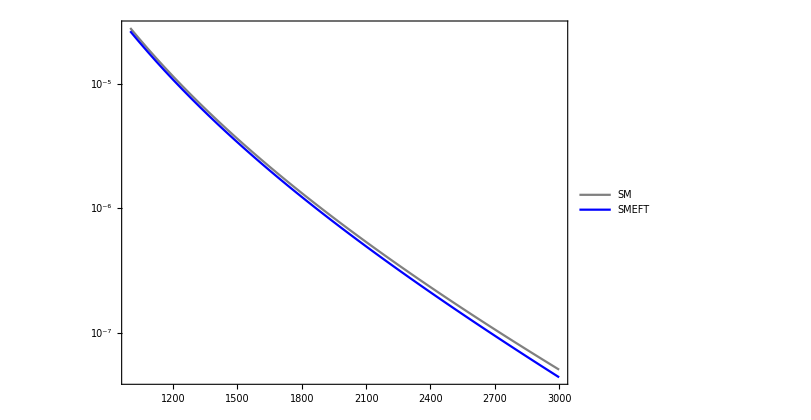

```mathematica
legend=Placed[LineLegend[{"SM","SMEFT"},LegendFunction->(Framed[#,Background->White]&),LegendMargins->5,LegendLayout->"Column"],{0.9,0.9}];
plot2=LogPlot[{dσdMdilepSMinterpol[M],dσdMdilepSMEFTinterpol[M]},{M,1000,3000},PlotStyle->{Gray,Blue},PlotLegends->legend]
Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/pp2ll_SMvsSMEFT.pdf",plot2];
```

## Checking (Junks + Compare w/ Adam’s + Old result)

```mathematica
σpp2llOxuubar=({{eLZ^2 qLZ^2,({{114615.,60.898,4.43501*10^-9}})},{eLA^2 qLA^2,({{2.72243*10^8,149456.,2.35593*10^-6}})},{eLA eLZ qLA qLZ,({{-222817.,163.095,3.98918*10^-8}})},{CqLeL1 eLA qLA,({{1.8566*10^9,1.02518*10^6,4.11822*10^-8}})},{CqLeL1 eLZ qLZ,({{1.09414*10^6,72335.3,3.33067*10^-21}})},{Γz1 eLA eLZ qLA qLZ,({{230.08,0.831207,4.86211*10^-17}})},{Γz1 eLZ^2 qLZ^2,({{-46993.9,22.7438,1.30649*10^-7}})},{CqLeL1^2,({{2.27813*10^12,1.66798*10^9,4.43706*10^-9}})},{CqLeL1 Γz1 eLZ qLZ,({{266373.,6389.48,2.17115*10^-17}})},{Γz1^2 eLA eLZ qLA qLZ,({{26.4872,0.211812,1.47993*10^-17}})},{Γz1^2 eLZ^2 qLZ^2,({{19237.,11.9771,1.98986*10^-8}})},{Γz2 eLA eLZ qLA qLZ,({{230.08,0.831207,4.86211*10^-17}})},{Γz2 eLZ^2 qLZ^2,({{-46993.9,22.7438,1.30649*10^-7}})},{CqLeL2 eLA qLA,({{1.8566*10^9,1.02518*10^6,4.11822*10^-8}})},{CqLeL2 eLZ qLZ,({{1.09414*10^6,72335.3,3.33067*10^-21}})},{CqLeLs eLA qLA,({{4.55627*10^12,3.33596*10^9,4.43706*10^-9}})},{CqLeLs eLZ qLZ,({{4.55407*10^12,3.92098*10^9,3.33585*10^-10}})},{CqLeLt eLA qLA,({{-1.13907*10^12,8.3399*10^8,4.43706*10^-9}})},{CqLeLt eLZ qLZ,({{-1.13852*10^12,9.80244*10^8,3.33585*10^-10}})}});
σpp2llOxddbar=({{eLZ^2 qLZ^2,({{83464.1,44.7793,3.44426*10^-9}})},{eLA^2 qLA^2,({{2.34089*10^8,131891.,1.061*10^-6}})},{eLA eLZ qLA qLZ,({{-187587.,132.509,1.30696*10^-8}})},{CqLeL1 eLA qLA,({{1.55969*10^9,835582.,1.55496*10^-8}})},{CqLeL1 eLZ qLZ,({{-2.30064*10^6,52555.7,7.77156*10^-21}})},{Γz1 eLA eLZ qLA qLZ,({{184.236,0.609463,2.22157*10^-16}})},{Γz1 eLZ^2 qLZ^2,({{-34190.1,16.4159,8.47853*10^-8}})},{CqLeL1^2,({{1.32197*10^12,9.87212*10^8,4.35104*10^-9}})},{CqLeL1 Γz1 eLZ qLZ,({{208806.,4611.95,3.67228*10^-17}})},{Γz1^2 eLA eLZ qLA qLZ,({{22.3526,0.156402,9.17733*10^-17}})},{Γz1^2 eLZ^2 qLZ^2,({{13994.8,8.96311,8.94587*10^-9}})},{Γz2 eLA eLZ qLA qLZ,({{184.236,0.609463,2.22157*10^-16}})},{Γz2 eLZ^2 qLZ^2,({{-34190.1,16.4159,8.47853*10^-8}})},{CqLeL2 eLA qLA,({{1.55969*10^9,835582.,1.55496*10^-8}})},{CqLeL2 eLZ qLZ,({{-2.30064*10^6,52555.7,7.77156*10^-21}})},{CqLeLs eLA qLA,({{2.64393*10^12,1.97442*10^9,4.35104*10^-9}})},{CqLeLs eLZ qLZ,({{2.61655*10^12,2.52256*10^9,3.72703*10^-10}})},{CqLeLt eLA qLA,({{-6.60983*10^11,4.93606*10^8,4.35104*10^-9}})},{CqLeLt eLZ qLZ,({{-6.54136*10^11,6.30641*10^8,3.72703*10^-10}})}});
LLcouplings={eLZ^2 qLZ^2,eLA^2 qLA^2,eLA qLA eLZ qLZ,
CqLeL1 eLA qLA,CqLeL1 eLZ qLZ,Γz1 eLA qLA eLZ qLZ,Γz1 eLZ^2 qLZ^2,
CqLeL1^2,CqLeL1 Γz1 eLZ qLZ,Γz1^2 eLA qLA eLZ qLZ,Γz1^2 eLZ^2 qLZ^2,Γz2 eLA qLA eLZ qLZ,Γz2 eLZ^2 qLZ^2,CqLeL2 eLA qLA,CqLeL2 eLZ qLZ,CqLeLs eLA qLA,CqLeLs eLZ qLZ,CqLeLt eLA qLA,CqLeLt eLZ qLZ};
```

```mathematica
σpp2lνOx2uubar=({{δGF6^2,({{2.62206*10^7,14551.2,2.35592*10^-6}})},{CHD6til δGF6,({{4.31038*10^7,23634.3,2.35526*10^-6}})},{CHdc16til δGF6,({{-163.318,0.0905017,6.67268*10^-9}})},{CHec16til δGF6,({{3634.14,3.48636,1.16988*10^-7}})},{CHL16til δGF6,({{92.0871,1.36549,1.44329*10^-20}})},{CHL36til δGF6,({{825.061,1.1016,1.77636*10^-20}})},{CHQ16til δGF6,({{1990.11,1.89357,1.01941*10^-11}})},{CHQ36til δGF6,({{-117.904,0.632541,0.}})},{CHuc16til δGF6,({{-1290.3,1.19657,7.37535*10^-8}})},{CHWB6til δGF6,({{9.23249*10^7,50625.,2.35546*10^-6}})},{CeQ6til δGF6,({{5484.26,3.5095,4.19851*10^-8}})},{Ceu6til δGF6,({{5488.37,3.11314,4.22794*10^-8}})},{CLQ36til δGF6,({{-5490.83,3.62892,4.3319*10^-8}})},{CLQ6til δGF6,({{5490.83,3.62892,4.3319*10^-8}})},{CLu6til δGF6,({{5485.69,3.11761,4.18026*10^-8}})},{CHD6til^2,({{1.32862*10^7,7452.93,2.35673*10^-6}})},{CHD6til CHdc16til,({{-236.651,0.125038,8.00118*10^-8}})},{CHD6til CHec16til,({{1701.28,1.57127,1.44711*10^-9}})},{CHD6til CHL16til,({{1184.28,1.13228,3.53541*10^-10}})},{CHD6til CHL36til,({{1342.58,1.21037,3.4553*10^-10}})},{CHD6til CHQ16til,({{2476.52,2.05408,4.25467*10^-8}})},{CHD6til CHQ36til,({{-2475.06,2.10132,4.04355*10^-8}})},{CHD6til CHuc16til,({{1337.59,1.29383,2.17348*10^-17}})},{CHD6til CHWB6til,({{7.72151*10^7,43312.5,2.35531*10^-6}})},{CeQ6til CHD6til,({{3381.33,2.1306,4.16*10^-8}})},{Ceu6til CHD6til,({{3383.95,2.18679,4.32841*10^-8}})},{CHD6til CLQ36til,({{-3380.97,2.27347,4.0812*10^-8}})},{CHD6til CLQ6til,({{3380.97,2.27347,4.0812*10^-8}})},{CHD6til CLu6til,({{3382.12,1.91038,4.09562*10^-8}})},{CHdc16til^2,({{-367.718,0.18084,1.26888*10^-7}})},{CHdc16til CHec16til,({{-162.041,0.0824522,2.24122*10^-8}})},{CHdc16til CHL16til,({{294.755,0.145932,8.51847*10^-8}})},{CHdc16til CHL36til,({{106.617,0.0586061,1.56691*10^-8}})},{CHdc16til CHQ16til,({{-386.867,0.193908,1.0871*10^-7}})},{CHdc16til CHQ36til,({{-93.7774,0.0875411,3.26186*10^-13}})},{CHdc16til CHuc16til,({{62.1146,0.0315667,1.51974*10^-8}})},{CHdc16til CHWB6til,({{-191.54,0.100089,3.27754*10^-8}})},{CeQ6til CHdc16til,({{-0.0838119,0.00137048,0.}})},{Ceu6til CHdc16til,({{0.035433,0.000579394,0.}})},{CHdc16til CLQ36til,({{-0.104226,0.00170429,0.}})},{CHdc16til CLQ6til,({{0.104226,0.00170429,0.}})},{CHdc16til CLu6til,({{-0.0440636,0.00072052,0.}})},{CHec16til^2,({{942.928,0.925777,4.18383*10^-8}})},{CHec16til CHL16til,({{90.8162,0.053713,2.84359*10^-8}})},{CHec16til CHL36til,({{817.89,0.402626,3.19011*10^-8}})},{CHec16til CHQ16til,({{4776.79,4.61709,5.74043*10^-9}})},{CHec16til CHQ36til,({{-2918.98,1.97569,3.09842*10^-8}})},{CHec16til CHuc16til,({{1127.78,1.09796,6.64268*10^-15}})},{CHec16til CHWB6til,({{2333.36,1.23441,1.27099*10^-9}})},{CeQ6til CHec16til,({{-1.82373,0.078375,0.}})},{Ceu6til CHec16til,({{0.771017,0.0331344,0.}})},{CHec16til CLQ36til,({{-0.104226,0.00170429,0.}})},{CHec16til CLQ6til,({{0.104226,0.00170429,0.}})},{CHec16til CLu6til,({{-0.0440636,0.00072052,0.}})},{CHL16til^2,({{1270.24,0.674205,4.86234*10^-9}})},{CHL16til CHL36til,({{1735.87,1.68567,2.55278*10^-8}})},{CHL16til CHQ16til,({{-2462.99,2.37267,6.91847*10^-17}})},{CHL16til CHQ36til,({{-916.892,1.17501,1.24123*10^-18}})},{CHL16til CHuc16til,({{3081.39,2.87561,6.88434*10^-8}})},{CHL16til CHWB6til,({{3120.98,2.99305,9.11284*10^-9}})},{CeQ6til CHL16til,({{-0.0838119,0.00137048,0.}})},{Ceu6til CHL16til,({{0.035433,0.000579394,0.}})},{CHL16til CLQ36til,({{1.63544,0.0814409,0.}})},{CHL16til CLQ6til,({{-1.63544,0.0814409,0.}})},{CHL16til CLu6til,({{0.691413,0.0344306,0.}})},{CHL36til^2,({{369.419,0.330444,3.12702*10^-14}})},{CHL36til CHQ16til,({{-726.282,1.44176,6.66134*10^-20}})},{CHL36til CHQ36til,({{-495.931,1.03965,9.32587*10^-20}})},{CHL36til CHuc16til,({{2802.65,2.6143,1.09059*10^-7}})},{CHL36til CHWB6til,({{3012.52,2.82079,8.56984*10^-9}})},{CeQ6til CHL36til,({{0.292265,0.00477906,0.}})},{Ceu6til CHL36til,({{-0.12356,0.00202043,0.}})},{CHL36til CLQ36til,({{2.10358,0.0739398,1.11022*10^-21}})},{CHL36til CLQ6til,({{-2.10358,0.0739398,1.11022*10^-21}})},{CHL36til CLu6til,({{0.889327,0.0312594,0.}})},{CHQ16til^2,({{1300.77,0.713637,4.37955*10^-9}})},{CHQ16til CHQ36til,({{279.008,0.601858,0.}})},{CHQ16til CHuc16til,({{211.739,0.116661,4.49672*10^-8}})},{CHQ16til CHWB6til,({{1393.43,1.29906,4.92272*10^-16}})},{CeQ6til CHQ16til,({{-0.887335,0.0540806,1.11022*10^-21}})},{Ceu6til CHQ16til,({{-0.0913075,0.00149305,0.}})},{CHQ16til CLQ36til,({{-1.10347,0.0672533,1.11022*10^-21}})},{CHQ16til CLQ6til,({{1.10347,0.0672533,1.11022*10^-21}})},{CHQ16til CLu6til,({{0.113548,0.00185671,1.11022*10^-21}})},{CHQ36til^2,({{-379.772,0.364923,2.46484*10^-15}})},{CHQ36til CHuc16til,({{-923.647,0.452988,3.00002*10^-8}})},{CHQ36til CHWB6til,({{-2101.89,2.08445,1.15419*10^-9}})},{CeQ6til CHQ36til,({{1.84825,0.0434942,0.}})},{Ceu6til CHQ36til,({{-0.314806,0.00514765,0.}})},{CHQ36til CLQ36til,({{2.29843,0.0540883,0.}})},{CHQ36til CLQ6til,({{-2.29843,0.0540883,0.}})},{CHQ36til CLu6til,({{0.391485,0.00640149,0.}})},{CHuc16til^2,({{711.483,0.679296,2.56079*10^-8}})},{CHuc16til CHWB6til,({{1416.04,1.39549,9.73969*10^-15}})},{CeQ6til CHuc16til,({{0.111749,0.0018273,1.11022*10^-21}})},{Ceu6til CHuc16til,({{-1.15063,0.0497961,0.}})},{CHuc16til CLQ36til,({{0.138968,0.00227239,0.}})},{CHuc16til CLQ6til,({{-0.138968,0.00227239,0.}})},{CHuc16til CLu6til,({{1.43089,0.0619252,0.}})},{CHWB6til^2,({{9.14341*10^7,50752.9,2.35548*10^-6}})},{CeQ6til CHWB6til,({{7244.74,4.18178,4.07664*10^-8}})},{Ceu6til CHWB6til,({{7246.64,4.2641,4.25114*10^-8}})},{CHWB6til CLQ36til,({{-7243.04,4.37135,4.17329*10^-8}})},{CHWB6til CLQ6til,({{7243.04,4.37135,4.17329*10^-8}})},{CHWB6til CLu6til,({{7245.33,4.00433,4.10359*10^-8}})},{CHB6til CHWB6til,({{-3.26416*10^7,17898.9,2.35538*10^-6}})},{CHW6til CHWB6til,({{-3.26416*10^7,17898.9,2.35538*10^-6}})},{CeQ6til^2,({{619.852,0.453837,4.43706*10^-9}})},{Ceu6til^2,({{619.852,0.453837,4.43706*10^-9}})},{CLQ36til^2,({{619.852,0.453837,4.43706*10^-9}})},{CLQ36til CLQ6til,({{-1239.7,0.907674,4.43706*10^-9}})},{CLQ6til^2,({{619.852,0.453837,4.43706*10^-9}})},{CLu6til^2,({{619.852,0.453837,4.43706*10^-9}})},{δGF8,({{-1.2361*10^7,6889.92,2.35634*10^-6}})},{CHD28til,({{-1.30544*10^7,7155.63,2.35508*10^-6}})},{CHD8til,({{-2.18513*10^6,1217.98,2.35634*10^-6}})},{CHdc18til,({{57.748,0.0284845,1.19887*10^-7}})},{CHec18til,({{-894.6,0.848081,7.69622*10^-9}})},{CHL18til,({{361.004,0.34522,1.11022*10^-20}})},{CHL28til,({{101.768,0.278748,8.88178*10^-20}})},{CHL38til,({{101.768,0.278748,8.88178*10^-20}})},{CHQ18til,({{-810.521,0.725365,1.2245*10^-9}})},{CHQ28til,({{148.311,0.148287,0.}})},{CHQ38til,({{148.311,0.148287,0.}})},{CHuc18til,({{352.197,0.326852,5.82393*10^-9}})},{CHW28til,({{-2.17389*10^7,11930.4,2.35418*10^-6}})},{CHWB8til,({{-4.94717*10^11,2.71276*10^8,2.35538*10^-6}})},{CeQs8til,({{12.6447,0.0108601,6.10656*10^-13}})},{CeQt8til,({{-9.48355,0.00814506,6.10656*10^-13}})},{Ceus8til,({{50.5214,0.04532,1.49254*10^-8}})},{Ceut8til,({{-12.6303,0.01133,1.49254*10^-8}})},{CHeQ18til,({{-969.613,0.625904,4.20242*10^-8}})},{CHeQ38til,({{969.613,0.625904,4.20242*10^-8}})},{CHeu8til,({{-970.168,0.565718,4.24941*10^-8}})},{CHLQ18til,({{-970.483,0.666862,4.31262*10^-8}})},{CHLQ28til,({{970.483,0.666862,4.31262*10^-8}})},{CHLQ38til,({{-970.483,0.666862,4.31262*10^-8}})},{CHLQ48til,({{970.483,0.666862,4.31262*10^-8}})},{CHLu18til,({{-969.796,0.556257,4.0888*10^-8}})},{CHLu38til,({{-969.796,0.556257,4.0888*10^-8}})},{CLQs18til,({{72.3681,0.0547036,1.01507*10^-9}})},{CLQs38til,({{-72.3681,0.0547036,1.01507*10^-9}})},{CLQt18til,({{-18.092,0.0136759,1.01507*10^-9}})},{CLQt38til,({{18.092,0.0136759,1.01507*10^-9}})},{CLus8til,({{25.2696,0.0199027,4.34292*10^-9}})},{CLut8til,({{-18.9522,0.014927,4.34292*10^-9}})}});
```

```mathematica
ref=Sum[σpp2lνOx2uubar[[i,1]]σpp2lνOx2uubar[[i,2,1,1]],{i,1,Length[σpp2lνOx2uubar]}]
```

619.852 CeQ6til^2+3381.33 CeQ6til CHD6til-0.0838119 CeQ6til CHdc16til-1.82373 CeQ6til CHec16til-0.0838119 CeQ6til CHL16til+0.292265 CeQ6til CHL36til-0.887335 CeQ6til CHQ16til+1.84825 CeQ6til CHQ36til+0.111749 CeQ6til CHuc16til+7244.74 CeQ6til CHWB6til+5484.26 CeQ6til δGF6+12.6447 CeQs8til-9.48355 CeQt8til+619.852 Ceu6til^2+3383.95 Ceu6til CHD6til+0.035433 Ceu6til CHdc16til+0.771017 Ceu6til CHec16til+0.035433 Ceu6til CHL16til-0.12356 Ceu6til CHL36til-0.0913075 Ceu6til CHQ16til-0.314806 Ceu6til CHQ36til-1.15063 Ceu6til CHuc16til+7246.64 Ceu6til CHWB6til+5488.37 Ceu6til δGF6+50.5214 Ceus8til-12.6303 Ceut8til-3.26416×10^7 CHB6til CHWB6til-1.30544×10^7 CHD28til+1.32862×10^7 CHD6til^2-236.651 CHD6til CHdc16til+1701.28 CHD6til CHec16til+1184.28 CHD6til CHL16til+1342.58 CHD6til CHL36til+2476.52 CHD6til CHQ16til-2475.06 CHD6til CHQ36til+1337.59 CHD6til CHuc16til+7.72151×10^7 CHD6til CHWB6til-3380.97 CHD6til CLQ36til+3380.97 CHD6til CLQ6til+3382.12 CHD6til CLu6til+4.31038×10^7 CHD6til δGF6-2.18513×10^6 CHD8til-367.718 CHdc16til^2-162.041 CHdc16til CHec16til+294.755 CHdc16til CHL16til+106.617 CHdc16til CHL36til-386.867 CHdc16til CHQ16til-93.7774 CHdc16til CHQ36til+62.1146 CHdc16til CHuc16til-191.54 CHdc16til CHWB6til-0.104226 CHdc16til CLQ36til+0.104226 CHdc16til CLQ6til-0.0440636 CHdc16til CLu6til-163.318 CHdc16til δGF6+57.748 CHdc18til+942.928 CHec16til^2+90.8162 CHec16til CHL16til+817.89 CHec16til CHL36til+4776.79 CHec16til CHQ16til-2918.98 CHec16til CHQ36til+1127.78 CHec16til CHuc16til+2333.36 CHec16til CHWB6til-0.104226 CHec16til CLQ36til+0.104226 CHec16til CLQ6til-0.0440636 CHec16til CLu6til+3634.14 CHec16til δGF6-894.6 CHec18til-969.613 CHeQ18til+969.613 CHeQ38til-970.168 CHeu8til+1270.24 CHL16til^2+1735.87 CHL16til CHL36til-2462.99 CHL16til CHQ16til-916.892 CHL16til CHQ36til+3081.39 CHL16til CHuc16til+3120.98 CHL16til CHWB6til+1.63544 CHL16til CLQ36til-1.63544 CHL16til CLQ6til+0.691413 CHL16til CLu6til+92.0871 CHL16til δGF6+361.004 CHL18til+101.768 CHL28til+369.419 CHL36til^2-726.282 CHL36til CHQ16til-495.931 CHL36til CHQ36til+2802.65 CHL36til CHuc16til+3012.52 CHL36til CHWB6til+2.10358 CHL36til CLQ36til-2.10358 CHL36til CLQ6til+0.889327 CHL36til CLu6til+825.061 CHL36til δGF6+101.768 CHL38til-970.483 CHLQ18til+970.483 CHLQ28til-970.483 CHLQ38til+970.483 CHLQ48til-969.796 CHLu18til-969.796 CHLu38til+1300.77 CHQ16til^2+279.008 CHQ16til CHQ36til+211.739 CHQ16til CHuc16til+1393.43 CHQ16til CHWB6til-1.10347 CHQ16til CLQ36til+1.10347 CHQ16til CLQ6til+0.113548 CHQ16til CLu6til+1990.11 CHQ16til δGF6-810.521 CHQ18til+148.311 CHQ28til-379.772 CHQ36til^2-923.647 CHQ36til CHuc16til-2101.89 CHQ36til CHWB6til+2.29843 CHQ36til CLQ36til-2.29843 CHQ36til CLQ6til+0.391485 CHQ36til CLu6til-117.904 CHQ36til δGF6+148.311 CHQ38til+711.483 CHuc16til^2+1416.04 CHuc16til CHWB6til+0.138968 CHuc16til CLQ36til-0.138968 CHuc16til CLQ6til+1.43089 CHuc16til CLu6til-1290.3 CHuc16til δGF6+352.197 CHuc18til-2.17389×10^7 CHW28til-3.26416×10^7 CHW6til CHWB6til+9.14341×10^7 CHWB6til^2-7243.04 CHWB6til CLQ36til+7243.04 CHWB6til CLQ6til+7245.33 CHWB6til CLu6til+9.23249×10^7 CHWB6til δGF6-4.94717×10^11 CHWB8til+619.852 CLQ36til^2-1239.7 CLQ36til CLQ6til-5490.83 CLQ36til δGF6+619.852 CLQ6til^2+5490.83 CLQ6til δGF6+72.3681 CLQs18til-72.3681 CLQs38til-18.092 CLQt18til+18.092 CLQt38til+619.852 CLu6til^2+5485.69 CLu6til δGF6+25.2696 CLus8til-18.9522 CLut8til+2.62206×10^7 δGF6^2-1.2361×10^7 δGF8

```mathematica
Coefficient[ref,CLut8til]
```

-18.9522

```mathematica
Coefficient[619.852 CeQ6til^2+3381.3 CeQ6til CHD6til-0.0837544 CeQ6til CHdc16til-1.82364 CeQ6til CHec16til-0.0837544 CeQ6til CHL16til+0.292064 CeQ6til CHL36til-0.887522 CeQ6til CHQ16til+1.84747 CeQ6til CHQ36til+0.111673 CeQ6til CHuc16til+7244.78 CeQ6til CHWB6til+5484.25 CeQ6til δGF6+12.6443 CeQs8til-3.16108 CeQt8til+619.852 Ceu6til^2+3383.82 Ceu6til CHD6til+0.0354087 Ceu6til CHdc16til+0.770975 Ceu6til CHec16til+0.0354087 Ceu6til CHL16til-0.123475 Ceu6til CHL36til-0.0912449 Ceu6til CHQ16til-0.31459 Ceu6til CHQ36til-1.15056 Ceu6til CHuc16til+7246.54 Ceu6til CHWB6til+5488.29 Ceu6til δGF6+50.5203 Ceus8til-12.6301 Ceut8til-3.26416*10^7 CHB6til CHWB6til-1.30544*10^7 CHD28til+1.32863*10^7 CHD6til^2-236.626 CHD6til CHdc16til+1701.32 CHD6til CHec16til+1184.38 CHD6til CHL16til+1342.56 CHD6til CHL36til+2476.42 CHD6til CHQ16til-2475.14 CHD6til CHQ36til+1337.5 CHD6til CHuc16til+7.72133*10^7 CHD6til CHWB6til-3380.96 CHD6til CLQ36til+3380.96 CHD6til CLQ6til+3382.14 CHD6til CLu6til+4.31038*10^7 CHD6til δGF6-2.18503*10^6 CHD8til-367.701 CHdc16til^2-161.978 CHdc16til CHec16til+294.776 CHdc16til CHL16til+106.472 CHdc16til CHL36til-386.952 CHdc16til CHQ16til-94.031 CHdc16til CHQ36til+62.0557 CHdc16til CHuc16til-191.607 CHdc16til CHWB6til-0.104155 CHdc16til CLQ36til+0.104155 CHdc16til CLQ6til-0.0440334 CHdc16til CLu6til-163.019 CHdc16til δGF6+57.7477 CHdc18til+943.049 CHec16til^2+90.8335 CHec16til CHL16til+817.652 CHec16til CHL36til+4776.52 CHec16til CHQ16til-2920.02 CHec16til CHQ36til+1127.65 CHec16til CHuc16til+2333.07 CHec16til CHWB6til-0.104155 CHec16til CLQ36til+0.104155 CHec16til CLQ6til-0.0440334 CHec16til CLu6til+3635.2 CHec16til δGF6-894.603 CHec18til-969.602 CHeQ18til+969.602 CHeQ38til-970.154 CHeu8til+1270.24 CHL16til^2+1736.02 CHL16til CHL36til-2462.54 CHL16til CHQ16til-916.021 CHL16til CHQ36til+3081.48 CHL16til CHuc16til+3121.24 CHL16til CHWB6til+1.63573 CHL16til CLQ36til-1.63573 CHL16til CLQ6til+0.691533 CHL16til CLu6til+91.5787 CHL16til δGF6+360.967 CHL18til+101.844 CHL28til+370.01 CHL36til^2-726.233 CHL36til CHQ16til-494.09 CHL36til CHQ36til+2803.03 CHL36til CHuc16til+3013.25 CHL36til CHWB6til+2.10308 CHL36til CLQ36til-2.10308 CHL36til CLQ6til+0.889117 CHL36til CLu6til+823.068 CHL36til δGF6+101.844 CHL38til-970.472 CHLQ18til+970.472 CHLQ28til-970.472 CHLQ38til+970.472 CHLQ48til-969.786 CHLu18til-969.786 CHLu38til+1300.82 CHQ16til^2+278.658 CHQ16til CHQ36til+211.836 CHQ16til CHuc16til+1393.39 CHQ16til CHWB6til-1.1037 CHQ16til CLQ36til+1.1037 CHQ16til CLQ6til+0.11347 CHQ16til CLu6til+1990.19 CHQ16til δGF6-810.408 CHQ18til+148.536 CHQ28til-377.831 CHQ36til^2-923.085 CHQ36til CHuc16til-2100.59 CHQ36til CHWB6til+2.29747 CHQ36til CLQ36til-2.29747 CHQ36til CLQ6til+0.391216 CHQ36til CLu6til-121.764 CHQ36til δGF6+148.536 CHQ38til+711.653 CHuc16til^2+1416.23 CHuc16til CHWB6til+0.138873 CHuc16til CLQ36til-0.138873 CHuc16til CLQ6til+1.43081 CHuc16til CLu6til-1291.17 CHuc16til δGF6+352.224 CHuc18til-2.17388*10^7 CHW28til-3.26416*10^7 CHW6til CHWB6til+9.14336*10^7 CHWB6til^2-7242.93 CHWB6til CLQ36til+7242.93 CHWB6til CLQ6til+7245.37 CHWB6til CLu6til+9.23249*10^7 CHWB6til δGF6-4.94717*10^11 CHWB8til+619.852 CLQ36til^2-1239.7 CLQ36til CLQ6til-5490.63 CLQ36til δGF6+619.852 CLQ6til^2+5490.63 CLQ6til δGF6+72.3713 CLQs18til-72.3713 CLQs38til-18.0929 CLQt18til+18.0929 CLQt38til+619.852 CLu6til^2+5485.59 CLu6til δGF6+25.2696 CLus8til-6.31742 CLut8til+2.62198*10^7 δGF6^2-1.23604*10^7 δGF8,CeQt8til]
```

-3.16108

```mathematica
Coefficient[50.5165 (25.1432 c16HψL^2-48.7438 c16HψL c16Hψq+25.7485 c16Hψq^2+7.14502 c18HψL-16.0413 c18Hψq+2.01593 c28HψL+2.94015 c28Hψq+34.363 c16HψL c36HψL-14.3752 c16Hψq c36HψL+7.32403 c36HψL^2-18.1316 c16HψL c36Hψq+5.51567 c16Hψq c36Hψq-9.77998 c36HψL c36Hψq-7.47883 c36Hψq^2+2.01593 c38HψL+2.94015 c38Hψq+0.250281 c8eQs-0.187711 c8eQt-19.2033 c8eu+1. c8eus-0.25 c8eut-323043. c8HBW-43250.6 c8HD-258399. c8HD2-430297. c8HW2-11.0289 c8HWB-19.2096 c8LQ1+1.43252 c8LQ1s-0.35813 c8LQ1t+4.80239 c8LQ2+4.80239 c8LQ3-0.35813 c8LQ3s+0.0895325 c8LQ3t-4.80239 c8LQ4-19.196 c8Lu1-4.79899 c8Lu3+0.500187 c8Lus-0.37514 c8Lut-19.1923 c8Qe1+4.79808 c8Qe3-0.00165784 c16HψL ceQ-0.0175676 c16Hψq ceQ+0.00578113 c36HψL ceQ+0.0365688 c36Hψq ceQ+12.2694 ceQ^2+0.000700881 c16HψL ceu-0.00180611 c16Hψq ceu-0.00244408 c36HψL ceu-0.00622701 c36Hψq ceu+12.2694 ceu^2+58.0679 c16HψL cHBW-15.5453 c16Hψq cHBW+58.055 c36HψL cHBW+15.5122 c36Hψq cHBW+143.416 ceQ cHBW+143.416 ceu cHBW-646086. cHB cHBW+1.80976*10^6 cHBW^2+23.4437 c16HψL cHD+49.0184 c16Hψq cHD+26.5747 c36HψL cHD-48.993 c36Hψq cHD+66.9295 ceQ cHD+66.9795 ceu cHD+1.52834*10^6 cHBW cHD+262988. cHD^2+5.83481 c16HψL cHd6-7.65933 c16Hψq cHd6+2.10752 c36HψL cHd6-1.86124 c36Hψq cHd6-0.00165784 ceQ cHd6+0.000700881 ceu cHd6+0.00288768 cHBW cHd6-4.68379 cHD cHd6-7.27829 cHd6^2+1.14306 cHd8+1.79796 c16HψL cHe6+94.5467 c16Hψq cHe6+16.1846 c36HψL cHe6-57.7991 c36Hψq cHe6-0.0360971 ceQ cHe6+0.0152607 ceu cHe6+58.0679 cHBW cHe6+33.6762 cHD cHe6-3.20619 cHd6 cHe6+18.6668 cHe6^2-17.7078 cHe8+60.9951 c16HψL cHu6+4.19309 c16Hψq cHu6+55.4833 c36HψL cHu6-18.2716 c36Hψq cHu6+0.00221045 ceQ cHu6-0.0227742 ceu cHu6-15.5417 cHBW cHu6+26.4745 cHD cHu6+1.22834 cHd6 cHu6+22.3207 cHe6 cHu6+14.0865 cHu6^2+6.97195 cHu8-646086. cHBW cHW+3.71418 c16HψL cHWB+43.126 c16Hψq cHWB+1.58945 c36HψL cHWB-57.0914 c36Hψq cHWB-0.0123595 ceQ cHWB+0.0224671 ceu cHWB-22.0578 cHB cHWB+113.895 cHBW cHWB+19.382 cHD cHWB-3.79556 cHd6 cHWB-11.887 cHe6 cHWB+43.5746 cHu6 cHWB-22.0578 cHW cHWB-31.3303 cHWB^2-0.0323776 c16HψL cLQ1+0.0218466 c16Hψq cLQ1-0.0416285 c36HψL cLQ1-0.0454761 c36Hψq cLQ1+143.416 cHBW cLQ1+66.9229 cHD cLQ1+0.00206165 cHd6 cLQ1+0.00206165 cHe6 cLQ1-0.00274886 cHu6 cLQ1-0.0489415 cHWB cLQ1+12.2694 cLQ1^2+0.0080944 c16HψL cLQ3-0.00546166 c16Hψq cLQ3+0.0104071 c36HψL cLQ3+0.011369 c36Hψq cLQ3-35.8539 cHBW cLQ3-16.7307 cHD cLQ3-0.000515412 cHd6 cLQ3-0.000515412 cHe6 cLQ3+0.000687216 cHu6 cLQ3+0.0122354 cHWB cLQ3-6.13469 cLQ1 cLQ3+0.766836 cLQ3^2+0.0136882 c16HψL cLu+0.00224603 c16Hψq cLu+0.0175992 c36HψL cLu+0.00774375 c36Hψq cLu+143.416 cHBW cLu+66.9462 cHD cLu-0.000871598 cHd6 cLu-0.000871598 cHe6 cLu+0.0283215 cHu6 cLu-0.000750644 cHWB cLu+12.2694 cLu^2+1.81257 c16HψL δGF6+39.3942 c16Hψq δGF6+16.2918 c36HψL δGF6-2.41022 c36Hψq δGF6+108.555 ceQ δGF6+108.635 ceu δGF6+1.82741*10^6 cHBW δGF6+853197. cHD δGF6-3.22681 cHd6 δGF6+71.9554 cHe6 δGF6-25.5576 cHu6 δGF6+74.2433 cHWB δGF6+108.682 cLQ1 δGF6-27.1704 cLQ3 δGF6+108.582 cLu δGF6+518995. δGF6^2-244662. δGF8) x^2,c8Lut]
```

-18.9508 x^2

```mathematica
subtract1=SeriesCoefficient[ZinvolveCoupling[Sum[LLcouplings[[i]]σpp2llOxuubar[[i,2,1,1]]+RRcouplings[[i]]σpp2llOxuubar[[i,2,1,1]]+(RLcouplings[[i]]/.CqReLt->3CqReLt)σpp2llOxuubar[[i,2,1,1]]+(LRcouplings[[i]]/.CqLeRt->3CqLeRt)σpp2llOxuubar[[i,2,1,1]],{i,1,19}]//.{qLA->uLAval,qRA->uRAval,qLZ->uLZval,qRZ->uRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CuLeL],CqLeL2->Cqe2[CuLeL],CqLeLs->Cqes[CuLeL],CqLeLt->Cqet[CuLeL],
CqLeR1->Cqe1[CuLeR],CqLeR2->Cqe2[CuLeR],CqLeRs->Cqes[CuLeR],CqLeRt->Cqet[CuLeR],
CqReL1->Cqe1[CuReL],CqReL2->Cqe2[CuReL],CqReLs->Cqes[CuReL],CqReLt->Cqet[CuReL],
CqReR1->Cqe1[CuReR],CqReR2->Cqe2[CuReR],CqReRs->Cqes[CuReR],CqReRt->Cqet[CuReR]}/.vT2vhat],{x,0,2}]-Sum[σpp2lνOx2uubar[[i,1]]σpp2lνOx2uubar[[i,2,1,1]],{i,1,Length[σpp2lνOx2uubar]}]//Simplify//Expand;
```

```mathematica
Coefficient[subtract1,table1[[1]]]
```

-823.016

```mathematica
table1=Table[σpp2lνOx2uubar[[i,1]],{i,1,Length[σpp2lνOx2uubar]}];
Length[table1]
table2=Table[Coefficient[subtract1,table1[[i]]]/Coefficient[ref,table1[[i]]],{i,1,Length[table1]}];
table3={};
Monitor[For[i=1,i≤Length[table1],i++1,If[Abs[table2[[i]]]>0.1,AppendTo[table3,1]]],i]
Length[table3]
```

146

0

```mathematica
σpp2lνOxddbar=({{δGF6,({{-2.65788*10^6,1635.81,1.07576*10^-6}})},{CHD6til,({{-3.27662*10^6,1825.71,1.05963*10^-6}})},{CHdc16til,({{-216.666,0.194903,4.25549*10^-9}})},{CHec16til,({{-1510.57,1.425,3.27556*10^-9}})},{CHL16til,({{835.354,0.784433,1.00312*10^-16}})},{CHL36til,({{351.437,0.469332,2.22045*10^-21}})},{CHQ16til,({{986.279,0.960525,6.39923*10^-9}})},{CHQ36til,({{306.006,0.292624,3.9188*10^-19}})},{CHuc16til,({{-143.739,0.0710003,7.73389*10^-8}})},{CHWB6til,({{-7.01732*10^6,3915.18,1.06055*10^-6}})},{Ced6til,({{814.534,0.46428,1.52232*10^-8}})},{CeQ6til,({{816.825,0.686526,1.43808*10^-8}})},{CLd6til,({{815.301,0.471122,1.52283*10^-8}})},{CLQ36til,({{812.406,0.701972,1.56546*10^-8}})},{CLQ6til,({{812.406,0.701972,1.56546*10^-8}})}});
```

```mathematica
ref=Sum[σpp2lνOxddbar[[i,1]]σpp2lνOxddbar[[i,2,1,1]],{i,1,Length[σpp2lνOxddbar]}]
```

814.534 Ced6til+816.825 CeQ6til-3.27662×10^6 CHD6til-216.666 CHdc16til-1510.57 CHec16til+835.354 CHL16til+351.437 CHL36til+986.279 CHQ16til+306.006 CHQ36til-143.739 CHuc16til-7.01732×10^6 CHWB6til+815.301 CLd6til+812.406 CLQ36til+812.406 CLQ6til-2.65788×10^6 δGF6

```mathematica
subtract1=SeriesCoefficient[ZinvolveCoupling[Sum[LLcouplings[[i]]σpp2llOxddbar[[i,2,1,1]]+RRcouplings[[i]]σpp2llOxddbar[[i,2,1,1]]+(RLcouplings[[i]]/.CqReLt->3CqReLt)σpp2llOxddbar[[i,2,1,1]]+(LRcouplings[[i]]/.CqLeRt->3CqLeRt)σpp2llOxddbar[[i,2,1,1]],{i,1,19}]//.{qLA->dLAval,qRA->dRAval,qLZ->dLZval,qRZ->dRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CdLeL],CqLeL2->Cqe2[CdLeL],CqLeLs->Cqes[CdLeL],CqLeLt->Cqet[CdLeL],
CqLeR1->Cqe1[CdLeR],CqLeR2->Cqe2[CdLeR],CqLeRs->Cqes[CdLeR],CqLeRt->Cqet[CdLeR],
CqReL1->Cqe1[CdReL],CqReL2->Cqe2[CdReL],CqReLs->Cqes[CdReL],CqReLt->Cqet[CdReL],
CqReR1->Cqe1[CdReR],CqReR2->Cqe2[CdReR],CqReRs->Cqes[CdReR],CqReRt->Cqet[CdReR]}/.vT2vhat],{x,0,1}]-ref//Simplify//Expand;
```

```mathematica
table1=Table[σpp2lνOxddbar[[i,1]],{i,1,Length[σpp2lνOxddbar]}];
Length[table1]
table2=Table[Coefficient[subtract1,table1[[i]]]/Coefficient[ref,table1[[i]]],{i,1,Length[table1]}];
table3={};
Monitor[For[i=1,i≤Length[table1],i++1,If[Abs[table2[[i]]]>0.1,AppendTo[table3,1]]],i]
Length[table3]
```

15

0

```mathematica
σpp2lνOx2ddbar=({{δGF6^2,({{5.63777*10^6,3317.57,1.08165*10^-6}})},{CHD6til δGF6,({{9.26748*10^6,5162.09,1.05932*10^-6}})},{CHdc16til δGF6,({{430.717,0.326466,9.32267*10^-9}})},{CHec16til δGF6,({{2942.06,2.77754,1.79438*10^-8}})},{CHL16til δGF6,({{-370.278,1.1988,5.55112*10^-21}})},{CHL36til δGF6,({{314.063,0.907326,0.}})},{CHQ16til δGF6,({{-1266.92,1.09983,2.50515*10^-11}})},{CHQ36til δGF6,({{-304.949,0.477562,0.}})},{CHuc16til δGF6,({{203.302,0.11392,2.84204*10^-8}})},{CHWB6til δGF6,({{1.9848*10^7,11068.7,1.05995*10^-6}})},{Ced6til δGF6,({{-2303.94,1.29901,1.57005*10^-8}})},{CeQ6til δGF6,({{-2309.73,1.86549,1.44837*10^-8}})},{CLd6til δGF6,({{-2305.88,1.30096,1.52459*10^-8}})},{CLQ36til δGF6,({{-2298.61,1.89763,1.56619*10^-8}})},{CLQ6til δGF6,({{-2298.61,1.89763,1.56619*10^-8}})},{CHD6til^2,({{2.85825*10^6,1744.15,1.06068*10^-6}})},{CHD6til CHdc16til,({{-762.354,0.715244,2.54062*10^-12}})},{CHD6til CHec16til,({{2900.28,2.78553,4.9562*10^-9}})},{CHD6til CHL16til,({{1867.19,1.75901,3.58843*10^-9}})},{CHD6til CHL36til,({{2127.63,2.09104,2.9708*10^-9}})},{CHD6til CHQ16til,({{-1248.27,0.7796,1.01745*10^-8}})},{CHD6til CHQ36til,({{-1383.61,0.722212,4.78028*10^-9}})},{CHD6til CHuc16til,({{327.939,0.16625,1.45102*10^-7}})},{CHD6til CHWB6til,({{1.66037*10^7,9474.2,1.06085*10^-6}})},{Ced6til CHD6til,({{-1419.43,0.906241,1.52466*10^-8}})},{CeQ6til CHD6til,({{-1424.56,1.26117,1.40975*10^-8}})},{CHD6til CLd6til,({{-1421.12,0.776422,1.52581*10^-8}})},{CHD6til CLQ36til,({{-1423.77,1.13575,1.35115*10^-8}})},{CHD6til CLQ6til,({{-1423.77,1.13575,1.35115*10^-8}})},{CHdc16til^2,({{408.035,0.37316,3.40283*10^-8}})},{CHdc16til CHec16til,({{-593.105,0.533988,3.04168*10^-12}})},{CHdc16til CHL16til,({{-1099.8,1.07415,3.55757*10^-8}})},{CHdc16til CHL36til,({{-1082.77,1.03431,4.61823*10^-8}})},{CHdc16til CHQ16til,({{255.667,0.254527,2.89896*10^-8}})},{CHdc16til CHQ36til,({{279.572,0.137741,1.66589*10^-8}})},{CHdc16til CHuc16til,({{5.06479,0.00662995,1.11022*10^-21}})},{CHdc16til CHWB6til,({{-766.964,0.709224,4.62527*10^-12}})},{Ced6til CHdc16til,({{2.30617,0.0365272,0.}})},{CeQ6til CHdc16til,({{0.0795243,0.00121467,0.}})},{CHdc16til CLd6til,({{-2.8679,0.0454244,1.11022*10^-21}})},{CHdc16til CLQ36til,({{-0.0988945,0.00151053,0.}})},{CHdc16til CLQ6til,({{-0.0988945,0.00151053,0.}})},{CHec16til^2,({{881.213,0.845946,3.32713*10^-8}})},{CHec16til CHL16til,({{84.9279,0.0470348,2.36542*10^-8}})},{CHec16til CHL36til,({{763.132,0.393053,3.54927*10^-8}})},{CHec16til CHQ16til,({{-2563.03,2.39229,1.59356*10^-9}})},{CHec16til CHQ36til,({{-1609.38,1.39809,2.24247*10^-9}})},{CHec16til CHuc16til,({{201.533,0.0995247,2.88821*10^-8}})},{CHec16til CHWB6til,({{3368.7,3.30914,2.93262*10^-9}})},{Ced6til CHec16til,({{0.759476,0.0120305,0.}})},{CeQ6til CHec16til,({{-4.35235,0.0689435,0.}})},{CHec16til CLd6til,({{0.0172569,0.000263585,0.}})},{CHec16til CLQ36til,({{-0.0988945,0.00151053,0.}})},{CHec16til CLQ6til,({{-0.0988945,0.00151053,0.}})},{CHL16til^2,({{1186.67,0.626735,3.45219*10^-9}})},{CHL16til CHL36til,({{1622.09,1.56332,3.73174*10^-8}})},{CHL16til CHQ16til,({{1685.67,1.58837,8.06516*10^-14}})},{CHL16til CHQ36til,({{-50.7488,0.786079,3.33067*10^-21}})},{CHL16til CHuc16til,({{-366.901,0.18041,7.42256*10^-8}})},{CHL16til CHWB6til,({{3516.51,3.21936,2.51835*10^-9}})},{Ced6til CHL16til,({{-0.0138768,0.000211957,0.}})},{CeQ6til CHL16til,({{0.0795243,0.00121467,0.}})},{CHL16til CLd6til,({{0.790605,0.0125043,0.}})},{CHL16til CLQ36til,({{-4.53074,0.0716588,0.}})},{CHL16til CLQ6til,({{-4.53074,0.0716588,0.}})},{CHL36til^2,({{345.568,0.310519,1.56463*10^-14}})},{CHL36til CHQ16til,({{1035.07,1.01243,1.96406*10^-16}})},{CHL36til CHQ36til,({{406.768,0.618012,0.}})},{CHL36til CHuc16til,({{-132.795,0.0695939,1.26777*10^-8}})},{CHL36til CHWB6til,({{3535.93,3.33604,3.58861*10^-9}})},{Ced6til CHL36til,({{0.0483906,0.000739127,0.}})},{CeQ6til CHL36til,({{-0.277313,0.00423573,0.}})},{CHL36til CLd6til,({{0.713221,0.011345,0.}})},{CHL36til CLQ36til,({{-4.08727,0.0650152,1.11022*10^-21}})},{CHL36til CLQ6til,({{-4.08727,0.0650152,1.11022*10^-21}})},{CHQ16til^2,({{-314.171,0.301126,6.35048*10^-19}})},{CHQ16til CHQ36til,({{-575.007,0.538275,1.40377*10^-17}})},{CHQ16til CHuc16til,({{-193.272,0.0961067,1.75982*10^-8}})},{CHQ16til CHWB6til,({{-644.737,0.620929,3.4841*10^-15}})},{Ced6til CHQ16til,({{0.0357593,0.000546194,0.}})},{CeQ6til CHQ16til,({{2.1153,0.0336778,1.11022*10^-21}})},{CHQ16til CLd6til,({{-0.0444694,0.000679234,0.}})},{CHQ16til CLQ36til,({{-2.63053,0.0418809,0.}})},{CHQ16til CLQ6til,({{-2.63053,0.0418809,0.}})},{CHQ36til^2,({{-449.86,0.436286,1.08469*10^-10}})},{CHQ36til CHuc16til,({{135.946,0.132169,2.56713*10^-12}})},{CHQ36til CHWB6til,({{-1154.39,1.12463,1.56646*10^-10}})},{Ced6til CHQ36til,({{0.123289,0.00188314,0.}})},{CeQ6til CHQ36til,({{1.61389,0.0319856,0.}})},{CHQ36til CLd6til,({{-0.15332,0.00234183,0.}})},{CHQ36til CLQ36til,({{-2.00699,0.0397766,1.11022*10^-21}})},{CHQ36til CLQ6til,({{-2.00699,0.0397766,1.11022*10^-21}})},{CHuc16til^2,({{-207.103,0.101734,3.75899*10^-8}})},{CHuc16til CHWB6til,({{274.15,0.144859,2.21723*10^-7}})},{Ced6til CHuc16til,({{0.0185024,0.00028261,0.}})},{CeQ6til CHuc16til,({{-0.106032,0.00161956,0.}})},{CHuc16til CLd6til,({{-0.0230092,0.000351446,0.}})},{CHuc16til CLQ36til,({{0.131859,0.00201404,0.}})},{CHuc16til CLQ6til,({{0.131859,0.00201404,0.}})},{CHWB6til^2,({{1.96588*10^7,11100.1,1.06137*10^-6}})},{Ced6til CHWB6til,({{-3042.06,1.75017,1.52073*10^-8}})},{CeQ6til CHWB6til,({{-3046.57,1.97333,1.46198*10^-8}})},{CHWB6til CLd6til,({{-3043.54,1.64407,1.54503*10^-8}})},{CHWB6til CLQ36til,({{-3047.52,2.10179,1.31231*10^-8}})},{CHWB6til CLQ6til,({{-3047.52,2.10179,1.31231*10^-8}})},{CHB6til CHWB6til,({{-7.01732*10^6,3915.18,1.06055*10^-6}})},{CHW6til CHWB6til,({{-7.01732*10^6,3915.18,1.06055*10^-6}})},{Ced6til^2,({{359.691,0.268608,4.35104*10^-9}})},{CeQ6til^2,({{359.691,0.268608,4.35104*10^-9}})},{CLd6til^2,({{359.691,0.268608,4.35104*10^-9}})},{CLQ36til^2,({{359.691,0.268608,4.35104*10^-9}})},{CLQ36til CLQ6til,({{719.382,0.537217,4.35104*10^-9}})},{CLQ6til^2,({{359.691,0.268608,4.35104*10^-9}})},{δGF8,({{-2.65788*10^6,1635.81,1.07576*10^-6}})},{CHD28til,({{-2.80677*10^6,1593.24,1.0574*10^-6}})},{CHD8til,({{-469851.,289.173,1.07576*10^-6}})},{CHdc18til,({{-108.333,0.0974517,4.25549*10^-9}})},{CHec18til,({{-755.286,0.7125,3.27556*10^-9}})},{CHL18til,({{417.677,0.392216,1.00312*10^-16}})},{CHL28til,({{175.719,0.234666,3.33067*10^-21}})},{CHL38til,({{175.719,0.234666,3.33067*10^-21}})},{CHQ18til,({{493.14,0.480262,6.39923*10^-9}})},{CHQ28til,({{153.003,0.146312,3.91642*10^-19}})},{CHQ38til,({{153.003,0.146312,3.91642*10^-19}})},{CHuc18til,({{-71.8695,0.0355001,7.73389*10^-8}})},{CHW28til,({{-4.67373*10^6,2683.21,1.06237*10^-6}})},{CHWB8til,({{-1.06355*10^11,5.93386*10^7,1.06055*10^-6}})},{Ceds8til,({{-14.6251,0.0139785,3.77171*10^-9}})},{Cedt8til,({{3.65628,0.00349464,3.77171*10^-9}})},{CeQs8til,({{7.13567,0.00664947,3.14296*10^-16}})},{CeQt8til,({{-5.35175,0.0049871,3.14296*10^-16}})},{CHed8til,({{407.267,0.23214,1.52232*10^-8}})},{CHeQ18til,({{408.412,0.343263,1.43808*10^-8}})},{CHeQ38til,({{408.412,0.343263,1.43808*10^-8}})},{CHLd18til,({{407.651,0.235561,1.52283*10^-8}})},{CHLd38til,({{407.651,0.235561,1.52283*10^-8}})},{CHLQ18til,({{406.203,0.350986,1.56546*10^-8}})},{CHLQ28til,({{406.203,0.350986,1.56546*10^-8}})},{CHLQ38til,({{406.203,0.350986,1.56546*10^-8}})},{CHLQ48til,({{406.203,0.350986,1.56546*10^-8}})},{CLds8til,({{-7.37216,0.00618741,2.27986*10^-9}})},{CLdt8til,({{5.52912,0.00464056,2.27986*10^-9}})},{CLQs18til,({{-34.4345,0.0338231,9.76459*10^-10}})},{CLQs38til,({{-34.4345,0.0338231,9.76459*10^-10}})},{CLQt18til,({{8.60863,0.00845576,9.76459*10^-10}})},{CLQt38til,({{8.60863,0.00845576,9.76459*10^-10}})}});
```

```mathematica
ref=Sum[σpp2lνOx2ddbar[[i,1]]σpp2lνOx2ddbar[[i,2,1,1]],{i,1,Length[σpp2lνOx2ddbar]}]
```

359.691 Ced6til^2-1419.43 Ced6til CHD6til+2.30617 Ced6til CHdc16til+0.759476 Ced6til CHec16til-0.0138768 Ced6til CHL16til+0.0483906 Ced6til CHL36til+0.0357593 Ced6til CHQ16til+0.123289 Ced6til CHQ36til+0.0185024 Ced6til CHuc16til-3042.06 Ced6til CHWB6til-2303.94 Ced6til δGF6-14.6251 Ceds8til+3.65628 Cedt8til+359.691 CeQ6til^2-1424.56 CeQ6til CHD6til+0.0795243 CeQ6til CHdc16til-4.35235 CeQ6til CHec16til+0.0795243 CeQ6til CHL16til-0.277313 CeQ6til CHL36til+2.1153 CeQ6til CHQ16til+1.61389 CeQ6til CHQ36til-0.106032 CeQ6til CHuc16til-3046.57 CeQ6til CHWB6til-2309.73 CeQ6til δGF6+7.13567 CeQs8til-5.35175 CeQt8til-7.01732×10^6 CHB6til CHWB6til-2.80677×10^6 CHD28til+2.85825×10^6 CHD6til^2-762.354 CHD6til CHdc16til+2900.28 CHD6til CHec16til+1867.19 CHD6til CHL16til+2127.63 CHD6til CHL36til-1248.27 CHD6til CHQ16til-1383.61 CHD6til CHQ36til+327.939 CHD6til CHuc16til+1.66037×10^7 CHD6til CHWB6til-1421.12 CHD6til CLd6til-1423.77 CHD6til CLQ36til-1423.77 CHD6til CLQ6til+9.26748×10^6 CHD6til δGF6-469851. CHD8til+408.035 CHdc16til^2-593.105 CHdc16til CHec16til-1099.8 CHdc16til CHL16til-1082.77 CHdc16til CHL36til+255.667 CHdc16til CHQ16til+279.572 CHdc16til CHQ36til+5.06479 CHdc16til CHuc16til-766.964 CHdc16til CHWB6til-2.8679 CHdc16til CLd6til-0.0988945 CHdc16til CLQ36til-0.0988945 CHdc16til CLQ6til+430.717 CHdc16til δGF6-108.333 CHdc18til+881.213 CHec16til^2+84.9279 CHec16til CHL16til+763.132 CHec16til CHL36til-2563.03 CHec16til CHQ16til-1609.38 CHec16til CHQ36til+201.533 CHec16til CHuc16til+3368.7 CHec16til CHWB6til+0.0172569 CHec16til CLd6til-0.0988945 CHec16til CLQ36til-0.0988945 CHec16til CLQ6til+2942.06 CHec16til δGF6-755.286 CHec18til+407.267 CHed8til+408.412 CHeQ18til+408.412 CHeQ38til+1186.67 CHL16til^2+1622.09 CHL16til CHL36til+1685.67 CHL16til CHQ16til-50.7488 CHL16til CHQ36til-366.901 CHL16til CHuc16til+3516.51 CHL16til CHWB6til+0.790605 CHL16til CLd6til-4.53074 CHL16til CLQ36til-4.53074 CHL16til CLQ6til-370.278 CHL16til δGF6+417.677 CHL18til+175.719 CHL28til+345.568 CHL36til^2+1035.07 CHL36til CHQ16til+406.768 CHL36til CHQ36til-132.795 CHL36til CHuc16til+3535.93 CHL36til CHWB6til+0.713221 CHL36til CLd6til-4.08727 CHL36til CLQ36til-4.08727 CHL36til CLQ6til+314.063 CHL36til δGF6+175.719 CHL38til+407.651 CHLd18til+407.651 CHLd38til+406.203 CHLQ18til+406.203 CHLQ28til+406.203 CHLQ38til+406.203 CHLQ48til-314.171 CHQ16til^2-575.007 CHQ16til CHQ36til-193.272 CHQ16til CHuc16til-644.737 CHQ16til CHWB6til-0.0444694 CHQ16til CLd6til-2.63053 CHQ16til CLQ36til-2.63053 CHQ16til CLQ6til-1266.92 CHQ16til δGF6+493.14 CHQ18til+153.003 CHQ28til-449.86 CHQ36til^2+135.946 CHQ36til CHuc16til-1154.39 CHQ36til CHWB6til-0.15332 CHQ36til CLd6til-2.00699 CHQ36til CLQ36til-2.00699 CHQ36til CLQ6til-304.949 CHQ36til δGF6+153.003 CHQ38til-207.103 CHuc16til^2+274.15 CHuc16til CHWB6til-0.0230092 CHuc16til CLd6til+0.131859 CHuc16til CLQ36til+0.131859 CHuc16til CLQ6til+203.302 CHuc16til δGF6-71.8695 CHuc18til-4.67373×10^6 CHW28til-7.01732×10^6 CHW6til CHWB6til+1.96588×10^7 CHWB6til^2-3043.54 CHWB6til CLd6til-3047.52 CHWB6til CLQ36til-3047.52 CHWB6til CLQ6til+1.9848×10^7 CHWB6til δGF6-1.06355×10^11 CHWB8til+359.691 CLd6til^2-2305.88 CLd6til δGF6-7.37216 CLds8til+5.52912 CLdt8til+359.691 CLQ36til^2+719.382 CLQ36til CLQ6til-2298.61 CLQ36til δGF6+359.691 CLQ6til^2-2298.61 CLQ6til δGF6-34.4345 CLQs18til-34.4345 CLQs38til+8.60863 CLQt18til+8.60863 CLQt38til+5.63777×10^6 δGF6^2-2.65788×10^6 δGF8

```mathematica
subtract1=SeriesCoefficient[ZinvolveCoupling[Sum[LLcouplings[[i]]σpp2llOxddbar[[i,2,1,1]]+RRcouplings[[i]]σpp2llOxddbar[[i,2,1,1]]+(RLcouplings[[i]]/.CqReLt->3CqReLt)σpp2llOxddbar[[i,2,1,1]]+(LRcouplings[[i]]/.CqLeRt->3CqLeRt)σpp2llOxddbar[[i,2,1,1]],{i,1,19}]//.{qLA->dLAval,qRA->dRAval,qLZ->dLZval,qRZ->dRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CdLeL],CqLeL2->Cqe2[CdLeL],CqLeLs->Cqes[CdLeL],CqLeLt->Cqet[CdLeL],
CqLeR1->Cqe1[CdLeR],CqLeR2->Cqe2[CdLeR],CqLeRs->Cqes[CdLeR],CqLeRt->Cqet[CdLeR],
CqReL1->Cqe1[CdReL],CqReL2->Cqe2[CdReL],CqReLs->Cqes[CdReL],CqReLt->Cqet[CdReL],
CqReR1->Cqe1[CdReR],CqReR2->Cqe2[CdReR],CqReRs->Cqes[CdReR],CqReRt->Cqet[CdReR]}/.vT2vhat],{x,0,2}]-ref//Simplify//Expand;
table1=Table[σpp2lνOx2ddbar[[i,1]],{i,1,Length[σpp2lνOx2ddbar]}];
Length[table1]
table2=Table[Coefficient[subtract1,table1[[i]]]/Coefficient[ref,table1[[i]]],{i,1,Length[table1]}];
table3={};
Monitor[For[i=1,i≤Length[table1],i++1,If[Abs[table2[[i]]]>0.1,AppendTo[table3,1]]],i]
Length[table3]
```

146

0